## Initialize

```mathematica
Get[NotebookDirectory[]<>"\\Initialize_SP_Brane.wl"];
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

** DefParameter: Defining parameter tau.

** DefTensor: Defining tensor δθ[].

** DefScalarFunction: Defining scalar function f.

** DefConstantSymbol: Defining constant symbol G.

** DefConstantSymbol: Defining constant symbol M.

** DefConstantSymbol: Defining constant symbol b.

** DefTensor: Defining weight +2 density DetgmetricB[]. Determinant.

** DefTensor: Defining tensor ChristoffelCDPDB[α,-β,-γ].

** DefConstantSymbol: Defining constant symbol m.

** DefTensor: Defining tensor P[α].

** DefTensor: Defining tensor xp[α].

** DefTensor: Defining tensor dxp[α].

Added independent rule ẋ | 0
 →ṫ for tensor dxp

Added independent rule ẋ | 1
 →ṙ for tensor dxp

Added independent rule ẋ | 2
 →θ̇ for tensor dxp

Added independent rule ẋ | 3
 →ϕ̇ for tensor dxp

** DefTensor: Defining tensor S[α,β].

** DefTensor: Defining tensor spin[α].

** DefTensor: Defining tensor s[].

** DefTensor: Defining tensor sE[α].

** DefConstantSymbol: Defining constant symbol sn.

** DefConstantSymbol: Defining constant symbol sp.

Added independent rule s_⊥ | 0
 →0 for tensor sE

Added independent rule s_⊥ | 1
 →0 for tensor sE

Added independent rule s_⊥ | 2
 →s/r for tensor sE

Added independent rule s_⊥ | 3
 →0 for tensor sE

Added dependent rule S | 0 | 0
  |  →0 for tensor S

Added independent rule S | 0 | 1
  |  →S | 0 | 1
  |   for tensor S

Added independent rule S | 0 | 2
  |  →0 for tensor S

Added independent rule S | 0 | 3
  |  →S | 0 | 3
  |   for tensor S

Added dependent rule S | 1 | 0
  |  →-S | 0 | 1
  |   for tensor S

Added dependent rule S | 1 | 1
  |  →0 for tensor S

Added independent rule S | 1 | 2
  |  →0 for tensor S

Added independent rule S | 1 | 3
  |  →S | 1 | 3
  |   for tensor S

Added dependent rule S | 2 | 0
  |  →-S | 0 | 2
  |   for tensor S

Added dependent rule S | 2 | 1
  |  →-S | 1 | 2
  |   for tensor S

Added dependent rule S | 2 | 2
  |  →0 for tensor S

Added independent rule S | 2 | 3
  |  →0 for tensor S

Added dependent rule S | 3 | 0
  |  →-S | 0 | 3
  |   for tensor S

Added dependent rule S | 3 | 1
  |  →-S | 1 | 3
  |   for tensor S

Added dependent rule S | 3 | 2
  |  →-S | 2 | 3
  |   for tensor S

Added dependent rule S | 3 | 3
  |  →0 for tensor S

** DefConstantSymbol: Defining constant symbol 𝒥.

** DefConstantSymbol: Defining constant symbol ℰ.

** DefTensor: Defining tensor Eb[α].

** DefTensor: Defining tensor En[α].

** DefScalarFunction: Defining scalar function ψr.

** DefTensor: Defining tensor ψ[].

** DefConstantSymbol: Defining constant symbol ϵ.

** DefConstantSymbol: Defining constant symbol rperi.

** DefConstantSymbol: Defining constant symbol rapo.

** DefConstantSymbol: Defining constant symbol e.

** DefConstantSymbol: Defining constant symbol p.

** DefTensor: Defining tensor psi[].

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

** DefChart: Defining chart Euro.

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping Euro.

** DefMapping: Defining inverse mapping iEuro.

** DefTensor: Defining mapping differential tensor diEuro[-e,iEuroi].

** DefTensor: Defining mapping differential tensor dEuro[-i,Euroe].

** DefBasis: Defining basis Euro. Coordinated basis.

** DefCovD: Defining parallel derivative PDEuro[-i].

** DefTensor: Defining vanishing torsion tensor TorsionPDEuro[i,-j,-k].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDEuro[i,-j,-k].

** DefTensor: Defining vanishing Riemann tensor RiemannPDEuro[-i,-j,-k,l].

** DefTensor: Defining vanishing Ricci tensor RicciPDEuro[-i,-j].

** DefTensor: Defining antisymmetric +1 density etaUpEuro[i,j,k].

** DefTensor: Defining antisymmetric -1 density etaDownEuro[-i,-j,-k].

** DefConstantSymbol: Defining constant symbol ReducedMass.

** DefConstantSymbol: Defining constant symbol OrderPN.

# Calculation of Analytic solutions

## Calculation of motion equation

### Define the killing vector field

```mathematica
DefTensor[ξt[α],M4,PrintAs->"ξ_t"];
DefTensor[ξx[α],M4,PrintAs->"ξ_x"];
DefTensor[ξy[α],M4,PrintAs->"ξ_y"];
DefTensor[ξz[α],M4,PrintAs->"ξ_z"];
```

** DefTensor: Defining tensor ξt[α].

** DefTensor: Defining tensor ξx[α].

** DefTensor: Defining tensor ξy[α].

** DefTensor: Defining tensor ξz[α].

```mathematica
Block[{Print}, AllComponentValues[ξt[{α,B}],{1,0,0,0}]]
Block[{Print}, ChangeComponents[ξt[{-α,-B}],ξt[{α,B}]]];
Block[{Print}, AllComponentValues[ξx[{α,B}],{0,0,-Sin[ϕ[]],-Cos[ϕ[]]Cot[θ[]]}]]
Block[{Print}, ChangeComponents[ξx[{-α,-B}],ξx[{α,B}]]];
Block[{Print}, AllComponentValues[ξy[{α,B}],{0,0,Cos[ϕ[]],-Sin[ϕ[]]Cot[θ[]]}]]
Block[{Print}, ChangeComponents[ξy[{-α,-B}],ξy[{α,B}]]];
Block[{Print}, AllComponentValues[ξz[{α,B}],{0,0,0,1}]]
Block[{Print}, ChangeComponents[ξz[{-α,-B}],ξz[{α,B}]]];
```

FoldedRule[{},{ξ_t | 0
 →1,ξ_t | 1
 →0,ξ_t | 2
 →0,ξ_t | 3
 →0}]

FoldedRule[{},{ξ_x | 0
 →0,ξ_x | 1
 →0,ξ_x | 2
 →-Sin[ϕ],ξ_x | 3
 →-Cos[ϕ] Cot[θ]}]

FoldedRule[{},{ξ_y | 0
 →0,ξ_y | 1
 →0,ξ_y | 2
 →Cos[ϕ],ξ_y | 3
 →-Cot[θ] Sin[ϕ]}]

FoldedRule[{},{ξ_z | 0
 →0,ξ_z | 1
 →0,ξ_z | 2
 →0,ξ_z | 3
 →1}]

### Tulczyjew-Dixon spin constraint

(D P^μ)/(d τ)= - 1/2 (R^μ)_ναβ u^ν S^αβ - q (F^μ)_ν u^ν

(D S^μν)/(d τ)= P^μ u^ν  -P^ν  u^μ

(D (P_μ^ S^μν))/(d τ)=(D P_μ^)/(d τ)S^μν+P_μ^  (D S^μν)/(d τ)
=(- 1/2 R_μναβ u^ν S^αβ - q F_μν u^ν)S^μν+P_μ ( P^μ u^ν  -P^ν  u^μ)
=- q F_μν u^ν S^μν+ P_μ  P^μ u^ν  -P_μ  u^μ P^ν  - 1/2 R_μναβ u^ν S^αβ S^μν=0
≈- q F_μν u^ν S^μν+ u^ν  -P_μ  u^μ P^ν

u^ν  ≈ q F_μσ u^σ S^μν+  P_μ  u^μ P^ν

P^ν ≈ (u^ν  - q F_μσ u^σ S^μν)/(P_μ  u^μ)≈ (u^ν  - q F_μσ u^σ S^μν)/(P_μ  u^μ)

1 =   P^ν P_ν ≈ (u^ν  - q F_μσ u^σ S^μν)/(P_μ  u^μ) (u_ν  - q F_μσ u^σ (S^μ)_ν)/(P_μ  u^μ)

(P_μ  u^μ)^2≈( u^ν  - q F_μσ u^σ S^μν )(u_ν  - q F_μσ u^σ (S^μ)_ν)
≈u^ν u_ν  - q F_μσ u^σ (S^μ)_ν u^ν - q F_μσ u^σ S^μν u_ν  
≈u^ν u_ν  - 2 q F_μσ u^σ (S^μ)_ν u^ν

P^ν ≈ (u^ν  - q F_μσ u^σ S^μν)/(√(u^ν u_ν  - 2 q F_μσ u^σ (S^μ)_ν u^ν))

0≈ - q F_μσ u^σ S^μν P_ν

P^(0ν) ≈ u^ν

P^(1ν) ≈ u^ν  - q F_μσ u^σ S^μν

P^ν≈P^(2ν) ≈ (u^ν  - q F_μσ u^σ S^μν)/(u_μ  u^μ- q F_λσ u^σ(S^λ)_μ u^μ)=P^(1ν)/(u_μ  P^(1μ))

u_μ  P^(1μ)≈P^(1ν)P_ν

u_μ  u^μ- q F_λσ u^σ(S^λ)_μ u^μ=u^ν  P_ν - q F_μσ u^σ S^μν P_ν

### Conserved quantity

```mathematica
ℰexp=-1/m(P[μ]ξt[-μ]-CD[-β]@ξt[-α] S[β,α]/2 )//Stos//Ptodx//MySimplify//EgtoUnit//FullSimplify
```

f[r] ṫ+1/2 r^2 Sin[θ] (ϕ̇ s | 2
 -θ̇ s | 3
 ) f'[r]

f[r] ṫ+1/2 r^2 Sin[θ] (ϕ̇ s | 2
 -θ̇ s | 3
 ) f'[r]

```mathematica
P[μ]ξx[-μ]-CD[-β]@ξx[-α] S[β,α]/2 //Stos//Ptodx//MySimplify//EgtoUnit//FullSimplify;
Collect[%,{r[],r[]^2,Sin[θ] Sin[ϕ],Cos[ϕ]Cos[θ],Cos[ϕ],Cos[θ]}];
Map[FullSimplify[#,Assumptions->f[r]>0]&,%,{2}];
𝒥xexp=1/m Collect[%,{m,r[]^2,f[r],Sin[θ] Sin[ϕ],Cos[ϕ]Cos[θ],Cos[θ]Sin[ϕ] ,Cos[ϕ]Sin[θ]}]
```

r^2 (-Cos[θ] Cos[ϕ] ϕ̇ Sin[θ]-θ̇ Sin[ϕ])+Cos[ϕ] Sin[θ] (ṙ s | 0
 -ṫ s | 1
 )+f[r] r (Cos[θ] Cos[ϕ] (θ̇ s | 0
 -ṫ s | 2
 )+Sin[θ] Sin[ϕ] (-ϕ̇ s | 0
 +ṫ s | 3
 ))

```mathematica
P[μ]ξy[-μ]-CD[-β]@ξy[-α] S[β,α]/2//Stos//Ptodx//MySimplify//EgtoUnit//FullSimplify;
Collect[%,{r[],r[]^2,Sin[θ] Sin[ϕ],Cos[ϕ]Cos[θ],Cos[ϕ],Cos[θ]}];
Map[FullSimplify[#,Assumptions->f[r]>0]&,%,{2}];
𝒥yexp=1/m Collect[%,{m,r[],r[]^2,√(f[r] h[r]),f[r],h[r],Sin[θ] Sin[ϕ],Cos[ϕ]Cos[θ],Cos[θ]Sin[ϕ] ,Cos[ϕ]Sin[θ]}]
```

r^2 (Cos[ϕ] θ̇-Cos[θ] ϕ̇ Sin[θ] Sin[ϕ])+Sin[θ] Sin[ϕ] (ṙ s | 0
 -ṫ s | 1
 )+f[r] r (Cos[θ] Sin[ϕ] (θ̇ s | 0
 -ṫ s | 2
 )+Cos[ϕ] Sin[θ] (ϕ̇ s | 0
 -ṫ s | 3
 ))

```mathematica
P[μ]ξz[-μ]-CD[-β]@ξz[-α] S[β,α]/2//Stos//Ptodx//MySimplify//EgtoUnit//Expand//FullSimplify;
Collect[%,{m,r[],r[]^2,Sin[θ] Sin[ϕ],Cos[ϕ]Cos[θ],Cos[ϕ],Cos[θ]}];
Map[FullSimplify[#,Assumptions->f[r]>0]&,%,{2}];
𝒥zexp=1/m Collect[%,{m,r[],r[]^2,√(f[r] h[r]),f[r],h[r],Sin[θ] Sin[ϕ],Cos[ϕ]Cos[θ],Cos[θ]Sin[ϕ] ,Cos[ϕ]Sin[θ]}]
```

ϕ̇ r^2 Sin[θ]^2+Cos[θ] (ṙ s | 0
 -ṫ s | 1
 )+f[r] r Sin[θ] (-θ̇ s | 0
 +ṫ s | 2
 )

ϕ̇ r^2 Sin[θ]^2+Cos[θ] (ṙ s | 0
 -ṫ s | 1
 )+f[r] r Sin[θ] (-θ̇ s | 0
 +ṫ s | 2
 )

### Expressing δθ

```mathematica
𝒥xexp/.{θ[]->π/2+δθ[]}
Map[Normal@Simplify@Series[#,{OverDot[δθ],0,2},{δθ[],0,1},Analytic->False]&,%,{1}]
δ𝒥x=Collect[%,{m,Cos[ϕ],Sin[ϕ]}]
```

r^2 (Cos[δθ] Cos[ϕ] ϕ̇ Sin[δθ]-OverDot[δθ] Sin[ϕ])+Cos[δθ] Cos[ϕ] (ṙ s | 0
 -ṫ s | 1
 )+f[r] r (-Cos[ϕ] Sin[δθ] (OverDot[δθ] s | 0
 -ṫ s | 2
 )+Cos[δθ] Sin[ϕ] (-ϕ̇ s | 0
 +ṫ s | 3
 ))

-OverDot[δθ] r^2 Sin[ϕ]+Cos[ϕ] (ṙ s | 0
 -ṫ s | 1
 )+f[r] r Sin[ϕ] (-ϕ̇ s | 0
 +ṫ s | 3
 )+Cos[ϕ] ϕ̇ r^2 δθ-Cos[ϕ] f[r] OverDot[δθ] r s | 0
  δθ+Cos[ϕ] f[r] ṫ r s | 2
  δθ

Sin[ϕ] (-OverDot[δθ] r^2+f[r] r (-ϕ̇ s | 0
 +ṫ s | 3
 ))+Cos[ϕ] (ṙ s | 0
 -ṫ s | 1
 +ϕ̇ r^2 δθ-f[r] OverDot[δθ] r s | 0
  δθ+f[r] ṫ r s | 2
  δθ)

```mathematica
𝒥yexp/.{θ[]->π/2+δθ[]}
Map[Normal@Simplify@Series[#,{OverDot[δθ],0,2},{δθ[],0,1},Analytic->False]&,%,{1}]
δ𝒥y=Collect[%,{m,Cos[ϕ],Sin[ϕ]}]
```

r^2 (Cos[ϕ] OverDot[δθ]+Cos[δθ] ϕ̇ Sin[δθ] Sin[ϕ])+Cos[δθ] Sin[ϕ] (ṙ s | 0
 -ṫ s | 1
 )+f[r] r (-Sin[δθ] Sin[ϕ] (OverDot[δθ] s | 0
 -ṫ s | 2
 )+Cos[δθ] Cos[ϕ] (ϕ̇ s | 0
 -ṫ s | 3
 ))

Cos[ϕ] OverDot[δθ] r^2+Sin[ϕ] (ṙ s | 0
 -ṫ s | 1
 )+Cos[ϕ] f[r] r (ϕ̇ s | 0
 -ṫ s | 3
 )+ϕ̇ r^2 Sin[ϕ] δθ-f[r] OverDot[δθ] r Sin[ϕ] s | 0
  δθ+f[r] ṫ r Sin[ϕ] s | 2
  δθ

Cos[ϕ] (OverDot[δθ] r^2+f[r] r (ϕ̇ s | 0
 -ṫ s | 3
 ))+Sin[ϕ] (ṙ s | 0
 -ṫ s | 1
 +ϕ̇ r^2 δθ-f[r] OverDot[δθ] r s | 0
  δθ+f[r] ṫ r s | 2
  δθ)

Ignore higher-order terms

```mathematica
Sin[ϕ] (-OverDot[δθ] r^2+f[r] r (-ϕ̇ {{s, {{0}, {}}}}+ṫ {{s, {{3}, {}}}}))+Cos[ϕ] (ṙ {{s, {{0}, {}}}}-ṫ {{s, {{1}, {}}}}+ϕ̇ r^2 δθ)
Cos[ϕ] (OverDot[δθ] r^2+f[r] r (ϕ̇ {{s, {{0}, {}}}}-ṫ {{s, {{3}, {}}}}))+Sin[ϕ] (ṙ {{s, {{0}, {}}}}-ṫ {{s, {{1}, {}}}}+ϕ̇ r^2 δθ )
```

Sin[ϕ] (-OverDot[δθ] r^2+f[r] r (-ϕ̇ s | 0
 +ṫ s | 3
 ))+Cos[ϕ] (ṙ s | 0
 -ṫ s | 1
 +ϕ̇ r^2 δθ)

Cos[ϕ] (OverDot[δθ] r^2+f[r] r (ϕ̇ s | 0
 -ṫ s | 3
 ))+Sin[ϕ] (ṙ s | 0
 -ṫ s | 1
 +ϕ̇ r^2 δθ)

δ𝒥_x==Sin[ϕ] (-OverDot[δθ] r^2+f[r] r (-ϕ̇ s | 0
 +ṫ s | 3
 ))+Cos[ϕ] (ṙ s | 0
 -ṫ s | 1
 +ϕ̇ r^2 δθ)

δ𝒥_y==Cos[ϕ] (OverDot[δθ] r^2+f[r] r (ϕ̇ s | 0
 -ṫ s | 3
 ))+Sin[ϕ] (ṙ s | 0
 -ṫ s | 1
 +ϕ̇ r^2 δθ)

Solution of  Eq.(25)-(26)

```mathematica
OverDot[δθ]==(f[r] r (-ϕ̇ {{s, {{0}, {}}}}+ṫ {{s, {{3}, {}}}}))/r^2
δθ==(ṙ {{s, {{0}, {}}}}-ṫ {{s, {{1}, {}}}})/(-ϕ̇ r^2)
```

OverDot[δθ]==(f[r] (-ϕ̇ s | 0
 +ṫ s | 3
 ))/r

δθ==-(ṙ s | 0
 -ṫ s | 1)/(ϕ̇ r^2)

```mathematica
OverDot[δθ]==(f[r] (-ϕ̇ s[{0,B}]+ṫ s[{3,B}]))/r
```

```mathematica
δθ==-(ṙ s[{0,B}]-ṫ s[{1,B}])/(ϕ̇ r^2)
```

## Equation of motion

### ṫ & ϕ̇

```mathematica
δℰ=ℰexp/.{θ[]->π/2+δθ[]};
Map[Normal@Simplify@Series[#,{OverDot[δθ],0,2},{δθ[],0,1},Analytic->False]&,δℰ,{2}];
%/.{OverDot[δθ]->(f[r] r (-ϕ̇ {{s, {{0}, {}}}}+ṫ {{s, {{3}, {}}}}))/r^2,δθ->(ṙ {{s, {{0}, {}}}}-ṫ {{s, {{1}, {}}}})/(-ϕ̇ r^2)}
```

f[r] ṫ+1/2 r^2 (ϕ̇ s | 2
 -(f[r] s | 3
  (-ϕ̇ s | 0
 +ṫ s | 3
 ))/r) f'[r]

δℰ==f[r] ṫ+1/2 r^2 ϕ̇ s | 2
 f'[r]

```mathematica
δ𝒥z=𝒥zexp/.{θ[]->π/2+δθ[]};
Map[Normal@Simplify@Series[#,{OverDot[δθ],0,2},{δθ[],0,1},Analytic->False]&,δ𝒥z,{2}];
%/.{OverDot[δθ]->(f[r] r (-ϕ̇ {{s, {{0}, {}}}}+ṫ {{s, {{3}, {}}}}))/r^2,δθ->(ṙ {{s, {{0}, {}}}}-ṫ {{s, {{1}, {}}}})/(-ϕ̇ r^2)}//FullSimplify
```

ϕ̇ r^2+(ṙ s | 0
 -ṫ s | 1
 )^2/(ϕ̇ r^2)+f[r] ṫ r s | 2
 +f[r]^2 s | 0
  (ϕ̇ s | 0
 -ṫ s | 3
 )

δ𝒥_z==ϕ̇ r^2 +f[r] r ṫ s | 2

```mathematica
Sol=Solve[{m 𝒥==m (ϕ̇ r^2+f[r] ṫ r {{s, {{2}, {}}}}) ,m ℰ ==m f[r] ṫ+1/2 m r^2 (ϕ̇ {{s, {{2}, {}}}}) f'[r]},{ϕ̇,ṫ}];

Series[Orders@Sol[[-1,-1,-1]],{ϵ,0,1}]//Normal;
FullSimplify[%,Assumptions->m>0&&f[𝓇]>0]//Expand

Series[Orders@Sol[[-1,-2,-1]],{ϵ,0,1}]//Normal;
FullSimplify[%,Assumptions->m>0&&f[𝓇]>0&&𝒥>0]//Expand
```

ℰ/f[r]-(𝒥 ϵ s | 2
  f'[r])/(2 f[r])

𝒥/r^2-(ℰ ϵ s | 2)/r

ṫ=ℰ/f[r]-(𝒥 s | 2
  f'[r])/(2 f[r])

ϕ̇=𝒥/r^2-(ℰ s | 2)/r

### (ṙ)^2 Radial solution

```mathematica
Print["Using:P | μ
  P |  
μ+m^2==0"]
gmetric[-μ,-ν]P[μ]P[ν]+m^2//Ptodx//MySimplify//Expand
Solve[%==0,ṙ][[-1,-1,-1]]
%^2//Expand;
Orders[%/.{θ[]->π/2+δθ[]}]
```

Using:P | μ
  P |  
μ+m^2==0

m^2+(m^2 (ṙ)^2)/f[r]-m^2 f[r] (ṫ)^2+m^2 (θ̇)^2 r^2+m^2 (ϕ̇)^2 r^2 Sin[θ]^2

√f[r] √(-1+f[r] (ṫ)^2-(θ̇)^2 r^2-(ϕ̇)^2 r^2 Sin[θ]^2)

-f[r]+f[r]^2 (ṫ)^2-f[r] OverDot[δθ]^2 r^2-Cos[δθ]^2 f[r] (ϕ̇)^2 r^2

```mathematica
%/.{OverDot[δθ]->ϵ (f[r] r (-ϕ̇ {{s, {{0}, {}}}}+ṫ {{s, {{3}, {}}}}))/r^2,δθ->ϵ (ṙ {{s, {{0}, {}}}}-ṫ {{s, {{1}, {}}}})/(-ϕ̇ r^2)};
%//Expand;
%/.{ṫ->ℰ/f[r]-(𝒥 ϵ {{s, {{2}, {}}}} f'[r])/(2 f[r]),ϕ̇->𝒥/r^2+(- r ℰ ϵ {{s, {{2}, {}}}})/r^2}//Expand;
Normal@Series[%,{ϵ,0,1},Analytic->False]
Collect[%/.{ ϵ->1},{𝒥^2 f[r],{{s, {{2}, {}}}},𝒥}]
Map[Simplify,%,{1}]
```

ℰ^2-f[r]-(𝒥^2 f[r])/r^2+ϵ ((2 ℰ 𝒥 f[r] s | 2)/r-ℰ 𝒥 s | 2
  f'[r])

ℰ^2-f[r]-(𝒥^2 f[r])/r^2+𝒥 s | 2
  ((2 ℰ f[r])/r-ℰ f'[r])

ℰ^2-f[r]-(𝒥^2 f[r])/r^2+𝒥 s | 2
  ((2 ℰ f[r])/r-ℰ f'[r])

(ṙ)^2==ℰ^2-f[r]-(𝒥^2 f[r])/r^2+𝒥 s | 2
  ((2 ℰ f[r])/r-ℰ f'[r])

-Graphics-

### Conclusion

```mathematica
OverDot[ϕ[]]==𝒥/r^2-(ℰ ϵ {{s, {{2}, {}}}})/r
OverDot[t[]]==ℰ/f[r]-(𝒥 ϵ {{s, {{2}, {}}}} f'[r])/(2 f[r])
OverDot[r[]]^2==ℰ^2-f[r]-(𝒥^2 f[r])/r^2-(𝒥 ℰ {{s, {{2}, {}}}} (-2 f[r]+r f'[r]))/r
δθ==ϵ (ṙ {{s, {{0}, {}}}}-ṫ {{s, {{1}, {}}}})/(-ϕ̇ r^2)
OverDot[δθ]==ϵ (f[r] r (-ϕ̇ {{s, {{0}, {}}}}+ṫ {{s, {{3}, {}}}}))/r^2
```

ϕ̇==𝒥/r^2-(ℰ ϵ s | 2)/r

ṫ==ℰ/f[r]-(𝒥 ϵ s | 2
  f'[r])/(2 f[r])

(ṙ)^2==ℰ^2-f[r]-(𝒥^2 f[r])/r^2-(ℰ 𝒥 s | 2
  (-2 f[r]+r f'[r]))/r

δθ==-(ϵ (ṙ s | 0
 -ṫ s | 1
 ))/(ϕ̇ r^2)

OverDot[δθ]==(ϵ f[r] (-ϕ̇ s | 0
 +ṫ s | 3
 ))/r

## Parallel transport

### leg of tetrad

For this way of translation, we can obtain the following

e_0=={ℰ/f[r],0,𝒥/r^2}

e_2=={0,0,-1/r,0}

(ê)_1==1/(√(𝒥^2+r^2)){(ṙ r)/f[r],ℰ r,0,0}

(ê)_3==1/(√(𝒥^2+r^2)){(𝒥 ℰ)/f[r],𝒥 ṙ,0,(𝒥^2+r^2)/r^2}

e_1=Cos[ψ[]](ê)_1 +Sin[ψ[]](ê)_3;
e_3=Cos[ψ[]](ê)_3 -Sin[ψ[]](ê)_1;

```mathematica
Uhat=𝒥^2+r^2;
e0={ℰ/f[r[]],OverDot[r[]],0,𝒥/r[]^2}(*归一基矢*);
e2={0,0,-1/r[],0}(*归一基矢*);
e1hat=1/(√Uhat){(ṙ r)/f[r],ℰ r[],0,0}(*归一基矢*);
(*-f[r]e1hat[[1]]^2+f[r]^-1 e1hat[[2]]^2*)
e3hat=1/(√Uhat){(ℰ 𝒥)/f[r[]],𝒥 ṙ,0,(𝒥^2+r^2)/r^2};

e1=Cos[ψr[r[]]]e1hat -Sin[ψr[r[]]]e3hat;
e3=Cos[ψr[r[]]]e3hat +Sin[ψr[r[]]]e1hat;
```

Leading order  approximation  of  Velocity

```mathematica
dxptoEJ[exp_]:=Module[{},exp/.{ṫ->ℰ/f[r], ϕ̇ ->𝒥/r^2,ṙ->√(ℰ^2-f[r]-(𝒥^2 f[r])/r^2)}/.{θ->π/2}]
```

### Orthogonal normalized of legs

```mathematica
Block[{Print},AllComponentValues[Eb[{-α,-B},{β,B}],{e0,e1,e2,e3}]];
Block[{Print}, ChangeComponents[Eb[{α,B},{β,B}],Eb[{-α,-B},{β,B}]]];
Block[{Print}, ChangeComponents[Eb[{-α,-B},{-β,-B}],Eb[{-α,-B},{β,B}]]];

FullSimplify@dxptoEJ@Expand@MySimplify@{{{Eb, {{, }, {0, α}}}} {{Eb, {{, α}, {1, }}}},{{Eb, {{, }, {0, α}}}} {{Eb, {{, α}, {2, }}}},{{Eb, {{, }, {0, α}}}} {{Eb, {{, α}, {3, }}}},{{Eb, {{, }, {1, α}}}} {{Eb, {{, α}, {2, }}}},{{Eb, {{, }, {1, α}}}} {{Eb, {{, α}, {3, }}}},{{Eb, {{, }, {2, α}}}} {{Eb, {{, α}, {3, }}}}}
FullSimplify@dxptoEJ@Expand@MySimplify@{{{Eb, {{, }, {0, α}}}} {{Eb, {{, α}, {0, }}}},{{Eb, {{, }, {1, α}}}} {{Eb, {{, α}, {1, }}}},{{Eb, {{, }, {2, α}}}} {{Eb, {{, α}, {2, }}}},{{Eb, {{, }, {3, α}}}} {{Eb, {{, α}, {3, }}}}}
```

{0,0,0,0,0,0}

{-1,1,1,1}

### Parallel transport of legs e_(0)^μ and e_(2)^μ

```mathematica
Print["(De |   |  
0 | β)/dτ"]
{{Eb, {{, β}, {0, }}}}//MySimplify

Simplify@dxptoEJ@MySimplify@Dd[{{Eb, {{, β}, {0, }}}}]

Print["Dd[e |   |  
2 | β]"]
{{Eb, {{, β}, {2, }}}}//MySimplify
Simplify@dxptoEJ@MySimplify@Dd[{{Eb, {{, β}, {2, }}}}]
```

(De |   |  
0 | β)/dτ

{ℰ/f[r],ṙ,0,𝒥/r^2}

{0,0,0,0}

Dd[e |   |  
2 | β]

{0,0,-1/r,0}

{0,0,0,0}

(De_(0)^μ)/dτ=={0,0,0,0}

(De_(2)^μ)/dτ=={0,0,0,0}

### Parallel transport of leg e_(1)^μ

```mathematica
{{Eb, {{, β}, {1, }}}}//MySimplify
Collect[FullSimplify@dxptoEJ@MySimplify@Dd[{{Eb, {{, β}, {1, }}}}],{Cos[ψr[r]],Sin[ψr[r]],ψr'[r]}];
Map[FullSimplify,%,{2}]
```

{(Cos[ψr[r]] ṙ r-ℰ 𝒥 Sin[ψr[r]])/(f[r] √(𝒥^2+r^2)),(ℰ Cos[ψr[r]] r-𝒥 ṙ Sin[ψr[r]])/(√(𝒥^2+r^2)),0,-(√(𝒥^2+r^2) Sin[ψr[r]])/r^2}

{(Sin[ψr[r]] (ℰ 𝒥 r^2 √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2)+(𝒥^2+r^2) (-ℰ^2 r^2+f[r] (𝒥^2+r^2)) ψr'[r]))/(f[r] r (𝒥^2+r^2)^(3/2))+(ℰ 𝒥 Cos[ψr[r]] (ℰ 𝒥-(𝒥^2+r^2) √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2) ψr'[r]))/(f[r] (𝒥^2+r^2)^(3/2)),(𝒥 Cos[ψr[r]] (ℰ 𝒥 r^2 √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2)+(𝒥^2+r^2) (-ℰ^2 r^2+f[r] (𝒥^2+r^2)) ψr'[r]))/(r^2 (𝒥^2+r^2)^(3/2))+(ℰ r Sin[ψr[r]] (ℰ 𝒥-(𝒥^2+r^2) √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2) ψr'[r]))/((𝒥^2+r^2)^(3/2)),0,(Cos[ψr[r]] (ℰ 𝒥-(𝒥^2+r^2) √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2) ψr'[r]))/(r^2 √(𝒥^2+r^2))}

### Parallel transport of leg e_(3)^μ

```mathematica
{{Eb, {{, β}, {3, }}}}//MySimplify
Collect[FullSimplify@dxptoEJ@MySimplify@Dd[{{Eb, {{, β}, {3, }}}}],{Cos[ψr[r]],Sin[ψr[r]],ψr'[r]}];
Map[FullSimplify,%,{2}]
```

{(ℰ 𝒥 Cos[ψr[r]]+ṙ r Sin[ψr[r]])/(f[r] √(𝒥^2+r^2)),(𝒥 Cos[ψr[r]] ṙ+ℰ r Sin[ψr[r]])/(√(𝒥^2+r^2)),0,(Cos[ψr[r]] √(𝒥^2+r^2))/r^2}

{(ℰ 𝒥 Sin[ψr[r]] (ℰ 𝒥-(𝒥^2+r^2) √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2) ψr'[r]))/(f[r] (𝒥^2+r^2)^(3/2))+(Cos[ψr[r]] (-(𝒥^2+r^2)^2 ψr'[r]+(ℰ r^2 (-𝒥 √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2)+ℰ (𝒥^2+r^2) ψr'[r]))/f[r]))/(r (𝒥^2+r^2)^(3/2)),(𝒥 Sin[ψr[r]] (ℰ 𝒥 r^2 √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2)+(𝒥^2+r^2) (-ℰ^2 r^2+f[r] (𝒥^2+r^2)) ψr'[r]))/(r^2 (𝒥^2+r^2)^(3/2))+(ℰ Cos[ψr[r]] r (-ℰ 𝒥+(𝒥^2+r^2) √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2) ψr'[r]))/((𝒥^2+r^2)^(3/2)),0,(Sin[ψr[r]] (ℰ 𝒥-(𝒥^2+r^2) √(ℰ^2-(f[r] (𝒥^2+r^2))/r^2) ψr'[r]))/(r^2 √(𝒥^2+r^2))}

### Conclusion (40)

To make (De_(1)^μ)/dτ==(De_(3)^μ)/dτ==0, we need

(d ψ[τ])/(d τ)=dψ[r]/(d r) (d r)/(d τ)==(ℰ 𝒥)/(𝒥^2+r^2)

## Coordinate transformation

### Basis

```mathematica
AllComponentValues[Basis[-{α,BMarck},{β,B}],Eb[{-α,-B},{β,B}]];
AllComponentValues[Basis[-{α,BMarck},-{β,B}],Eb[{-α,-B},{β,B}]];
```

Note that the inverse basis transformation is complex and will not be used in this calculation

```mathematica
BasisValues[B,-BMarck]
BasisValues[-B,BMarck]
```

FoldedRule[{},{dt |  
0→Eb |   | 0
0 |  ,dr |  
0→Eb |   | 1
0 |  ,dθ |  
0→Eb |   | 2
0 |  ,dϕ |  
0→Eb |   | 3
0 |  ,dt |  
1→Eb |   | 0
1 |  ,dr |  
1→Eb |   | 1
1 |  ,dθ |  
1→Eb |   | 2
1 |  ,dϕ |  
1→Eb |   | 3
1 |  ,dt |  
2→Eb |   | 0
2 |  ,dr |  
2→Eb |   | 1
2 |  ,dθ |  
2→Eb |   | 2
2 |  ,dϕ |  
2→Eb |   | 3
2 |  ,dt |  
3→Eb |   | 0
3 |  ,dr |  
3→Eb |   | 1
3 |  ,dθ |  
3→Eb |   | 2
3 |  ,dϕ |  
3→Eb |   | 3
3 |  }]

FoldedRule[{},{}]

```mathematica
Basis[{α,BMarck},{β,B}]
Basis[{α,BMarck},{γ,B}]//ComponentArray
Basis[{α,BMarck},γ] gmetric[-γ,{β,B}]//ContractBasis
Basis[{α,BMarck},γ] gmetric[-γ,{β,B}]//ComponentArray
```

g | α | β
  |

{{g | 0 | 0
  |  ,g | 0 | 1
  |  ,g | 0 | 2
  |  ,g | 0 | 3
  |  },{g | 1 | 0
  |  ,g | 1 | 1
  |  ,g | 1 | 2
  |  ,g | 1 | 3
  |  },{g | 2 | 0
  |  ,g | 2 | 1
  |  ,g | 2 | 2
  |  ,g | 2 | 3
  |  },{g | 3 | 0
  |  ,g | 3 | 1
  |  ,g | 3 | 2
  |  ,g | 3 | 3
  |  }}

g | α | β
  |

{{dt |  
γ g | 0 | γ
  |  ,dr |  
γ g | 0 | γ
  |  ,dθ |  
γ g | 0 | γ
  |  ,dϕ |  
γ g | 0 | γ
  |  },{dt |  
γ g | 1 | γ
  |  ,dr |  
γ g | 1 | γ
  |  ,dθ |  
γ g | 1 | γ
  |  ,dϕ |  
γ g | 1 | γ
  |  },{dt |  
γ g | 2 | γ
  |  ,dr |  
γ g | 2 | γ
  |  ,dθ |  
γ g | 2 | γ
  |  ,dϕ |  
γ g | 2 | γ
  |  },{dt |  
γ g | 3 | γ
  |  ,dr |  
γ g | 3 | γ
  |  ,dθ |  
γ g | 3 | γ
  |  ,dϕ |  
γ g | 3 | γ
  |  }}

```mathematica
Basis[{3,-BMarck},α]spin[-α]//MySimplify
```

(r^2 (ℰ 𝒥 Cos[ψr[r]]+ṙ r Sin[ψr[r]]) s |  
0+f[r] (𝒥 Cos[ψr[r]] ṙ r^2 s |  
1+ℰ r^3 Sin[ψr[r]] s |  
1+Cos[ψr[r]] (𝒥^2+r^2) s |  
3))/(f[r] r^2 √(𝒥^2+r^2))

### Spin

```mathematica
MySimplifyMarck[Basis[-α,{3,B}]spin[α]]
```

** DefTensor: Defining weight +2 density DetgmetricBMarck[]. Determinant.

(𝒥 s | 0
 +√(𝒥^2+r^2) (-Sin[ψr[r]] s | 1
 +Cos[ψr[r]] s | 3
 ))/r^2

From the TD condition in the Marck tetrad system,  {s | 0
 ->0}

```mathematica
spin[α]spin[-α]//MySimplify
spin[{0,B}]==MySimplifyMarck[Basis[-α,{0,B}]spin[α]]/.{{{s, {{0}, {}}}}->0}
spin[{1,B}]==MySimplifyMarck[Basis[-α,{1,B}]spin[α]]/.{{{s, {{0}, {}}}}->0}
spin[{2,B}]==MySimplifyMarck[Basis[-α,{2,B}]spin[α]]/.{{{s, {{0}, {}}}}->0}
spin[{3,B}]==MySimplifyMarck[Basis[-α,{3,B}]spin[α]]/.{{{s, {{0}, {}}}}->0}
```

s |  
0 s | 0
 +s |  
1 s | 1
 +s |  
2 s | 2
 +s |  
3 s | 3

s | 0
 ==(ℰ 𝒥 (-Sin[ψr[r]] s | 1
 +Cos[ψr[r]] s | 3
 )+ṙ r (Cos[ψr[r]] s | 1
 +Sin[ψr[r]] s | 3
 ))/(f[r] √(𝒥^2+r^2))

s | 1
 ==(ṙ (-𝒥 Sin[ψr[r]] s | 1
 +𝒥 Cos[ψr[r]] s | 3
 )+ℰ r (Cos[ψr[r]] s | 1
 +Sin[ψr[r]] s | 3
 ))/(√(𝒥^2+r^2))

s | 2
 ==-(s | 2)/r

s | 3
 ==(√(𝒥^2+r^2) (-Sin[ψr[r]] s | 1
 +Cos[ψr[r]] s | 3
 ))/r^2

Using the  transformation in Eq.(46)-(47)

```mathematica
Solve[{-Cos[ψ̃] sE[]==Sin[ψ[r]]{{s, {{1}, {}}}} -Cos[ψ[r]] {{s, {{3}, {}}}},Sin[ψ̃] sE[] == Cos[ψ[r]]{{s, {{1}, {}}}} +Sin[ψ[r]]{{s, {{3}, {}}}}},{{{s, {{1}, {}}}},{{s, {{3}, {}}}}}]//Simplify
```

{{s | 1
 →s_⊥ Sin[ψ̃-ψr[r]],s | 3
 →Cos[ψ̃-ψr[r]] s_⊥}}

```mathematica
spin[{0,B}]->MySimplifyMarck[Basis[-α,{0,B}]spin[α]]/.{{{s, {{0}, {}}}}->0}/.{{{s, {{1}, {}}}}->s_⊥ Sin[ψ̃-ψ[r]],{{s, {{3}, {}}}}->Cos[ψ̃-ψ[r]] s_⊥}//Simplify
spin[{1,B}]->MySimplifyMarck[Basis[-α,{1,B}]spin[α]]/.{{{s, {{0}, {}}}}->0}/.{{{s, {{1}, {}}}}->s_⊥ Sin[ψ̃-ψ[r]],{{s, {{3}, {}}}}->Cos[ψ̃-ψ[r]] s_⊥}//Simplify
spin[{2,B}]->MySimplifyMarck[Basis[-α,{2,B}]spin[α]]/.{{{s, {{0}, {}}}}->0}/.{{{s, {{1}, {}}}}->s_⊥ Sin[ψ̃-ψ[r]],{{s, {{3}, {}}}}->Cos[ψ̃-ψ[r]] s_⊥}//Simplify
spin[{3,B}]->MySimplifyMarck[Basis[-α,{3,B}]spin[α]]/.{{{s, {{0}, {}}}}->0}/.{{{s, {{1}, {}}}}->s_⊥ Sin[ψ̃-ψ[r]],{{s, {{3}, {}}}}->Cos[ψ̃-ψ[r]] s_⊥}//Simplify
```

s | 0
 →(s_⊥ (ℰ 𝒥 Cos[ψ̃]+ṙ r Sin[ψ̃]))/(f[r] √(𝒥^2+r^2))

s | 1
 →(s_⊥ (𝒥 Cos[ψ̃] ṙ+ℰ r Sin[ψ̃]))/(√(𝒥^2+r^2))

s | 2
 →-(s | 2)/r

s | 3
 →(Cos[ψ̃] √(𝒥^2+r^2) s_⊥)/r^2

```mathematica
BToBMarck[expr_]:=Module[{},Evaluate[Evaluate[expr]/.{{{s, {{0}, {}}}}->(s_⊥ (ℰ 𝒥 Cos[ψ̃]+ṙ r Sin[ψ̃]))/(f[r] √(𝒥^2+r^2)),{{s, {{1}, {}}}}->(s_⊥ (𝒥 Cos[ψ̃] ṙ+ℰ r Sin[ψ̃]))/(√(𝒥^2+r^2))}
/.{ϕ̇->𝒥/r^2-(ℰ ϵ {{s, {{2}, {}}}})/r,ṫ->ℰ/f[r]-(𝒥 ϵ {{s, {{2}, {}}}} f'[r])/(2 f[r]),
ṙ->√(ℰ^2-f[r]-(𝒥^2 f[r])/r^2-(𝒥 ℰ ϵ {{s, {{2}, {}}}} (-2 f[r]+r f'[r]))/r)}
/.{{{s, {{2}, {}}}}->-{{s, {{2}, {}}}}/r}]]
```

```mathematica
(ṙ {{s, {{0}, {}}}}-ṫ {{s, {{1}, {}}}})/(ϕ̇ r^2)//BToBMarck;
Expand@Normal@Series[Orders@%,{ϵ,0,1}]
```

-(√(𝒥^2+r^2) s_⊥ Sin[ψ̃])/(𝒥 r)

### Conclusion (48-52)

s | 0
 →(s_⊥ (ℰ 𝒥 Cos[ψ̃]+ṙ r Sin[ψ̃]))/(f[r] √(𝒥^2+r^2))

s | 1
 →(s_⊥ (𝒥 Cos[ψ̃] ṙ+ℰ r Sin[ψ̃]))/(√(𝒥^2+r^2))

s | 2
 →-(s | 2)/r

s | 3
 →(Cos[ψ̃] √(𝒥^2+r^2) s_⊥)/r^2

δθ==-(√(𝒥^2+r^2) s_⊥ Sin[ψ̃])/(𝒥 r)

## Kepler parameter

### (ṙ)^2=ℛ[r]

Usings | 2
 →-(s | 2)/r

```mathematica
ℛ[r_]:=ℰ^2-((𝒥^2+r^2)f[r])/r^2+(sp 𝒥 ℰ(-2 f[r]+r f'[r]))/r^2;
```

```mathematica
K2[r_]:=f[r]/r^2;
K3[r_]:=(-2 f[r]+r f'[r])/r^2;
ℰ^2-f[r]- K2[r] 𝒥^2 +sp  𝒥 ℰ K3[r]

%-ℛ[r]==0//Simplify
```

ℰ^2-f[r]-(𝒥^2 f[r])/r^2+(sp ℰ 𝒥 (-2 f[r]+r f'[r]))/r^2

True

### Description of energy ℰ and angular momentum 𝒥 under Kepler parameters

#### Solution to order one of sp(s_(||))

```mathematica
Solsq=Series[SolveValues[{ℰ20-f[rperi]- FK2[rperi] 𝒥20 + sp √𝒥20 √ℰ20 FK3[rperi]==0, 
ℰ20-f[rapo]- FK2[rapo] 𝒥20 + sp √𝒥20 √ℰ20 FK3[rapo]==0},{ℰ20,𝒥20}],{sp,0,1}]//Normal
```

SolveValues::nongen: 可能存在使某些解或所有解都无效的参数值.

{{(f[r_peri] FK2[r_apo]-f[r_apo] FK2[r_peri])/(FK2[r_apo]-FK2[r_peri])+(sp √((f[r_apo]-f[r_peri]) (-f[r_peri] FK2[r_apo]+f[r_apo] FK2[r_peri])) (FK2[r_peri] FK3[r_apo]-FK2[r_apo] FK3[r_peri]))/(FK2[r_apo]-FK2[r_peri])^2,(-f[r_apo]+f[r_peri])/(FK2[r_apo]-FK2[r_peri])+1/(FK2[r_apo]-FK2[r_peri])^2 sp (√((f[r_apo]-f[r_peri]) (-f[r_peri] FK2[r_apo]+f[r_apo] FK2[r_peri])) FK3[r_apo]-√((f[r_apo]-f[r_peri]) (-f[r_peri] FK2[r_apo]+f[r_apo] FK2[r_peri])) FK3[r_peri])},{(f[r_peri] FK2[r_apo]-f[r_apo] FK2[r_peri])/(FK2[r_apo]-FK2[r_peri])+(sp √((f[r_apo]-f[r_peri]) (-f[r_peri] FK2[r_apo]+f[r_apo] FK2[r_peri])) (-FK2[r_peri] FK3[r_apo]+FK2[r_apo] FK3[r_peri]))/(FK2[r_apo]-FK2[r_peri])^2,(-f[r_apo]+f[r_peri])/(FK2[r_apo]-FK2[r_peri])+1/(FK2[r_apo]-FK2[r_peri])^2 sp (-√((f[r_apo]-f[r_peri]) (-f[r_peri] FK2[r_apo]+f[r_apo] FK2[r_peri])) FK3[r_apo]+√((f[r_apo]-f[r_peri]) (-f[r_peri] FK2[r_apo]+f[r_apo] FK2[r_peri])) FK3[r_peri])}}

#### e,p form

```mathematica
XYZtoep[exp_]:=Module[{},exp/.{V->(p X-2 b (-2+Z)),W->(p^2 (4 b+Y)-2 b p (2+p) Z+b^2 Z^2)}/.{X->-3-e^2+p,Y->(-2+p)^2-4 e^2, Z->1-e^2}]
eptoXYZ[exp_]:=Module[{},exp/.{3+e^2-p->-X,-3-e^2+p->X}
/.{e^4->(1-Z)^2,e^2->1-Z}
/.{(-2+p)^2->Y+4(1-Z),(-4+p) p->Y-4 Z}
/.{-p X+2 b (-2+Z)->-V,(p X-2 b (-2+Z))->V,2 b (-2+Z)-p (-4+p+Z)->-V}
/.{(p^2 (4 b+Y)-2 b p (2+p) Z+b^2 Z^2)->W}]
Y-4 Z//XYZtoep//Simplify
Y+4(1-Z)//XYZtoep//Simplify
```

(-4+p) p

(-2+p)^2

```mathematica
-(p X-2 b (-2+Z))==2 b (-2+Z)-p (-4+p+Z)//XYZtoep//Simplify
```

True

```mathematica
Assum=rperi>0&&rapo>0&&M>0&&Z>0&&p>0&&e>0&&(-2-2 e+p) (-2+2 e+p)>0&&-1+e^2<0&&p>b&&Z>0;

Simplify[Solsq[[2,1]]/.{FK3->K3,FK2->K2}/.{f->fShBW}/.{M->1},Assumptions->Assum];
Simplify[%//rarpTope,Assumptions->Assum];
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum];
Collect[%,{e,sp}]//eptoXYZ;
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum];
%//eptoXYZ
%/.{b->0}

Simplify[Solsq[[2,2]]/.{FK3->K3,FK2->K2}/.{f->fShBW}/.{M->1},Assumptions->Assum];
Simplify[%//rarpTope,Assumptions->Assum];
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum];
Collect[%,{e,sp}]//eptoXYZ;
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum];
%//eptoXYZ
%/.{b->0}
```

(p^2 Y+b^2 Z^2-2 b p (p (-2+Z)+2 Z))/(p^2 V)+(√((-b+p) W) Z^2 (p^2+b (-2 p+Z)) sp^2)/(p^3 V^2)+O[sp]^3

Y/V+(√(p W) Z^2 sp^2)/(p V^2)+O[sp]^3

(p^2 (-b+p))/V+(√((-b+p) W) (p (12-2 p-3 Z)+8 b (-2+Z)) sp^2)/(-2 b (-2+Z)+p (-4+p+Z))^2+O[sp]^3

p^3/V+(√(p W) (12-2 p-3 Z) sp^2)/(p (-4+p+Z)^2)+O[sp]^3

In the above roots of “Solsq”, the difference between the first kind of roots at b=0 and the Schwarzschild case has a minus sign, and all such solutions are excluded.

```mathematica
Simplify[Solsq[[1,1]]/.{FK3->K3,FK2->K2}/.{f->fShBW}/.{M->1},Assumptions->Assum];
Simplify[%//rarpTope,Assumptions->Assum];
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum];
Collect[%,{e,sp}]//eptoXYZ;
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum];
%//eptoXYZ
%/.{b->0}

Simplify[Solsq[[1,2]]/.{FK3->K3,FK2->K2}/.{f->fShBW}/.{M->1},Assumptions->Assum];
Simplify[%//rarpTope,Assumptions->Assum];
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum];
Collect[%,{e,sp}]//eptoXYZ;
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum];
%//eptoXYZ
%/.{b->0}//Simplify
```

(p^2 Y+b^2 Z^2-2 b p (p (-2+Z)+2 Z))/(p^2 V)-(√((-b+p) W) Z^2 (p^2+b (-2 p+Z)) sp)/(p^3 V^2)+O[sp]^3

Y/V-(√(p W) Z^2 sp)/(p V^2)+O[sp]^3

(p^2 (-b+p))/V+(√((-b+p) W) (2 (-6+p) p-8 b (-2+Z)+3 p Z) sp)/V^2+O[sp]^3

p^3/V+(p √(p W) (2 p+3 (-4+Z)) sp)/V^2+O[sp]^3

#### Conclusion

```mathematica
XE=p-3-e^2;
YE=(p-2)^2-4 e^2;
ZE=1-e^2;
WE=(p^2 YE+2 b p (-2+p+(2+p) (1-ZE))+b^2 ZE^2);
VE=p XE-2 b (-2+ZE);
UE=(b-p) (b^2 p+b (-1+p) p^2-p^3-b^3 (-1+ZE));
```

```mathematica
ℰ2Approxep=(p^2 Y+b^2 Z^2-2 b p (p (-2+Z)+2 Z))/(p^2 V)+(√((-b+p) W) Z^2 (p^2+b (-2 p+Z)) sp)/(p^3 V^2);
𝒥2Approxep=(p^2 (-b+p))/V+(√((-b+p) W) (p (12-2 p-3 Z)+8 b (-2+Z)) sp)/V^2;
```

ℰ^2=(p^2 Y+b^2 Z^2-2 b p (p (-2+Z)+2 Z))/(p^2 V)+(√((-b+p) W) Z^2 (p^2+b (-2 p+Z)) sp)/(p^3 V^2);

𝒥^2=(p^2 (-b+p))/V+(√((-b+p) W) (p (12-2 p-3 Z)+8 b (-2+Z)) sp)/V^2;

#### Error

##### Comparison with numerical values

```mathematica
ExactBGParam[spE_,eE_,pE_,bE_,ME_][exp_]:=Module[{},exp/.{f->fShBW}/.{b->bE,M->ME,e->eE,p->pE,sp->spE}]
```

```mathematica
{spA,eA,pA,bA,MA}={1/10,1/5,10,1/2,1}
Print["Approximate expansion with {sp,e,p}"]
SoleqN={ℰ20->ℰ2Approxep,𝒥20->𝒥2Approxep}//XYZtoep//ExactBGParam[spA,eA,pA,bA,MA]//N

Print["Numerical solution"]
SolsqN=NSolve[Evaluate@ExactBGParam[spA,eA,pA,bA,MA]@rarpTope@{ℰ20-f[rperi]- K2[rperi] 𝒥20 + sp √𝒥20 √ℰ20 K3[rperi] ==0, 
ℰ20-f[rapo]- K2[rapo] 𝒥20 + sp √𝒥20 √ℰ20 K3[rapo]==0},{ℰ20,𝒥20},WorkingPrecision->100]
```

{1/10,1/5,10,1/2,1}

Approximate expansion with {sp,e,p}

{ℰ20→0.916189,𝒥20→12.8873}

Numerical solution

{{ℰ20→0.916180202329966017857806784292277285784124014257767786646329422943414821013896802153211088994679566,𝒥20→12.8987551635183177996449689036025384607871558747174456672657620045504538376130883740286588229984576}}

##### Change sp

```mathematica
{spA,eA,pA,bA,MA}={1/10,1/5,10,1/3,1};
Data1=Table[{spA0,(ExactBGParam[spA0,eA,pA,bA,MA]@XYZtoep@ℰ2Approxep-(ℰ20/.[[1]]))/(ExactBGParam[spA0,eA,pA,bA,MA]@XYZtoep@ℰ2Approxep)}
,{spA0,1/20,1/5,1/50}]
Data2=Table[{spA0,(ExactBGParam[spA0,eA,pA,bA,MA]@XYZtoep@𝒥2Approxep-(𝒥20/.[[1]]))/(ExactBGParam[spA0,eA,pA,bA,MA]@XYZtoep@𝒥2Approxep)} 
,{spA0,1/20,1/5,1/50}]
Data3=Table[{spA0,spA0^2/pA}
,{spA0,1/20,1/5,1/50}]
```

{{1/20,2.3956960368383×10^-6},{7/100,4.6859985575192×10^-6},{9/100,7.730422454407×10^-6},{11/100,0.000011524272261173},{13/100,0.00001606284929898},{3/20,0.0000213414521669768},{17/100,0.0000273553772317697},{19/100,0.0000340999191156917}}

{{1/20,-0.000210703007513082},{7/100,-0.000415652927914098},{9/100,-0.0006915960425104157},{11/100,-0.001039955586364803},{13/100,-0.001462203612542328},{3/20,-0.001959863168083715},{17/100,-0.002534510584899274},{19/100,-0.0031877778927160957}}

{{1/20,1/4000},{7/100,49/100000},{9/100,81/100000},{11/100,121/100000},{13/100,169/100000},{3/20,9/4000},{17/100,289/100000},{19/100,361/100000}}

```mathematica
ListLinePlot[{Evaluate@Abs@Data1,Evaluate@Abs@Data2,Evaluate@Abs@Data3},PlotLabels->{"ℰ^2相对误差","𝒥^2相对误差","s_∥^2/p"}]
```

-Graphics-

### Description of energy ℰ and angular momentum 𝒥 under Kepler parameters with small quantity approximation method

#### Leading order

```mathematica
Solsq=Solve[{ℰ20-f[rperi]- FK2[rperi] 𝒥20 ==0, 
ℰ20-f[rapo]- FK2[rapo] 𝒥20 ==0},{ℰ20,𝒥20}]
```

{{ℰ20→-(-f[r_peri] FK2[r_apo]+f[r_apo] FK2[r_peri])/(FK2[r_apo]-FK2[r_peri]),𝒥20→-(-f[r_apo]+f[r_peri])/(-FK2[r_apo]+FK2[r_peri])}}

#### Second order

```mathematica
Series[ℰ20+ℰ20S sp-f[r]- FK2[r] (𝒥20+𝒥20S sp) + sp √(𝒥20+𝒥20S sp)√(ℰ20+ℰ20S sp) FK3[r],{sp,0,1}]
```

(ℰ20-f[r]-𝒥20 FK2[r])+(ℰ20S-𝒥20S FK2[r]+√ℰ20 √𝒥20 FK3[r]) sp+O[sp]^2

```mathematica
SolsqS=Solve[{ℰ20S-𝒥20S FK2[rperi]+sp √ℰ20 √𝒥20 FK3[rperi]==0, 
ℰ20S-𝒥20S FK2[rapo]+sp √ℰ20 √𝒥20 FK3[rapo]==0},{ℰ20S,𝒥20S}]
```

{{ℰ20S→-(-sp √ℰ20 √𝒥20 FK2[r_peri] FK3[r_apo]+sp √ℰ20 √𝒥20 FK2[r_apo] FK3[r_peri])/(FK2[r_apo]-FK2[r_peri]),𝒥20S→-(sp √ℰ20 √𝒥20 FK3[r_apo]-sp √ℰ20 √𝒥20 FK3[r_peri])/(-FK2[r_apo]+FK2[r_peri])}}

```mathematica
XE=p-3-e^2;
YE=(p-2)^2-4 e^2;
ZE=1-e^2;
WE=(p^2 YE+2 b p (-2+p+(2+p) (1-ZE))+b^2 ZE^2);
VE=p XE-2 b (-2+ZE);
UE=(b-p) (b^2 p+b (-1+p) p^2-p^3-b^3 (-1+ZE));
```

```mathematica
Simplify[{ℰ20+ℰ20S,𝒥20+𝒥20S}/.SolsqS[[1]]/.Solsq[[1]]/.{FK3->K3,FK2->K2}/.{f->fShBW}/.{M->1},Assumptions->Assum&&V>0];
Simplify[%//rarpTope,Assumptions->Assum];
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum&&V>0];
Collect[%,{e,sp}]//eptoXYZ;
FullSimplify[eptoXYZ@Series[%,{sp,0,2}],Assumptions->Assum&&V>0];
%//eptoXYZ
%/.{b->0}
```

{(p^2 Y+b^2 Z^2-2 b p (p (-2+Z)+2 Z))/(p^2 V)+(√((-b+p) W) Z^2 (p^2+b (-2 p+Z)) sp)/(p^3 V^2)+O[sp]^3,(p^2 (-b+p))/V+(√((-b+p) W) (p (12-2 p-3 Z)+8 b (-2+Z)) sp)/V^2+O[sp]^3}

{Y/V+(√(p W) Z^2 sp)/(p V^2)+O[sp]^3,p^3/V+(p √(p W) (12-2 p-3 Z) sp)/V^2+O[sp]^3}

## Roots of the radial motion equation

### (ṙ)^2=ℛ[r]=- (1-ℰ^2)/r^4 R[r]

The radial motion equation can be reformulated as

```mathematica
ℛ[r_]:=ℰ^2-((𝒥^2+r^2)f[r])/r^2+(sp 𝒥 ℰ(-2 f[r]+r f'[r]))/r^2;
R[r_]:=r^4/(-1+ℰ^2)ℛ[r];
```

We can extract coefficients of different r orders

```mathematica
Series[R[r]/.{f->fShBW}/.{M->1},{r,0,6}]//Simplify//Normal
CoefficientList[%,r]
```

r^4+(2 r^3)/(-1+ℰ^2)+(2 r 𝒥 (3 sp ℰ+𝒥))/(-1+ℰ^2)-(b 𝒥 (4 sp ℰ+𝒥))/(-1+ℰ^2)+(r^2 (b+2 sp ℰ 𝒥+𝒥^2))/(1-ℰ^2)

{-(b 𝒥 (4 sp ℰ+𝒥))/(-1+ℰ^2),(2 𝒥 (3 sp ℰ+𝒥))/(-1+ℰ^2),(b+2 sp ℰ 𝒥+𝒥^2)/(1-ℰ^2),2/(-1+ℰ^2),1}

The equation is expressed as

A_0==-(b 𝒥 (4 sp ℰ+𝒥))/(-1+ℰ^2);
A_1==(2 𝒥 (3 sp ℰ+𝒥))/(-1+ℰ^2);
A_2==(b +2 sp ℰ 𝒥+𝒥^2)/(1-ℰ^2);
A_3==2/(-1+ℰ^2);

R[r]== r^4 + A_3 r^3 + A_2 r^2 + A_1 r + A_0

```mathematica
A0f=-(b 𝒥 (4 sp ℰ+𝒥))/(-1+ℰ^2);
A1f=(2 𝒥 (3 sp ℰ+𝒥))/(-1+ℰ^2);
A2f=(b+2 sp ℰ 𝒥+𝒥^2)/(1-ℰ^2);
A3f=2/(-1+ℰ^2);
```

### the remaining two roots

```mathematica
Print["The equations we need to solve:"]
Series[A0+A1 r0^1+ A2 r0^2+ A3 r0^3 + r0^4-(r0-r1)(r0-r2)(r0-r3)(r0-r4),{r0,0,5}]; 
Map[0==#&,CoefficientList[%,{r0}]]

Print["Scheme 1:"]
Solve[{0==A0-r1 r2 r3 r4},{r4}]//Simplify
Solve[{0==A3+r1+r2+r3+A0/(r1 r2 r3)},{r3}]//FullSimplify

Print["Scheme 2:"]
Solve[{0==A3+r1+r2+r3+r4},{r4}]//Simplify
Solve[{0==A0-r1 r2 r3 (-A3-r1-r2-r3)},{r3}]//FullSimplify
```

The equations we need to solve:

{0==A0-r1 r2 r3 r4,0==A1+r1 r2 r3+r1 r2 r4+r1 r3 r4+r2 r3 r4,0==A2-r1 r2-r1 r3-r2 r3-r1 r4-r2 r4-r3 r4,0==A3+r1+r2+r3+r4}

Scheme 1:

{{r4→A0/(r1 r2 r3)}}

{{r3→(-r1 r2 (A3+r1+r2)+√(r1 r2 (-4 A0+r1 r2 (A3+r1+r2)^2)))/(2 r1 r2)},{r3→-(r1 r2 (A3+r1+r2)+√(r1 r2 (-4 A0+r1 r2 (A3+r1+r2)^2)))/(2 r1 r2)}}

Scheme 2:

{{r4→-A3-r1-r2-r3}}

{{r3→(-r1 r2 (A3+r1+r2)+√(r1 r2 (-4 A0+r1 r2 (A3+r1+r2)^2)))/(2 r1 r2)},{r3→-(r1 r2 (A3+r1+r2)+√(r1 r2 (-4 A0+r1 r2 (A3+r1+r2)^2)))/(2 r1 r2)}}

The third and fourth roots are approximated in the form, as follows

r_3→(-r_1 r_2 (A_3+r_1+r_2)+√(r_1 r_2 (-4 A_0+r_1 r_2 (A_3+r_1+r_2)^2)))/(2 r_1 r_2)

r_4→A_0/(r_1 r_2 r_3)

### Conclusion of (69)-(70)

```mathematica
A0f=-(b 𝒥 (4 sp ℰ+𝒥))/(-1+ℰ^2);
A1f=(2 𝒥 (3 sp ℰ+𝒥))/(-1+ℰ^2);
A2f=(b+2 sp ℰ 𝒥+𝒥^2)/(1-ℰ^2);
A3f=2/(-1+ℰ^2);

r1solE=p/(1-e);
r2solE=p/(1+e);
```

```mathematica
r3solE=(-r1t2 (A3+r1p2)+√(r1t2 (-4 A0+r1t2 (A3+r1p2)^2)))/(2 r1t2)/.{r1t2->p^2/Z,r1p2->(2 p)/Z};

r4solE=A0/(r1t2 r3)/.{r3->r3solE}/.{r1t2->p^2/Z,r1p2->(2 p)/Z};
```

```mathematica
r1solE r2solE==p^2/ZE//Simplify
r1solE+r2solE==(2 p)/ZE//Simplify
```

True

True

### The analysis of (-4 A0+r1 r2 (A3+r1+r2)^2)

```mathematica
ParamExactBW[sp,sn,e,p,b,M]@(-4 A0+r1 r2 (A3+r1+r2)^2);
Series[%,{sp,0,0}]//Simplify
(4 ((b-p) p^4 (b^3 e^2+b^2 p+b (-1+p) p^2-p^3)))/((1-e^2) (b^2 (-1+e^2)+4 b p+(-4+p) p^2)^2)==(4 (p-b) p^4 ((1-b) p^3+b p^2-b^3 e^2-b^2 p))/((1-e^2) (b^2 (-1+e^2)+4 b p+(-4+p) p^2)^2)//Simplify

ParamExactBW[sp,sn,e,p,b,M]@(-4 A0+r1 r2 (A3+r1+r2)^2);
Series[%,{sp,0,1},{p,Infinity,1}]//Simplify
Collect[b^3 e^2+b^2 p+b (-1+p) p^2-p^3,{p}]
```

-(4 ((b-p) p^4 (b^3 e^2+b^2 p+b (-1+p) p^2-p^3)))/((-1+e^2) (b^2 (-1+e^2)+4 b p+(-4+p) p^2)^2)+O[sp]^1

True

((4 (-1+b) p^2)/(-1+e^2)-(4 (8-8 b+b^2) p)/(-1+e^2)-(8 (24-28 b+7 b^2))/(-1+e^2)-(4 ((-2+b) (-128+112 b+b^2 (-9+e^2))))/((-1+e^2) p)+O[1/p]^2)+((8 (-1+b) p^(3/2))/(-1+e^2)-(4 (20-17 b+b^2) √p)/(-1+e^2)+((-b^3+16 (-36+e^2)-8 b (-75+2 e^2)+b^2 (-123+4 e^2)) √(1/p))/(-1+e^2)+O[1/p]^(3/2)) sp+O[sp]^2

b^3 e^2+b^2 p-b p^2+(-1+b) p^3

{-1/5,0,1/3,7,1,1}

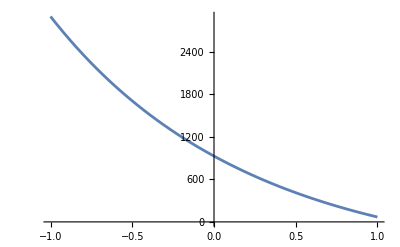

-Graphics3D-

```mathematica
{spA,snA,eA,pA,bA,MA}={-1/5,0,1/3,7,1,1}
Plot[
N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{(-4 A0+r1 r2 (A3+r1+r2)^2)}
,{bA,-1,1}]

Plot3D[{0,
N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{(-4 A0+r1 r2 (A3+r1+r2)^2)}}
,{spA,-1,1},{bA,-1,1},AxesLabel->{"s_∥","b",""}]
```

{1/10,0,3/5,10,1,1}

143.028

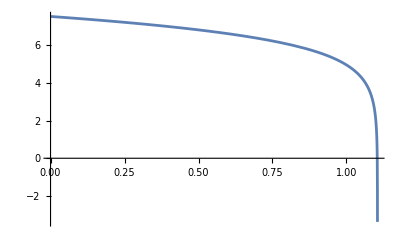

```mathematica
{spA,snA,eA,pA,bA,MA}={1/10,0,3/5,10,1,1}
N@Evaluate@ParamExactBW[spA,snA,eA,pA,bA,MA]@((-4 A0+r1 r2 (A3+r1+r2)^2))
Plot[N@Log@Evaluate@ParamExactBW[spA,snA,eA,pA,bA,MA]@((-4 A0+r1 r2 (A3+r1+r2)^2)),{bA,0,2},PlotRange->All]
```

### Comparison with the numerical solution

{1/10,0,1/4,10,1/10,1}

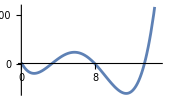

```mathematica
{spA,snA,eA,pA,bA,MA}={1/10,0,1/4,10,1/10,1}
Plot[{ParamExactBW[spA,snA,eA,pA,bA,MA]@R[r]},{r,0,15}]
```

```mathematica
{r1solE,r2solE,r3solE,r4solE}
```

```mathematica
{spA,snA,eA,pA,bA,MA}={1/10,0,1/4,10,1/10,1}
N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{A0,A1,A2,A3}
Print["Approximate solution:"]
{r1sol,r2sol,r3sol,r4sol}=N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r1,r2,r3,r4}
Print["Numerical solution:"]
r1234sol=NSolveValues[ParamExactBW[spA,snA,eA,pA,bA,MA]@R[r]==0,r,WorkingPrecision->40]
```

{1/10,0,1/4,10,1/10,1}

{18.6323,-363.89,178.802,-24.7148}

Approximate solution:

{13.3333,8.,3.32808,0.0526202}

Numerical solution:

{13.3676582590671419655635756927810062334,7.96419122447442845135635089873543967355,3.33038643013526152569334155336529429411,0.0525503660309410476662651374234284115491}

### Kepler parameters, re-describing the roots r_3 and r_4

#### Initialize of Toep

```mathematica
Toep[exp_]:=Module[{},
W==(p^2 Y+2 b p (-2+p+(2+p) (1-Z))+b^2 Z^2);
Ws==(p (9-2 p+3 (1-Z))-8 b (2-Z));
Wbp==(-b+p) W;
V==p X-2 b (-2+Z);
ℰ2Approxep=W/(p^2 (V))+(sp Z^2 √Wbp (p^2+b (-2 p+Z)))/(p^3 (V)^2);
𝒥2Approxep=(p^2 (-b+p))/V+(sp (Ws) √Wbp)/(V)^2;
exp/.{A0->A0f,A1->A1f,A2->A2f,A3->A3f}/.{ℰ^2->ℰ2Approxep,𝒥^2->𝒥2Approxep}/.{ℰ->√ℰ2Approxep,𝒥->√𝒥2Approxep}]
```

#### r3solE

##### Expand

```mathematica
r3solE
r3solE//Toep;
Series[%,{sp,0,1}];
Simplify[%,Assumptions->X>0&&Y>0&&Z>0&&p>0&&p X>Y&&-p^2 V+W<0&&W-p^3 X<0&&4 b+p X-2 b Z>0&&W>0&&V>0]/.{(-b+p) W->Wbp,√(-b+p) W^(5/2)->√Wbp W^2};
r3solNS=Normal@Simplify[%,Assumptions->√Wbp>0&&Wbp>0]
%/.{b->0}
```

((√((p^2 (-4 A0+(p^2 (A3+(2 p)/Z)^2)/Z))/Z)-(p^2 (A3+(2 p)/Z))/Z) Z)/(2 p^2)

(p (-p^2 V+W+p V Z+√(p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z)))))/((p^2 V-W) Z)+(sp Z^2 (4 p^2 √Wbp (p^2+b (-2 p+Z))-(2 (b^3 p (p^2 V-W) (2 p-Z) Z^2-b^2 p^2 (p^2 V-W) (3 p-Z) Z^2+2 p^4 V (p^2 V-W-p V Z)+b (-4 p^5 V^2+W^2 (4 V+Ws)+p^6 V Z^2-2 p^2 V W (4 V+Ws+Z)-2 p^3 V (-2 W+V Z^2)+p^4 (4 V^3-W Z^2+V^2 (Ws+6 Z)))))/(V √((p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z)))/Wbp))))/(4 p (-p^2 V+W)^2)

(p (-p^2 V+W+p V Z+√(p^4 V^2+W^2-2 p^3 V^2 Z+2 p V W Z+p^2 V (-2 W+V Z^2))))/((p^2 V-W) Z)+(sp Z^2 (4 p^4 √Wbp-(4 p^4 (p^2 V-W-p V Z))/(√((p^4 V^2+W^2-2 p^3 V^2 Z+2 p V W Z+p^2 V (-2 W+V Z^2))/Wbp))))/(4 p (-p^2 V+W)^2)

##### Simplify

```mathematica
$Assumptions=And[t[]∈Reals,r[]∈Reals,r[]>0,θ[]∈Reals,π>=θ[]>=0,ϕ[]∈Reals,G∈Reals,G>0,M∈Reals,M>=0,-1+e^2<0,p>0,Z>0,-b+p>0];
```

```mathematica
r3CL=CoefficientList[Normal@r3solNS/.{Wbp->(-b+p) W,Ws->(p (9-2 p+3 (1-Z))-8 b (2-Z))},{sp}]
```

{(p (-p^2 V+W+p V Z+√(p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z)))))/((p^2 V-W) Z),1/(4 p (-p^2 V+W)^2)Z^2 (4 p^2 √((-b+p) W) (p^2+b (-2 p+Z))-(2 (b^3 p (p^2 V-W) (2 p-Z) Z^2-b^2 p^2 (p^2 V-W) (3 p-Z) Z^2+2 p^4 V (p^2 V-W-p V Z)+b (-4 p^5 V^2+W^2 (4 V+p (9-2 p+3 (1-Z))-8 b (2-Z))+p^6 V Z^2-2 p^2 V W (4 V+p (9-2 p+3 (1-Z))-8 b (2-Z)+Z)-2 p^3 V (-2 W+V Z^2)+p^4 (4 V^3-W Z^2+V^2 (p (9-2 p+3 (1-Z))-8 b (2-Z)+6 Z)))))/(V √((p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z)))/((-b+p) W))))}

```mathematica
eptoXYZ@FullSimplify@XYZtoep@r3CL[[1]]
```

(p ((b-p)^2+√U1) Z)/(p^2 V-W)

```mathematica
FullSimplify@eptoXYZ@Map[Simplify,r3CL[[2]],{3}]
eptoXYZ@Map[FullSimplify,#,{2}]&@eptoXYZ@Map[FullSimplify,#,{3}]&@XYZtoep@%
FullSimplify@eptoXYZ@FullSimplify@ParamExactBW[sn,sp,e,p,0,M]@%
```

1/(4 p (-p^2 V+W)^2)Z^2 ((4 b (p^2 V-W) (p^2 (8 b+(-4+p) p-2 V) V-(8 b+(-6+p) p-2 V) W)-2 b ((6+8 b-3 p) p^4 V^2+2 p^2 (-1-8 b+3 p) V W+(8 b-3 p) W^2) Z+2 p^2 (p V (-p (-b+p) (-2 p+b (2-2 b+p))+2 b V)+b (-2 b+p) (-b+p) W) Z^2+2 b^2 (b-p) p (p^2 V-W) Z^3)/(V √((-(-p^2 V+W)^2+2 p V (p^2 V-W) Z-p^2 V^2 Z^2+b (-b+p) (p^2 V-W) Z^3)/((b-p) W)))+4 p^2 √((-b+p) W) (p^2+b (-2 p+Z)))

(Z^2 (4 p^2 √((-b+p) W) (p^2+b (-2 p+Z))+(2 p (2 p^5+b^2 p^2 (16-p (-2+Z))+2 b^3 p (p (-2+Z)-3 Z)+b^4 Z^2+2 b p^3 (-8-(-2+p) p+Z)))/(√(U1/((-b+p) (b (1+e)^2+p (-2-2 e+p)) (b (-1+e)^2+p (-2+2 e+p)))))))/(4 p (W-p^3 X+2 b p^2 (-2+Z))^2)

(√p (1/(√(1/Y))+√Y))/(-4+p)^2

##### Conclusion of r_3

```mathematica
r3soleq=(p ((b-p)^2+√((b-p) (b^2 p+b (-1+p) p^2-p^3-b^3 (-1+Z)))) Z)/(p^2 V-W)+sp ((p √((-b+p) W) Z^2 (p^2+b (-2 p+Z)))/((-p^2 V+W)^2)+(√((-b+p) W) Z (2 p^5+b^2 p^2 (16-p (-2+Z))+2 b^3 p (p (-2+Z)-3 Z)+b^4 Z^2+2 b p^3 (-8-(-2+p) p+Z)))/(2 (p^2 V-W) √(-((b-p) (-b^2 p-b (-1+p) p^2+p^3+b^3 (-1+Z)))) (4 b p+(-4+p) p^2-b^2 Z)));
```

#### r4solE

##### Expand

```mathematica
r4solE
r4solE//Toep;
Series[%,{sp,0,1}];
r4solNS=Normal@Simplify[%,Assumptions->X>0&&Y>0&&Z>0&&p>0&&p X>Y&&-p^2 V+W<0&&W-p^3 X<0&&4 b+p X-2 b Z>0&&W>0&&V>0]
%/.{b->0}
```

(2 A0)/(√((p^2 (-4 A0+(p^2 (A3+(2 p)/Z)^2)/Z))/Z)-(p^2 (A3+(2 p)/Z))/Z)

-(b (b-p) p Z^2)/(-p^2 V+W+p V Z+√(p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z))))-(b sp (-p^2 V+W)^2 Z^2 (1/(√V)2 p^4 (p (p^2 V-W) (8 √((-b+p) V W)+√(Wbp/V) Ws)+p √(Wbp/V) ((p^2 V-W) Ws+2 (b-p) p Z^2 (2 b p-p^2-b Z))) (p^2 V-W-p V Z-√(p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z))))+1/(b (b-p) (p^2 V-W) Z^3+(-p^2 V+W+p V Z)^2)(b-p) Z^3 (4 p^7 √Wbp (2 b p-p^2-b Z) (b (b-p) (p^2 V-W) Z^3+(-p^2 V+W+p V Z)^2)-p^3 √(p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z))) (-4 p^4 √Wbp (p^2 V-W-p V Z) (p^2+b (-2 p+Z))-(b p (p^2 V-W) (p (p^2 V-W) (8 √((-b+p) V W)+√(Wbp/V) Ws)+p √(Wbp/V) ((p^2 V-W) Ws+2 (b-p) p Z^2 (2 b p-p^2-b Z))))/(√V)))))/(4 p^6 (p^2 V-W)^3 (-p^2 V+W+p V Z+√(p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z))))^2)

0

##### Simplify

```mathematica
$Assumptions=And[t[]∈Reals,r[]∈Reals,r[]>0,θ[]∈Reals,π>=θ[]>=0,ϕ[]∈Reals,G∈Reals,G>0,M∈Reals,M>=0,-1+e^2<0,p>0,Z>0,-b+p>0,V>0];
```

```mathematica
r4CL=CoefficientList[Normal@r4solNS/.{Wbp->(-b+p) W,Ws->(p (9-2 p+3 (1-Z))-8 b (2-Z))}
/.{(p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z)))->U1 Z^4},{sp}];
```

```mathematica
eptoXYZ@FullSimplify@XYZtoep@r4CL[[1]]
```

(b p (-b+p))/((b-p)^2+√U1)

```mathematica
eptoXYZ@FullSimplify@XYZtoep@(p^4 V^2-p^3 V Z (2 V+b Z^2)+p W Z (2 V+b Z^2)+W (W-b^2 Z^3)+p^2 V (-2 W+Z^2 (V+b^2 Z)))
```

U1 Z^4

```mathematica
r4CL[[2]]
```

-((b (-p^2 V+W)^2 Z^2 (1/(√V)2 p^4 (p^2 V-W-p V Z-√(U1 Z^4)) (p (p^2 V-W) (8 √((-b+p) V W)+√(((-b+p) W)/V) (p (9-2 p+3 (1-Z))-8 b (2-Z)))+p √(((-b+p) W)/V) ((p^2 V-W) (p (9-2 p+3 (1-Z))-8 b (2-Z))+2 (b-p) p Z^2 (2 b p-p^2-b Z)))+1/(b (b-p) (p^2 V-W) Z^3+(-p^2 V+W+p V Z)^2)(b-p) Z^3 (4 p^7 √((-b+p) W) (2 b p-p^2-b Z) (b (b-p) (p^2 V-W) Z^3+(-p^2 V+W+p V Z)^2)-p^3 √(U1 Z^4) (-4 p^4 √((-b+p) W) (p^2 V-W-p V Z) (p^2+b (-2 p+Z))-1/(√V)b p (p^2 V-W) (p (p^2 V-W) (8 √((-b+p) V W)+√(((-b+p) W)/V) (p (9-2 p+3 (1-Z))-8 b (2-Z)))+p √(((-b+p) W)/V) ((p^2 V-W) (p (9-2 p+3 (1-Z))-8 b (2-Z))+2 (b-p) p Z^2 (2 b p-p^2-b Z)))))))/(4 p^6 (p^2 V-W)^3 (-p^2 V+W+p V Z+√(U1 Z^4))^2))

```mathematica
FullSimplify@eptoXYZ@Map[Simplify,r4CL[[2]],{1}]
```

-1/(4 p^6 ((b-p)^2+√U1)^2 (p^2 V-W)^3 Z^2)b (-p^2 V+W)^2 (4 (b-p) p^7 √((-b+p) W) Z^3 (2 b p-p^2-b Z)-1/(√V)2 p^4 ((b-p)^2+√U1) Z^2 (p (p^2 V-W) (8 √((-b+p) V W)+√(((-b+p) W)/V) (p (12-2 p-3 Z)+8 b (-2+Z)))+p √(((-b+p) W)/V) (2 (b-p) p Z^2 (2 b p-p^2-b Z)-(p^2 V-W) (2 (-6+p) p-8 b (-2+Z)+3 p Z)))-1/(b (p^2 V-W)+(b-p)^3 Z)p^3 √U1 Z^2 (4 (b-p)^2 p^4 √((-b+p) W) Z^2 (p^2+b (-2 p+Z))-1/(√V)b p (p^2 V-W) (p (p^2 V-W) (8 √((-b+p) V W)+√(((-b+p) W)/V) (p (12-2 p-3 Z)+8 b (-2+Z)))+p √(((-b+p) W)/V) (2 (b-p) p Z^2 (2 b p-p^2-b Z)-(p^2 V-W) (2 (-6+p) p-8 b (-2+Z)+3 p Z)))))

##### Conclusion of r_4

```mathematica
U==(b-p) (b^2 p+b (-1+p) p^2-p^3-b^3 (-1+Z))

r4solep==-(b (b-p) p)/((b-p)^2+√U)+(b sp (-p^2 V+W)^2 Z^4 (-(2 p^6 √(-b+p) (2 (-2+p) p+b Z) ((b-p)^2 +√U) √(b^2 Z^2-2 b p (p (-2+Z)+2 Z)+p^2 ((-4+p) p+4 Z)))/(Z^2 (-p (4 b+(-4+p) p)+b^2 Z)^3)-(p^3 √((-b+p) W)(-b+p) ((2 p^4 Z (p^2+b (-2 p+Z)))/((-p^2 V+W)^2)-(p^3 (-2 p^5+b^2 p^2 (-16+p (-2+Z))+2 b p^3 (8-2 p+p^2-Z)-b^4 Z^2+2 b^3 p (-p (-2+Z)+3 Z)))/(Z √U (4 b p+(-4+p) p^2-b^2 Z)^2)))/(V p^2-W)))/(2 p^6 ((b-p)^2 Z^2+Z^2 √U)^2)
```

U==(b-p) (b^2 p+b (-1+p) p^2-p^3-b^3 (-1+Z))

-(b (b-p) p)/((b-p)^2+√U1)+(b √(-b+p) sp Z (2 ((b-p)^2+√U1) √U3 (2 (-2+p) p+b Z)-(-b+p) √W (U2/(√U1)+2 p (p^2+b (-2 p+Z)))))/(2 ((b-p)^2+√U1)^2 (p^2 V-W))==-(b (b-p) p)/((b-p)^2+√U)+1/(2 p^6 ((b-p)^2 Z^2+√U Z^2)^2)b sp (-p^2 V+W)^2 Z^4 (-(2 p^6 √(-b+p) ((b-p)^2+√U) (2 (-2+p) p+b Z) √(b^2 Z^2-2 b p (p (-2+Z)+2 Z)+p^2 ((-4+p) p+4 Z)))/(Z^2 (-p (4 b+(-4+p) p)+b^2 Z)^3)-(p^3 (-b+p) √((-b+p) W) ((2 p^4 Z (p^2+b (-2 p+Z)))/((-p^2 V+W)^2)-(p^3 (-2 p^5+b^2 p^2 (-16+p (-2+Z))+2 b p^3 (8-2 p+p^2-Z)-b^4 Z^2+2 b^3 p (-p (-2+Z)+3 Z)))/(√U Z (4 b p+(-4+p) p^2-b^2 Z)^2)))/(p^2 V-W))

### Conclusion

U1=(b-p) (b^2 p+b (-1+p) p^2-p^3-b^3 (-1+Z));
U2=2 p^5+b^2 p^2 (16-p (-2+Z))+2 b^3 p (p (-2+Z)-3 Z)+b^4 Z^2+2 b p^3 (-8-(-2+p) p+Z)
U3=b^2 Z^2-2 b p (p (-2+Z)+2 Z)+p^2 ((-4+p) p+4 Z)

```mathematica
XE=p-3-e^2;
YE=(p-2)^2-4 e^2;
ZE=1-e^2;
WE=(p^2 YE+2 b p (-2+p+(2+p) (1-ZE))+b^2 ZE^2);
VE=p XE-2 b (-2+ZE);
U1E=(b-p) (b^2 p+b (-1+p) p^2-p^3-b^3 (-1+ZE));
U2E=2 p^5+b^2 p^2 (16-p (-2+ZE))+2 b^3 p (p (-2+ZE)-3 ZE)+b^4 ZE^2+2 b p^3 (-8-(-2+p) p+ZE);
U3E=b^2 ZE^2-2 b p (p (-2+ZE)+2 ZE)+p^2 ((-4+p) p+4 ZE);

r1solep=p/(1-e);
r2solep=p/(1+e);
r3solep=(p ((b-p)^2+√U1)Z)/(p^2 V-W)+sp Z^2(√((-b+p) W))/(2(p^2 V-W)^2)(2 p (p^2+b (-2 p+Z))+ U2/(√U1));
r4solep=-(b (b-p) p)/((b-p)^2+√U1)+sp (b Z √(-b+p))/(2 ((b-p)^2+√U1)^2(p^2 V-W)) (2((b-p)^2+√U1) (2 (-2+p) p+b Z) √U3-√W(-b+p)(2 p(p^2+b (-2 p+Z))+U2/(√U1)));
```

#### Check the result of the simplification

```mathematica
{spNum,snNum,eNum,pNum,bNum,MNum}={0.1,0,0.1,10,1,1};
ParamExactBW[spNum,snNum,eNum,pNum,bNum,MNum]@r4solep
ParamExactBW[spNum,snNum,eNum,pNum,bNum,MNum]@r4solNS
Plot3D[(ParamExactBW[spNum,snNum,eNum,pNum,bNum,MNum]@r4solep-ParamExactBW[spNum,snNum,eNum,pNum,bNum,MNum]@r4solNS),{spNum,0,1},{bNum,0,1},PlotRange->All]

ParamExactBW[spNum,snNum,eNum,pNum,bNum,MNum]@r3solep
ParamExactBW[spNum,snNum,eNum,pNum,bNum,MNum]@r3solNS
Plot3D[(ParamExactBW[spNum,snNum,eNum,pNum,bNum,MNum]@r3solep-ParamExactBW[spNum,snNum,eNum,pNum,bNum,MNum]@r3solNS),{spNum,0,1},{bNum,0,1},PlotRange->All]
```

0.840801

0.840801

-Graphics3D-

1.79075

1.79075

-Graphics3D-

### Error

#### Roots

```mathematica
{spA,snA,eA,pA,bA,MA}={1/10,0,1/4,20,10/10,0}
N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{A0,A1,A2,A3,√(1-ℰ2Approxep)}

Print["Approximate solution:"]
{r1solN,r2solN,r3solN,r4solN}=NSolveValues[ParamExactBW[spA,snA,eA,pA,bA,MA]@R[r]==0,r,WorkingPrecision->20]

Print["Numerical solution:"]
{r1solepN,r2solepN,r3solepN,r4solepN}=N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r1solep,r2solep,r3solep,r4solep}

Print["Error:"]
{r1solN,r2solN,r3solN,r4solN}-{r1solepN,r2solepN,r3solepN,r4solepN}
```

{1/10,0,1/4,20,1,0}

{522.775,-1025.2,524.9,-44.9496,0.210937}

Approximate solution:

{26.70269841316287769,15.96472482595794136,1.416262425012106012,0.8658736670917687858}

Numerical solution:

{26.6667,16.,1.41562,0.867212}

Error:

{0.0360317,-0.0352752,0.000646682,-0.00133796}

#### Comparison of integral results

```mathematica
{r1solN,r2solN,r3solN,r4solN}
(2 EllipticF[χ,k0^2])/(√((r1-r3) (r2-r4)))/.{k0->√((r3-r4)/(r2-r4)hr)}/.{hr->(r1-r2)/(r1-r3)}/.{χ->ArcSin[yr]}/.{yr->√(((r1-r3)(r0-r2))/((r1-r2)(r0-r3)))} 
rApprox=%/.{r1->r1solN,r2->r2solN,r3->r3solN,r4->r4solN}/.{r0->rint}
```

{26.70269841316287769,15.96472482595794136,1.416262425012106012,0.8658736670917687858}

(2 EllipticF[ArcSin[√(((r0-r2) (r1-r3))/((r1-r2) (r0-r3)))],((r1-r2) (r3-r4))/((r1-r3) (r2-r4))])/(√((r1-r3) (r2-r4)))

0.1023562185205665778 EllipticF[ArcSin[1.534555659329060297 √((-15.96472482595794136+rint)/(-1.416262425012106012+rint))],0.0154796223151866609]

```mathematica
{r1solN,r2solN,r3solN,r4solN}
{r1solepN,r2solepN,r3solepN,r4solepN}
Plot[{rApprox,
NIntegrate[1/(√(-(r0-r1solN)(r0-r2solN)(r0-r3solN)(r0-r4solN))),{r0,r2solN,rint},WorkingPrecision->10],
NIntegrate[1/(√(-(r0-r1solepN)(r0-r2solepN)(r0-r3solepN)(r0-r4solepN))),{r0,r2solepN,rint},WorkingPrecision->10]},{rint,Max[{r2solepN,r2solN}],Min[{r1solepN,r1solN}]}
,PlotLabels->{"Numerical root analytic integral","Numerical solution","Approximate solution"},FrameLabel->{"r","Int"},PlotTheme->"Scientific"]
```

{26.70269841316287769,15.96472482595794136,1.416262425012106012,0.8658736670917687858}

{26.6667,16.,1.41562,0.867212}

-Graphics-

```mathematica
Plot[{NIntegrate[1/(√(-(r0-r1solepN)(r0-r2solepN)(r0-r3solepN)(r0-r4solepN))),{r0,r2solepN,rint}]-,
rApprox-},{rint,Max[{r2solepN,r2solN}],Min[{r1solepN,r1solN}]}
,PlotLabels->{"Approximate solution","Numerical analytic integral"},PlotTheme->"Scientific"]
```

-Graphics-

## Integral of equation of motion

### Define new parameters in Integral

1.

```mathematica
{yr->√(((r1-r3)(r0-r2))/((r1-r2)(r0-r3))),hr->(r1-r2)/(r1-r3),hrp->hr(r3-rp)/(r2-rp),hrn->hr(r3-rn)/(r2-rn),k0^2->(r1-r2)/(r1-r3)(r3-r4)/(r2-r4)};
```

2.

```mathematica
{1/(r0-rp)->1/(r3-rp)(1+(r2-r3)/((r2-rp) (-1+hrp yr^2))),1/(r0-rn)->1/(r3-rn)(1+(r2-r3)/((r2-rn) (-1+hrn yr^2)))};
{r0->r3+(r2-r3)/(1-hr  yr^2)};
```

Integral transformation

```mathematica
{1/(r0-rp)->1/(r3-rp)(1+(r2-r3)/((r2-rp) (-1+hrp yr^2)))}/.{yr->√(((r1-r3)(r0-r2))/((r1-r2)(r0-r3))),hr->(r1-r2)/(r1-r3),hrp->(r1-r2)/(r1-r3)(r3-rp)/(r2-rp),hrn->(r1-r2)/(r1-r3)(r3-rn)/(r2-rn),k0^2->(r1-r2)/(r1-r3)(r3-r4)/(r2-r4)}//FullSimplify
{1/(r0-rn)->1/(r3-rn)(1+(r2-r3)/((r2-rn) (-1+hrn yr^2)))}/.{yr->√(((r1-r3)(r0-r2))/((r1-r2)(r0-r3))),hr->(r1-r2)/(r1-r3),hrp->(r1-r2)/(r1-r3)(r3-rp)/(r2-rp),hrn->(r1-r2)/(r1-r3)(r3-rn)/(r2-rn),k0^2->(r1-r2)/(r1-r3)(r3-r4)/(r2-r4)}//FullSimplify
{r0->r3+(r2-r3)/(1-hr  yr^2)}/.{yr->√(((r1-r3)(r0-r2))/((r1-r2)(r0-r3))),hr->(r1-r2)/(r1-r3),hrp->(r1-r2)/(r1-r3)(r3-rp)/(r2-rp),hrn->(r1-r2)/(r1-r3)(r3-rn)/(r2-rn),k0^2->(r1-r2)/(r1-r3)(r3-r4)/(r2-r4)}//FullSimplify
```

{1/(r0-rp)→1/(r0-rp)}

{1/(r0-rn)→1/(r0-rn)}

{r0→r0}

3. Differential relation

```mathematica
ⅆr0->(2 hr (r2-r3) yr)/((1-hr yr^2)^2)ⅆyr
```

ⅆr0→(2 hr (r2-r3) yr ⅆyr)/((1-hr yr^2)^2)

### Integral of Carter-Mino time λ

#### Calculation

```mathematica
1/(√(-(r0-r1)(r0-r2)(r0-r3)(r0-r4)))ⅆr0
FullSimplify[%/.{ⅆr0->(2 hr (r2-r3) yr)/((1-hr yr^2)^2)ⅆyr}/.{1/(r0-rp)->1/(r3-rp)(1+(r2-r3)/((r2-rp) (-1+hrp yr^2)))}/.{r0->r3+(r2-r3)/(1-hr  yr^2)},
Assumptions->1-hr yr^2>0&&r2-r3>0&&-r1+r3<0&&yr>0];
%/.{-r1+r2->-hr(r1-r3)}
FullSimplify[%,Assumptions->1-hr yr^2>0&&r2-r3>0&&-r1+r3<0&&yr>0&&hr>0]/.{hr->(r2-r4)/(r3-r4)k0^2}
%//Simplify
```

ⅆr0/(√((-r0+r1) (r0-r2) (r0-r3) (r0-r4)))

(2 hr ⅆyr)/(√(hr (-hr (r1-r3)+hr (r1-r3) yr^2) (-r2+r4+hr (r3-r4) yr^2)))

(2 ⅆyr)/(√((r1-r3) (-1+yr^2) (-r2+r4+k0^2 (r2-r4) yr^2)))

(2 ⅆyr)/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))

```mathematica
∫(2 ⅆyr)/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))
tr=FullSimplify[%,Assumptions->r2>0&&1-yr^2>0&&(r2-hr r3 yr^2)>0&&1-k0^2 yr^2>0]/.{ArcSin[yr]->χ}//Simplify
```

(2 √(1-yr^2) √(1-k0^2 yr^2) EllipticF[ArcSin[yr],k0^2])/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))

(2 EllipticF[χ,k0^2])/(√((r1-r3) (r2-r4)))

##### 式子（93）

```mathematica
λ==(2 EllipticF[χ,k0^2])/(√(1-ℰ^2)√((r1-r3) (r2-r4)));
```

```mathematica
Sin[JacobiAmplitude[(√((r2-r4)(r1-r3)(1-ℰ^2)))/2(λ[r0]-λ[r2]),k0^2]]^2==((r1-r3)(r0-r2))/((r1-r2)(r0-r3))
Solve[sn[(√((r2-r4)(r1-r3)(1-ℰ^2)))/2(λ-λ0),k0^2]^2==((r1-r3)(r0-r2))/((r1-r2)(r0-r3)),r0]//Simplify
```

JacobiSN[1/2 √((r1-r3) (r2-r4) (1-ℰ^2)) (λ[r0]-λ[r2]),k0^2]^2==((r0-r2) (r1-r3))/((r1-r2) (r0-r3))

{{r0→(r2 (-r1+r3)+(r1-r2) r3 sn[1/2 √(-((r1-r3) (r2-r4) (-1+ℰ^2))) (λ-λ0),k0^2]^2)/(-r1+r3+(r1-r2) sn[1/2 √(-((r1-r3) (r2-r4) (-1+ℰ^2))) (λ-λ0),k0^2]^2)}}

#### Conclusion

```mathematica
λr0[χ_]:=(2 EllipticF[χ,k0^2])/(√(1-ℰ^2)√((r1-r3) (r2-r4)));
```

### Integral of t

#### Calculation process

```mathematica
r^2/.{f->fShBW}/.{M->1}//Simplify//InputForm
```

r^2

```mathematica
ℰ/f[r]-(𝒥 ϵ {{s, {{2}, {}}}} f'[r])/(2 f[r])
(ℰ/f[r]+(sp 𝒥 f'[r])/(2 f[r] r))r[]^2/.{r[]->r0}/.{f->fShBW}/.{M->1}//Simplify
```

(r0^4 ℰ-b sp 𝒥+r0 sp 𝒥)/(b+(-2+r0) r0)

4 ℰ-2 q Q-Q^2 ℰ + 2 r ℰ  -  q Q r + ℰ r^2+ (I_pC/(r-r_p)-I_nC/(r-r_p))

```mathematica
rpIntCharge= 1/(rp-rn)((+8 ℰ-4 b ℰ+sp 𝒥) rp+(-4 ℰ b +ℰ b^2 -sp b 𝒥));
rnIntCharge= 1/(rp-rn)((+8 ℰ-4 b ℰ+sp 𝒥) rn+(-4 ℰ b +ℰ b^2 - 𝒥 sp b ));
(r0^4 ℰ-b sp 𝒥+r0 sp 𝒥)/(b+(-2+r0) r0)==r0^2 ℰ  + 2 r0 ℰ+(4 ℰ-b ℰ) + (rpIntCharge/(r0-rp)-rnIntCharge/(r0-rn))/.{rp->1+√(1-b),rn->1-√(1-b)}//FullSimplify
```

True

```mathematica
Clear[rpIntCharge]
Clear[rnIntCharge]
{(r0^2 ℰ  + 2 r0 ℰ+(4 ℰ-b ℰ))/(√(-(r0-r1)(r0-r2)(r0-r3)(r0-r4)))ⅆr0,(rpIntCharge/(r0-rp))/(√(-(r0-r1)(r0-r2)(r0-r3)(r0-r4)))ⅆr0,(-rnIntCharge/(r0-rn))/(√(-(r0-r1)(r0-r2)(r0-r3)(r0-r4)))ⅆr0}
FullSimplify[%/.{ⅆr0->(2 hr (r2-r3) yr)/((1-hr yr^2)^2)ⅆyr}/.{1/(r0-rp)->1/(r3-rp)(1+(r2-r3)/((r2-rp) (-1+hrp yr^2)))}/.{1/(r0-rn)->1/(r3-rn)(1+(r2-r3)/((r2-rn) (-1+hrn yr^2)))}/.{r0->r3+(r2-r3)/(1-hr  yr^2)},
Assumptions->1-hr yr^2>0&&r2-r3>0&&-r1+r3<0&&yr>0];
%/.{-r1+r2->-hr(r1-r3)}/.{(-r3+rp+hrp (r2-rp) yr^2)->(r3-rp) (-1+hr yr^2)};
FullSimplify[%,Assumptions->1-hr yr^2>0&&r2-r3>0&&-r1+r3<0&&yr>0&&hr>0]
%/.{(r3-r4)->((r2-r4)k0^2)/hr,hrp (-r2+rp)->-hr(r3-rp),hrn (-r2+rn)->-hr(r3-rn)}//Simplify
```

{((4 ℰ-b ℰ+2 r0 ℰ+r0^2 ℰ) ⅆr0)/(√((-r0+r1) (r0-r2) (r0-r3) (r0-r4))),(rpIntCharge ⅆr0)/(√((-r0+r1) (r0-r2) (r0-r3) (r0-r4)) (r0-rp)),-(rnIntCharge ⅆr0)/(√((-r0+r1) (r0-r2) (r0-r3) (r0-r4)) (r0-rn))}

{(2 (4-b+2 r2+r2^2-2 hr (4-b+r2+r3+r2 r3) yr^2+hr^2 (4-b+r3 (2+r3)) yr^4) ℰ ⅆyr)/((-1+hr yr^2)^2 √((r1-r3) (-1+yr^2) (-r2+r4+hr (r3-r4) yr^2))),(2 rpIntCharge (-1+hr yr^2) ⅆyr)/((r2-rp) (-1+hrp yr^2) √((r1-r3) (-1+yr^2) (-r2+r4+hr (r3-r4) yr^2))),(2 rnIntCharge (r3-rn+hrn (-r2+rn) yr^2) ⅆyr)/((r2-rn) (r3-rn) (-1+hrn yr^2) √((r1-r3) (-1+yr^2) (-r2+r4+hr (r3-r4) yr^2)))}

{(2 (4-b+2 r2+r2^2-2 hr (4-b+r2+r3+r2 r3) yr^2+hr^2 (4-b+r3 (2+r3)) yr^4) ℰ ⅆyr)/((-1+hr yr^2)^2 √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2))),(2 rpIntCharge (-1+hr yr^2) ⅆyr)/((r2-rp) (-1+hrp yr^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2))),-(2 rnIntCharge (-1+hr yr^2) ⅆyr)/((r2-rn) (-1+hrn yr^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))}

```mathematica
∫(2 (4-b+2 r2+r2^2-2 hr (4-b+r2+r3+r2 r3) yr^2+hr^2 (4-b+r3 (2+r3)) yr^4) ℰ ⅆyr)/((-1+hr yr^2)^2 √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))+∫(2 rpIntCharge (-1+hr yr^2) ⅆyr)/((r2-rp) (-1+hrp yr^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))+∫-(2 rnIntCharge (-1+hr yr^2) ⅆyr)/((r2-rn) (-1+hrn yr^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))
```

(ℰ (hr (r2-r3)^2 √(1-yr^2) (-1+hr yr^2) √(1-k0^2 yr^2) EllipticE[ArcSin[yr],k0^2]-(-hr+k0^2) (8+2 b (-1+hr)-r2^2+4 r3+2 r2 r3+r3^2-2 hr (4+2 r3+r3^2)) √(1-yr^2) (-1+hr yr^2) √(1-k0^2 yr^2) EllipticF[ArcSin[yr],k0^2]+(r2-r3) (hr^2 (r2-r3) yr (-1+yr^2) (-1+k0^2 yr^2)+(2 hr (1+k0^2) (2+r2+r3)-k0^2 (4+3 r2+r3)-hr^2 (4+r2+3 r3)) √(1-yr^2) (-1+hr yr^2) √(1-k0^2 yr^2) EllipticPi[hr,ArcSin[yr],k0^2])))/((-1+hr) (-hr+k0^2) (-1+hr yr^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))-(2 rnIntCharge √(1-yr^2) √(1-k0^2 yr^2) (hr EllipticF[ArcSin[yr],k0^2]+(-hr+hrn) EllipticPi[hrn,ArcSin[yr],k0^2]))/(hrn (r2-rn) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))+(2 rpIntCharge √(1-yr^2) √(1-k0^2 yr^2) (hr EllipticF[ArcSin[yr],k0^2]+(-hr+hrp) EllipticPi[hrp,ArcSin[yr],k0^2]))/(hrp (r2-rp) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))

```mathematica
tr=Simplify[%,Assumptions->r2>r3>0&&1-yr^2>0&&1-k0^2 yr^2>0]/.{ArcSin[yr]->χ}
```

1/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))(1/((-1+hr) (-hr+k0^2) (-1+hr yr^2))ℰ (hr (r2-r3)^2 (-1+hr yr^2) √((-1+yr^2) (-1+k0^2 yr^2)) EllipticE[χ,k0^2]-(-hr+k0^2) (8+2 b (-1+hr)-r2^2+4 r3+2 r2 r3+r3^2-2 hr (4+2 r3+r3^2)) (-1+hr yr^2) √((-1+yr^2) (-1+k0^2 yr^2)) EllipticF[χ,k0^2]+(r2-r3) (hr^2 (r2-r3) yr (-1+yr^2) (-1+k0^2 yr^2)+(2 hr (1+k0^2) (2+r2+r3)-k0^2 (4+3 r2+r3)-hr^2 (4+r2+3 r3)) (-1+hr yr^2) √((-1+yr^2) (-1+k0^2 yr^2)) EllipticPi[hr,χ,k0^2]))-(2 rnIntCharge √((-1+yr^2) (-1+k0^2 yr^2)) (hr EllipticF[χ,k0^2]+(-hr+hrn) EllipticPi[hrn,χ,k0^2]))/(hrn (r2-rn))+(2 rpIntCharge √((-1+yr^2) (-1+k0^2 yr^2)) (hr EllipticF[χ,k0^2]+(-hr+hrp) EllipticPi[hrp,χ,k0^2]))/(hrp (r2-rp)))

```mathematica
Collect[√((r1-r3) (r2-r4)) tr,{EllipticE[χ,k0^2], EllipticF[χ,k0^2],EllipticPi[hr,χ,k0^2],EllipticPi[hrn,χ,k0^2],EllipticPi[hrp,χ,k0^2]}]
Map[FullSimplify[#/.{hrp->hr(r3-rp)/(r2-rp)},Assumptions->r2>0&&1-yr^2>0&&(r2-hr r3 yr^2)>0]&,%,{1}];
%/.{yr->√(((r1-r3)(r0-r2))/((r1-r2)(r0-r3)))}/.{hr->(r1-r2)/(r1-r3)};
Map[Collect[FullSimplify[#/.{hrp->hr(r3-rp)/(r2-rp),hrn->hr(r3-rn)/(r2-rn)}/.{hr->(r1-r2)/(r1-r3)}/.{k0->√((r1-r2)/(r1-r3)(r3-r4)/(r2-r4))},Assumptions->r1>r2>r3>0&&r2-r4>0&&r0-r3>0],{hr}]&,%,{1}]
```

(hr^2 (r2-r3)^2 √((r1-r3) (r2-r4)) yr (-1+yr^2) (-1+k0^2 yr^2) ℰ)/((-1+hr) (-hr+k0^2) (-1+hr yr^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))+(hr (r2-r3)^2 √((r1-r3) (r2-r4)) √((-1+yr^2) (-1+k0^2 yr^2)) ℰ EllipticE[χ,k0^2])/((-1+hr) (-hr+k0^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))+(√((r1-r3) (r2-r4)) (-(2 hr rnIntCharge √((-1+yr^2) (-1+k0^2 yr^2)))/(hrn (r2-rn))+(2 hr rpIntCharge √((-1+yr^2) (-1+k0^2 yr^2)))/(hrp (r2-rp))-((8+2 b (-1+hr)-r2^2+4 r3+2 r2 r3+r3^2-2 hr (4+2 r3+r3^2)) √((-1+yr^2) (-1+k0^2 yr^2)) ℰ)/(-1+hr)) EllipticF[χ,k0^2])/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))+((r2-r3) (2 hr (1+k0^2) (2+r2+r3)-k0^2 (4+3 r2+r3)-hr^2 (4+r2+3 r3)) √((r1-r3) (r2-r4)) √((-1+yr^2) (-1+k0^2 yr^2)) ℰ EllipticPi[hr,χ,k0^2])/((-1+hr) (-hr+k0^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))-(2 (-hr+hrn) √((r1-r3) (r2-r4)) rnIntCharge √((-1+yr^2) (-1+k0^2 yr^2)) EllipticPi[hrn,χ,k0^2])/(hrn (r2-rn) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))+(2 (-hr+hrp) √((r1-r3) (r2-r4)) rpIntCharge √((-1+yr^2) (-1+k0^2 yr^2)) EllipticPi[hrp,χ,k0^2])/(hrp (r2-rp) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))

-√(r0-r2) √(((r0-r1) (r1-r3) (r0-r4) (-r2+r4))/(r0-r3)) ℰ+(r1-r3) (r2-r4) ℰ EllipticE[χ,((r1-r2) (r3-r4))/((r1-r3) (r2-r4))]+((2 (rnIntCharge rp-rn rpIntCharge+r3 (-rnIntCharge+rpIntCharge))+(8-2 b+r1 (-r2+r3)+r3 (4+r2+r3)) (r3-rn) (r3-rp) ℰ) EllipticF[χ,((r1-r2) (r3-r4))/((r1-r3) (r2-r4))])/((r3-rn) (r3-rp))+(r2-r3) (4+r1+r2+r3+r4) ℰ EllipticPi[(r1-r2)/(r1-r3),χ,((r1-r2) (r3-r4))/((r1-r3) (r2-r4))]+(2 (r2-r3) rnIntCharge EllipticPi[((r1-r2) (r3-rn))/((r1-r3) (r2-rn)),χ,((r1-r2) (r3-r4))/((r1-r3) (r2-r4))])/((r2-rn) (r3-rn))+(2 (r2-r3) rpIntCharge EllipticPi[((r1-r2) (r3-rp))/((r1-r3) (r2-rp)),χ,((r1-r2) (r3-r4))/((r1-r3) (r2-r4))])/((r2-rp) (-r3+rp))

```mathematica
(hr^2 (r2-r3)^2 √((r1-r3) (r2-r4)) yr (-1+yr^2) (-1+k0^2 yr^2) ℰ)/((-1+hr) (-hr+k0^2) (-1+hr yr^2) √((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))/.{yr->Sin[χ]}
%/.{hr->(r1-r2)/(r1-r3)}/.{k0->√((r1-r2)/(r1-r3)(r3-r4)/(r2-r4))};
FullSimplify[%,Assumptions->r2>0&&r2-r3>0&&r1-r3>0&&r1-r2>0&&r0-r3>0&&r0-r2>0&&r0-r1<0&&r0>0]
```

(hr^2 (r2-r3)^2 √((r1-r3) (r2-r4)) ℰ Sin[χ] (-1+Sin[χ]^2) (-1+k0^2 Sin[χ]^2))/((-1+hr) (-hr+k0^2) (-1+hr Sin[χ]^2) √((r1-r3) (r2-r4) (-1+Sin[χ]^2) (-1+k0^2 Sin[χ]^2)))

((r1-r2) √((r1-r3) (r2-r4)) ℰ Sin[χ] √(-Cos[χ]^2 (-((r1-r3) (r2-r4))+(r1-r2) (r3-r4) Sin[χ]^2)))/(-r1+r3+(r1-r2) Sin[χ]^2)

```mathematica
((r1-r2) √((r1-r3) (r2-r4)) ℰ Sin[χ] √(-Cos[χ]^2 (-((r1-r3) (r2-r4))+(r1-r2) (r3-r4) Sin[χ]^2)))/(-r1+r3+(r1-r2) Sin[χ]^2)==((r1-r2) √((r1-r3) (r2-r4)) ℰ Sin[2 χ]/2  √(-(-((r1-r3) (r2-r4))+(r1-r2) (r3-r4) Sin[χ]^2)))/(-r1+r3+(r1-r2) (1-Cos[2 χ])/2)==((r1-r2) √((r1-r3) (r2-r4)) ℰ Sin[2 χ]  √(-(-((r1-r3) (r2-r4))+(r1-r2) (r3-r4) Sin[χ]^2)))/(2 r3-(r1+r2)-(r1-r2) Cos[2 χ])
```

((r1-r2) √((r1-r3) (r2-r4)) ℰ Sin[χ] √(-Cos[χ]^2 (-((r1-r3) (r2-r4))+(r1-r2) (r3-r4) Sin[χ]^2)))/(-r1+r3+(r1-r2) Sin[χ]^2)==((r1-r2) √((r1-r3) (r2-r4)) ℰ0 √((r1-r3) (r2-r4)-(r1-r2) (r3-r4) Sin[χ]^2) Sin[2 χ])/(2 (-r1+r3+1/2 (r1-r2) (1-Cos[2 χ])))==((r1-r2) √((r1-r3) (r2-r4)) ℰ0 √((r1-r3) (r2-r4)-(r1-r2) (r3-r4) Sin[χ]^2) Sin[2 χ])/(-r1-r2+2 r3-(r1-r2) Cos[2 χ])

```mathematica
2 Sin[χ]Cos[χ] == Sin[2 χ]//FullSimplify
1-2 Sin[χ]^2==Cos[2 χ]//FullSimplify
(1-Cos[2 χ])/2 ==Sin[χ]^2//FullSimplify
2( r1- r3+ (-r1+r2)( (1-Cos[2 χ])/2))//FullSimplify
```

True

True

True

r1+r2-2 r3+(r1-r2) Cos[2 χ]

#### Conclusion of

```mathematica
rpIntCharge==1/(rp-rn)(( 8 ℰ-4 b ℰ+sp 𝒥) rp+ b( (-4+b)ℰ-sp 𝒥));
rnIntCharge==1/(rp-rn)(( 8 ℰ-4 b ℰ+sp 𝒥) rn+ b (2 (-4+b)ℰ-sp 𝒥));

Tr0[χ_]:=1/(√(1-ℰ^2)√((r1-r3) (r2-r4)))(
((r1-r2) √((r1-r3) (r2-r4)) ℰ Sin[2 χ]  √(-(-((r1-r3) (r2-r4))+(r1-r2) (r3-r4) Sin[χ]^2)))/(2 r3-(r1+r2)-(r1-r2) Cos[2 χ])
+(r1-r3) (r2-r4) ℰ EllipticE[χ,k0^2]
+1/((r3-rn) (r3-rp))(-2 (rnIntCharge) (r3-rp)+2 (r3-rn) rpIntCharge+(8-2 b+r1 (-r2+r3)+r3 (4+r2+r3)) (r3-rn) (r3-rp)ℰ) EllipticF[χ,k0^2]
+(r2-r3) ((4+r1+r2+r3+r4) ℰ) EllipticPi[(r1-r2)/(r1-r3),χ,k0^2]
+(2 (r2-r3) rnIntCharge EllipticPi[((r1-r2) (r3-rn))/((r1-r3) (r2-rn)),χ,k0^2])/((r2-rn) (r3-rn))+(2 (r2-r3) rpIntCharge EllipticPi[((r1-r2) (r3-rp))/((r1-r3) (r2-rp)),χ,k0^2])/((r2-rp) (-r3+rp))
)/.{rpIntCharge->1/(rp-rn)(( +8 ℰ-4 b ℰ+sp 𝒥 ) rp+ b( (-4+b)ℰ-sp 𝒥)),rnIntCharge-> 1/(rp-rn)((  8 ℰ-4 b ℰ+sp 𝒥) rn+ b (2 (-4+b)ℰ-sp 𝒥))};
```

##### The Schwarzschild case

```mathematica
Tr0[χ]/.{rn->0,rp->2,b->0}
```

```mathematica
1/(√((r1-r3) (r2-r4)) √(1-ℰ^2))((r1-r3) (r2-r4) ℰ EllipticE[χ,k0^2]+(((-2+r3) r3 (8+r1 (-r2+r3)+r3 (4+r2+r3)) ℰ+2 r3 (8 ℰ+sp 𝒥)) EllipticF[χ,k0^2])/((-2+r3) r3)+(r2-r3) (4+r1+r2+r3+r4) ℰ EllipticPi[(r1-r2)/(r1-r3),χ,k0^2]+(2 (r2-r3) (8 ℰ+sp 𝒥) EllipticPi[((r1-r2) (-2+r3))/((-2+r2) (r1-r3)),χ,k0^2])/((-2+r2) (2-r3))+((r1-r2) √((r1-r3) (r2-r4)) ℰ √((r1-r3) (r2-r4)-(r1-r2) (r3-r4) Sin[χ]^2) Sin[2 χ])/(-r1-r2+2 r3-(r1-r2) Cos[2 χ]))
```

##### Latex

```mathematica
Clear[rpIntCharge,rnIntCharge]
1/(√(1-ℰ^2)√((r1-r3) (r2-r4)))(
((r1-r2) √((r1-r3) (r2-r4)) ℰ Sin[2 χ]  √(-(-((r1-r3) (r2-r4))+(r1-r2) (r3-r4) Sin[χ]^2)))/(2 r3-(r1+r2)-(r1-r2) Cos[2 χ])
+(r1-r3) (r2-r4) ℰ EllipticE[χ,k0^2]
+1/((r3-rn) (r3-rp))(-2 (rnIntCharge) (r3-rp)+2 (r3-rn) rpIntCharge+(8-2 b+r1 (-r2+r3)+r3 (4+r2+r3)) (r3-rn) (r3-rp)ℰ) EllipticF[χ,k0^2]
+(r2-r3) ((4+r1+r2+r3+r4) ℰ) EllipticPi[(r1-r2)/(r1-r3),χ,k0^2]
+(2 (r2-r3) rnIntCharge EllipticPi[((r1-r2) (r3-rn))/((r1-r3) (r2-rn)),χ,k0^2])/((r2-rn) (r3-rn))+(2 (r2-r3) rpIntCharge EllipticPi[((r1-r2) (r3-rp))/((r1-r3) (r2-rp)),χ,k0^2])/((r2-rp) (-r3+rp))
)/.{(r1-r2)/(r1-r3)(r3-rp)/(r2-rp)->hrp,(r1-r2)/(r1-r3)(r3-rn)/(r2-rn)->hrn,(r1-r2)/(r1-r3)->hr}/.{r1->Subscript[r, 1],r2->Subscript[r, 2],r3->Subscript[r, 3],r4->Subscript[r, 4],rp->Subscript[r, p],rn->Subscript[r, n],rpIntCharge->Subscript[ℐ, pC],rnIntCharge->Subscript[ℐ, nC]}
```

1/(√(1-ℰ^2) √((r_1-r_3) (r_2-r_4)))(ℰ EllipticE[χ,k0^2] (r_1-r_3) (r_2-r_4)+(ℰ Sin[2 χ] (r_1-r_2) √((r_1-r_3) (r_2-r_4)-Sin[χ]^2 (r_1-r_2) (r_3-r_4)) √((r_1-r_3) (r_2-r_4)))/(-r_1-Cos[2 χ] (r_1-r_2)-r_2+2 r_3)+ℰ EllipticPi[hr,χ,k0^2] (r_2-r_3) (4+r_1+r_2+r_3+r_4)+(2 EllipticPi[hrn,χ,k0^2] (r_2-r_3) ℐ_nC)/((r_2-r_n) (r_3-r_n))+(2 EllipticPi[hrp,χ,k0^2] (r_2-r_3) ℐ_pC)/((r_2-r_p) (-r_3+r_p))+(EllipticF[χ,k0^2] (ℰ (8-2 b+r_1 (-r_2+r_3)+r_3 (4+r_2+r_3)) (r_3-r_n) (r_3-r_p)-2 (r_3-r_p) ℐ_nC+2 (r_3-r_n) ℐ_pC))/((r_3-r_n) (r_3-r_p)))

1/(√(1-ℰ^2) √((r_1-r_3) (r_2-r_4)))(ℰ EllipticE[χ,k0^2] (r_1-r_3) (r_2-r_4)+(ℰ Sin[2 χ] (r_1-r_2))/(-r_1-Cos[2 χ] (r_1-r_2)-r_2+2 r_3)√((r_1-r_3) (r_2-r_4)-Sin[χ]^2 (r_1-r_2) (r_3-r_4)) √((r_1-r_3) (r_2-r_4))+ℰ EllipticPi[hr,χ,k0^2] (r_2-r_3) (4+r_1+r_2+r_3+r_4)+(2 EllipticPi[hrn,χ,k0^2] (r_2-r_3) ℐ_nC)/((r_2-r_n) (r_3-r_n))+(2 EllipticPi[hrp,χ,k0^2] (r_2-r_3) ℐ_pC)/((r_2-r_p) (-r_3+r_p))+EllipticF[χ,k0^2]/((r_3-r_n) (r_3-r_p)) (ℰ (8-2 b+r_1 (-r_2+r_3)+r_3 (4+r_2+r_3)) (r_3-r_n) (r_3-r_p)-2 (r_3-r_p) ℐ_nC+2 (r_3-r_n) ℐ_pC))

1/(√(1-ℰ^2) √((r_1-r_3) (r_2-r_4)))(ℰ EllipticE[χ,k0^2] (r_1-r_3) (r_2-r_4)+(ℰ Sin[2 χ] (r_1-r_2) √((r_1-r_3) (r_2-r_4)-Sin[χ]^2 (r_1-r_2) (r_3-r_4)) √((r_1-r_3) (r_2-r_4)))/(-r_1-Cos[2 χ] (r_1-r_2)-r_2+2 r_3)+ℰ EllipticPi[hr,χ,k0^2] (r_2-r_3) (4+r_1+r_2+r_3+r_4)+(2 EllipticPi[hrn,χ,k0^2] (r_2-r_3) ℐ_nC)/((r_2-r_n) (r_3-r_n))+(2 EllipticPi[hrp,χ,k0^2] (r_2-r_3) ℐ_pC)/((r_2-r_p) (-r_3+r_p))+1/((r_3-r_n) (r_3-r_p))EllipticF[χ,k0^2] (ℰ (8-2 b+r_1 (-r_2+r_3)+r_3 (4+r_2+r_3)) (r_3-r_n) (r_3-r_p)-2 (r_3-r_p) ℐ_nC+2 (r_3-r_n) ℐ_pC))

hrp=((r_1-r_2) (r_3-r_p))/((r_1-r_3) (r_2-r_p))

hrn=((r_1-r_2) (r_3-r_n))/((r_1-r_3) (r_2-r_n))

hr=(r_1-r_2)/(r_1-r_3),

### Integral of φ

#### Calculation process

```mathematica
(𝒥/r0^2+(sp ℰ)/r0^2)r0^2//Simplify
```

sp ℰ+𝒥

```mathematica
{(𝒥+sp ℰ)/(√(-(r0-r1)(r0-r2)(r0-r3)(r0-r4)))ⅆr0};
FullSimplify[%/.{ⅆr0->(2 hr (r2-r3) yr)/((1-hr yr^2)^2)ⅆyr}/.{r0->r3+(r2-r3)/(1-hr  yr^2)},
Assumptions->1-hr yr^2>0&&r2-r3>0&&-r1+r3<0&&yr>0];
%/.{-r1+r2->-hr(r1-r3)}/.{(-r3+rp+hrp (r2-rp) yr^2)->(r3-rp) (-1+hr yr^2)};
FullSimplify[%,Assumptions->1-hr yr^2>0&&r2-r3>0&&-r1+r3<0&&yr>0&&hr>0]
%/.{hr r3->hr32 r2,(r3-r4)->((r2-r4)k0^2)/hr,hrp (-r2+rp)->-hr(r3-rp),hrn (-r2+rn)->-hr(r3-rn),hrn (r2-rn)->hr(r3-rn)}//FullSimplify
```

{(2 (sp ℰ+𝒥) ⅆyr)/(√((r1-r3) (-1+yr^2) (-r2+r4+hr (r3-r4) yr^2)))}

{(2 (sp ℰ+𝒥) ⅆyr)/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))}

```mathematica
∫(2 (sp ℰ+𝒥) ⅆyr)/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))
Simplify[%,Assumptions->r2>0&&1-yr^2>0&&1-k0^2 yr^2>0&&(r2-hr r3 yr^2)>0]
tr=%/.{ArcSin[yr]->χ}
```

(2 √(1-yr^2) √(1-k0^2 yr^2) (sp ℰ+𝒥) EllipticF[ArcSin[yr],k0^2])/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)))

(2 (sp ℰ+𝒥) EllipticF[ArcSin[yr],k0^2])/(√((r1-r3) (r2-r4)))

(2 (sp ℰ+𝒥) EllipticF[χ,k0^2])/(√((r1-r3) (r2-r4)))

```mathematica
Collect[(hr32 r2 √((r1-r3) (r2-r4)))/2 tr,{EllipticE[χ,k0^2], EllipticF[χ,k0^2],EllipticPi[hr,χ,k0^2],EllipticPi[hrn,χ,k0^2],EllipticPi[hrp,χ,k0^2]}]
```

hr32 r2 (sp ℰ+𝒥) EllipticF[χ,k0^2]

#### Conclusion of

(2 (sp ℰ+𝒥) EllipticF[χ,k_0^2])/(√((r_1-r_3) (r_2-r_4)))

```mathematica
Φr0[χ_]:=(2(sp ℰ+𝒥) EllipticF[χ,k0^2])/(√(1-ℰ^2)√((r1-r3) (r2-r4)));
```

```mathematica
Φr0[χ]/.{q->0}
```

(2 (sp ℰ+𝒥) EllipticF[χ,k0^2])/(√((r1-r3) (r2-r4)) √(1-ℰ^2))

### Integral of ψ

#### Calculation process

```mathematica
(ℰ 𝒥)/(𝒥^2+r0^2)r0^2
 Psiint=ℰ 𝒥
```

(r0^2 ℰ 𝒥)/(r0^2+𝒥^2)

ℰ 𝒥

```mathematica
(Psiint0/(𝒥^2+r0^2)r0^2)/(√(-(r0-r1) (r0-r2) (r0-r3)(r0 -r4)))ⅆr0
FullSimplify[%/.{ⅆr0->(2 hr (r2-r3) yr)/((1-hr yr^2)^2)ⅆyr}/.{r0->r3+(r2-r3)/(1-hr  yr^2)},
Assumptions->1-hr yr^2>0&&r2-r3>0&&-r1+r3<0&&yr>0];
%/.{-r1+r2->-hr(r1-r3)}/.{(-r3+rp+hrp (r2-rp) yr^2)->(r3-rp) (-1+hr yr^2)};
FullSimplify[%,Assumptions->1-hr yr^2>0&&r2-r3>0&&-r1+r3<0&&yr>0&&hr>0]
%/.{hr r3->hr32 r2,(r3-r4)->((r2-r4)k0^2)/hr,hrp (-r2+rp)->-hr(r3-rp),hrn (-r2+rn)->-hr(r3-rn),hrn (r2-rn)->hr(r3-rn)}//FullSimplify
```

(Psiint0 r0^2 ⅆr0)/(√((-r0+r1) (r0-r2) (r0-r3) (r0-r4)) (r0^2+𝒥^2))

(2 Psiint0 (r2-hr r3 yr^2)^2 ⅆyr)/(√((r1-r3) (-1+yr^2) (-r2+r4+hr (r3-r4) yr^2)) ((r2-hr r3 yr^2)^2+(-1+hr yr^2)^2 𝒥^2))

(2 Psiint0 (r2-hr32 r2 yr^2)^2 ⅆyr)/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)) ((r2-hr32 r2 yr^2)^2+(-1+hr yr^2)^2 𝒥^2))

```mathematica
∫(2 Psiint0 (r2-hr32 r2 yr^2)^2 ⅆyr)/(√((r1-r3) (r2-r4) (-1+yr^2) (-1+k0^2 yr^2)) ((r2-hr32 r2 yr^2)^2+(-1+hr yr^2)^2 𝒥^2));
tr=FullSimplify[(√((r1-r3) (r2-r4)) (r2^2+𝒥^2) (hr32^2 r2^2+hr^2 𝒥^2))/(r2 Psiint0)%,Assumptions->r2>0&&r2-r3>0&&𝒥>0&&1-k0^2 yr^2>0&&-1+yr^2<0&&hr-hr32>0&&(r2-hr r3 yr^2)>0&&hr>0]/.{ArcSin[yr]->χ}
```

2 hr32^2 r2 (r2^2+𝒥^2) EllipticF[χ,k0^2]+(hr-hr32) 𝒥 ((-ⅈ r2+𝒥) (hr32 r2+ⅈ hr 𝒥) EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]+(ⅈ r2+𝒥) (hr32 r2-ⅈ hr 𝒥) EllipticPi[(hr32 r2+ⅈ hr 𝒥)/(r2+ⅈ 𝒥),χ,k0^2])

```mathematica
Collect[tr,{EllipticF[χ,k0^2],EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2],EllipticPi[(hr32 r2+ⅈ hr 𝒥)/(r2+ⅈ 𝒥),χ,k0^2]}];
Map[FullSimplify[#//Re//ComplexExpand,Assumptions->r1>r2>r3>0]&,%,{1}]
```

2 hr32^2 r2 (r2^2+𝒥^2) Re[EllipticF[χ,k0^2]]+(hr-hr32) 𝒥 ((hr32 r2^2-hr 𝒥^2) Im[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]]+(hr+hr32) r2 𝒥 Re[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]])+(hr-hr32) 𝒥 ((-hr32 r2^2+hr 𝒥^2) Im[EllipticPi[(hr32 r2+ⅈ hr 𝒥)/(r2+ⅈ 𝒥),χ,k0^2]]+(hr+hr32) r2 𝒥 Re[EllipticPi[(hr32 r2+ⅈ hr 𝒥)/(r2+ⅈ 𝒥),χ,k0^2]])

```mathematica
(2 hr32^2 r2 (r2^2+𝒥^2) Re[EllipticF[χ,k0^2]]+(hr-hr32) 𝒥 ((hr32 r2^2-hr 𝒥^2) Im[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]]
+(hr+hr32) r2 𝒥 Re[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]])
+(hr-hr32) 𝒥 (-(-hr32 r2^2+hr 𝒥^2) Im[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]]
+(hr+hr32) r2 𝒥 Re[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]]))//Simplify;
Collect[%,{Re[EllipticF[χ,k0^2]], Im[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]],Re[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]]}]
```

2 (hr-hr32) 𝒥 (hr32 r2^2-hr 𝒥^2) Im[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]]+2 hr32^2 r2 (r2^2+𝒥^2) Re[EllipticF[χ,k0^2]]+2 (hr-hr32) (hr+hr32) r2 𝒥^2 Re[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]]

```mathematica
(r2 Psiint0)/(√((r1-r3) (r2-r4)) (r2^2+𝒥^2) (hr32^2 r2^2+hr^2 𝒥^2)√(1-ℰ^2))(2 (hr-hr32) 𝒥 (hr32 r2^2-hr 𝒥^2) Im[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]]+2 hr32^2 r2 (r2^2+𝒥^2) Re[EllipticF[χ,k0^2]]+2 (hr-hr32) (hr+hr32) r2 𝒥^2 Re[EllipticPi[(hr32 r2-ⅈ hr 𝒥)/(r2-ⅈ 𝒥),χ,k0^2]])/.{hr32->hr r3/r2 }/.{yr->√(((r1-r3)(r0-r2))/((r1-r2)(r0-r3)))}/.{hr->(r1-r2)/(r1-r3)};
Map[Collect[FullSimplify[#/.{hrp->hr(r3-rp)/(r2-rp),hrn->hr(r3-rn)/(r2-rn)}/.{hr->(r1-r2)/(r1-r3)},Assumptions->r1>r2>r3>0&&r2-r4>0&&r0-r3>0],{hr}]&,%,{1}]
Collect[%,{(2 ℰ 𝒥)/((r2^2+𝒥^2)(r3^2+𝒥^2)√((r1-r3) (r2-r4)) √(1-ℰ^2)) ,Re[EllipticF[χ,((r1-r2) (r3-r4))/((r1-r3) (r2-r4))]],Im[EllipticPi[((r1-r2) (r3+ⅈ 𝒥))/((r1-r3) (r2+ⅈ 𝒥)),χ,((r1-r2) (r3-r4))/((r1-r3) (r2-r4))]],Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,((r1-r2) (r3-r4))/((r1-r3) (r2-r4))]]}]
```

(2 Psiint0 ((r2-r3) 𝒥 (r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]]+r3^2 (r2^2+𝒥^2) Re[EllipticF[χ,k0^2]]+(r2-r3) (r2+r3) 𝒥^2 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]]))/(√((r1-r3) (r2-r4)) √(1-ℰ^2) (r2^2+𝒥^2) (r3^2+𝒥^2))

(2 Psiint0 ((r2-r3) 𝒥 (r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]]+r3^2 (r2^2+𝒥^2) Re[EllipticF[χ,k0^2]]+(r2-r3) (r2+r3) 𝒥^2 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]]))/(√((r1-r3) (r2-r4)) √(1-ℰ^2) (r2^2+𝒥^2) (r3^2+𝒥^2))

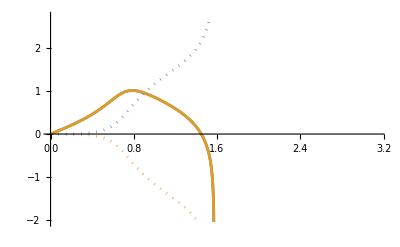

```mathematica
ReImPlot[{EllipticPi[2+1 ⅈ,χ,1],EllipticPi[2-1 ⅈ,χ,1]},{χ,0,π}]
```

```mathematica
Simplify@ComplexExpand@ReIm[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥))]
Simplify@ComplexExpand@ReIm[((r1-r2) (r3+ⅈ 𝒥))/((r1-r3) (r2+ⅈ 𝒥))]
```

{((r1-r2) (r2 r3+𝒥^2))/((r1-r3) (r2^2+𝒥^2)),-((r1-r2) (r2-r3) 𝒥)/((r1-r3) (r2^2+𝒥^2))}

{((r1-r2) (r2 r3+𝒥^2))/((r1-r3) (r2^2+𝒥^2)),((r1-r2) (r2-r3) 𝒥)/((r1-r3) (r2^2+𝒥^2))}

#### Conclusion of

```mathematica
Ψr0[χ_]:=(2  ℰ 𝒥)/(√(1-ℰ^2)√((r1-r3) (r2-r4))  (r2^2+𝒥^2) (r3^2+𝒥^2))( (r2-r3) 𝒥 (r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]]+r3^2 (r2^2+𝒥^2) EllipticF[χ,k0^2]+(r2-r3) (r2+r3) 𝒥^2 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]])/.{yr->Sin[χ]};
```

##### Latex

```mathematica
(2  ℰ 𝒥)/(√(1-ℰ^2)√((r1-r3) (r2-r4))  (r2^2+𝒥^2) (r3^2+𝒥^2))( (r2-r3) 𝒥 (r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]]+r3^2 (r2^2+𝒥^2) EllipticF[χ,k0^2]+(r2-r3) (r2+r3) 𝒥^2 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]])/.{r1->Subscript[r, 1],r2->Subscript[r, 2],r3->Subscript[r, 3],r4->Subscript[r, 4],rp->Subscript[r, p],rn->Subscript[r, n],k0->Subscript[k, 0]}
```

(2 ℰ 𝒥 (EllipticF[χ,k_0^2] (𝒥^2+r_2^2) r_3^2+𝒥^2 Re[EllipticPi[((r_1-r_2) (-ⅈ 𝒥+r_3))/((-ⅈ 𝒥+r_2) (r_1-r_3)),χ,k_0^2]] (r_2-r_3) (r_2+r_3)+𝒥 Im[EllipticPi[((r_1-r_2) (-ⅈ 𝒥+r_3))/((-ⅈ 𝒥+r_2) (r_1-r_3)),χ,k_0^2]] (r_2-r_3) (-𝒥^2+r_2 r_3)))/(√(1-ℰ^2) (𝒥^2+r_2^2) (𝒥^2+r_3^2) √((r_1-r_3) (r_2-r_4)))

(2 ℰ 𝒥)/(√(1-ℰ^2) (𝒥^2+r_2^2) (𝒥^2+r_3^2) √((r_1-r_3) (r_2-r_4))) (Re[EllipticF[χ,k_0^2]] (𝒥^2+r_2^2) r_3^2+𝒥^2 Re[EllipticPi[((r_1-r_2) (-ⅈ 𝒥+r_3))/((-ⅈ 𝒥+r_2) (r_1-r_3)),χ,k_0^2]] (r_2-r_3) (r_2+r_3)+𝒥 Im[EllipticPi[((r_1-r_2) (-ⅈ 𝒥+r_3))/((-ⅈ 𝒥+r_2) (r_1-r_3)),χ,k_0^2]] (r_2-r_3) (-𝒥^2+r_2 r_3))

## Frequency

### Conclusion of {ϒr,ϒt,ϒφ,ϒψ}

```mathematica
ϒr=2π/λr0[π]
ϒt=Map[Simplify[#]&,Collect[Simplify@(ϒr/(2π)Tr0[π]),{EllipticE[k0^2],EllipticK[k0^2],EllipticPi[hr,k0^2],EllipticPi[hrn,k0^2],EllipticPi[hrp,k0^2]}],{1}]
ϒφ=ϒr/(2π)Φr0[π]
ϒψ=Map[Simplify[#]&,Collect[Simplify@(ϒr/(2π)Ψr0[π]),{(r2-r3) ℰ 𝒥^2, EllipticK[k0^2]}],{1}]
```

(π √((r1-r3) (r2-r4)) √(1-ℰ^2))/(2 EllipticK[k0^2])

1/2 ((8-2 b+r1 (-r2+r3)+r3 (4+r2+r3)) ℰ+(2 ((-4+b) b ℰ-4 (-2+b) rp ℰ-b sp 𝒥+rp sp 𝒥))/((r3-rp) (-rn+rp))+(4 b^2 ℰ+2 rn (8 ℰ+sp 𝒥)-2 b (4 (2+rn) ℰ+sp 𝒥))/((r3-rn) (rn-rp)))+((r1-r3) (r2-r4) ℰ EllipticE[k0^2])/(2 EllipticK[k0^2])+1/(2 EllipticK[k0^2])(r2-r3) ((4+r1+r2+r3+r4) ℰ EllipticPi[(r1-r2)/(r1-r3),k0^2]+(2 (2 (-4+b) b ℰ-4 (-2+b) rn ℰ-b sp 𝒥+rn sp 𝒥) EllipticPi[((r1-r2) (r3-rn))/((r1-r3) (r2-rn)),k0^2])/((r2-rn) (-r3+rn) (rn-rp))+(2 ((-4+b) b ℰ-4 (-2+b) rp ℰ-b sp 𝒥+rp sp 𝒥) EllipticPi[((r1-r2) (r3-rp))/((r1-r3) (r2-rp)),k0^2])/((r2-rp) (-r3+rp) (-rn+rp)))

sp ℰ+𝒥

(r3^2 ℰ 𝒥)/(r3^2+𝒥^2)+((r2-r3) ℰ 𝒥^2 ((r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]+(r2+r3) 𝒥 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]))/((r2^2+𝒥^2) (r3^2+𝒥^2) EllipticK[k0^2])

### The Schwarzschild case

```mathematica
1/(2 EllipticK[k0^2])ℰ (r2 (r1-r3) EllipticE[k0^2]+(r1 (-r2+r3)+r3 (r2+(r3 (2+r3))/(-2+r3))) EllipticK[k0^2]+(r2-r3) (4+r1+r2+r3) EllipticPi[(r1-r2)/(r1-r3),k0^2]-(16 (r2-r3) EllipticPi[((r1-r2) (-2+r3))/((-2+r2) (r1-r3)),k0^2])/((-2+r2) (-2+r3))+(2 sp 𝒥 ((-2+r2) EllipticK[k0^2]+(-r2+r3) EllipticPi[((r1-r2) (-2+r3))/((-2+r2) (r1-r3)),k0^2]))/((-2+r2) (-2+r3) ℰ))==ϒt/.{r4->0,rn->0,rp->2,b->0}//Simplify
ϒφ/.{r4->0,rn->0,rp->2,b->0}//Simplify
(r3^2 ℰ 𝒥)/(r3^2+𝒥^2)+((r2-r3) ℰ 𝒥^2 ((r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]+(r2+r3) 𝒥 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]))/((r2^2+𝒥^2) (r3^2+𝒥^2) EllipticK[k0^2])==ϒψ/.{r4->0,rn->0,rp->2,b->0}//Expand//Simplify
```

True

sp ℰ+𝒥

True

### Latex

```mathematica
ϒt0==-rnIntCharge/(r3-rn)+rpIntCharge/(r3-rp)+1/2 (8-2 b+r1 (-r2+r3)+r3 (4+r2+r3)) ℰ+((r1-r3) (r2-r4) ℰ EllipticE[k0^2])/(2 EllipticK[k0^2])+(r2-r3)/(2 EllipticK[k0^2])((4+r1+r2+r3+r4) ℰ EllipticPi[hr,k0^2]+(2 rnIntCharge EllipticPi[hrn,k0^2])/((r2-rn) (r3-rn))+(2 rpIntCharge EllipticPi[hrp,k0^2])/((r2-rp) (-r3+rp)))/.{r1->Subscript[r, 1],r2->Subscript[r, 2],r3->Subscript[r, 3],r4->Subscript[r, 4],rp->Subscript[r, p],rn->Subscript[r, n],rpIntCharge->Subscript[ℐ, pC],rnIntCharge->Subscript[ℐ, nC],k0->k,hr->Subscript[h, r],hrn->Subscript[h, rn],hrp->Subscript[h, rp],EllipticE->Subscript[Ε, e],EllipticK->Subscript[K, e],EllipticPi->Subscript[Π, e]}
```

ϒt0==1/2 ℰ (8-2 b+r_1 (-r_2+r_3)+r_3 (4+r_2+r_3))-ℐ_nC/(r_3-r_n)+ℐ_pC/(r_3-r_p)+(ℰ (r_1-r_3) (r_2-r_4) Ε_e[k^2])/(2 K_e[k^2])+((r_2-r_3) (ℰ (4+r_1+r_2+r_3+r_4) Π_e[h_r,k^2]+(2 ℐ_nC Π_e[h_rn,k^2])/((r_2-r_n) (r_3-r_n))+(2 ℐ_pC Π_e[h_rp,k^2])/((r_2-r_p) (-r_3+r_p))))/(2 K_e[k^2])

1/2 ℰ (8-2 b+r_1 (-r_2+r_3)+r_3 (4+r_2+r_3))+(ℰ EllipticE[k^2] (r_1-r_3) (r_2-r_4))/(2 EllipticK[k^2])-ℐ_nC/(r_3-r_n)+ℐ_pC/(r_3-r_p)+1/(2 EllipticK[k^2])(r_2-r_3) (ℰ EllipticPi[h_r,k^2] (4+r_1+r_2+r_3+r_4)+(2 EllipticPi[h_rn,k^2] ℐ_nC)/((r_2-r_n) (r_3-r_n))+(2 EllipticPi[h_rp,k^2] ℐ_pC)/((r_2-r_p) (-r_3+r_p)))

```mathematica
ϒψ0==(r3^2 ℰ 𝒥)/(r3^2+𝒥^2)+((r2-r3) ℰ 𝒥^2)/((r2^2+𝒥^2) (r3^2+𝒥^2) EllipticK[k0^2])((r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]+(r2+r3) 𝒥 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]])/.{r1->Subscript[r, 1],r2->Subscript[r, 2],r3->Subscript[r, 3],r4->Subscript[r, 4],rp->Subscript[r, p],rn->Subscript[r, n],rpIntCharge->Subscript[ℐ, pC],rnIntCharge->Subscript[ℐ, nC],k0->k,hr->Subscript[h, r],hrn->Subscript[h, rn],hrp->Subscript[h, rp],EllipticE->Subscript[Ε, e],EllipticK->Subscript[K, e],EllipticPi->Subscript[Π, e]}
```

ϒψ0==(ℰ 𝒥 r_3^2)/(𝒥^2+r_3^2)+(ℰ 𝒥^2 (r_2-r_3) (𝒥 Re[Π_e[((r_1-r_2) (-ⅈ 𝒥+r_3))/((-ⅈ 𝒥+r_2) (r_1-r_3)),k^2]] (r_2+r_3)+Im[Π_e[((r_1-r_2) (-ⅈ 𝒥+r_3))/((-ⅈ 𝒥+r_2) (r_1-r_3)),k^2]] (-𝒥^2+r_2 r_3)))/((𝒥^2+r_2^2) (𝒥^2+r_3^2) K_e[k^2])

(ℰ 𝒥 r_3^2)/(𝒥^2+r_3^2)+(ℰ 𝒥^2 (r_2-r_3))/((𝒥^2+r_2^2) (𝒥^2+r_3^2) K_e[k0^2])(𝒥 Re[Π_e[((r_1-r_2) (-ⅈ 𝒥+r_3))/((-ⅈ 𝒥+r_2) (r_1-r_3)),k0^2]] (r_2+r_3)+Im[Π_e[((r_1-r_2) (-ⅈ 𝒥+r_3))/((-ⅈ 𝒥+r_2) (r_1-r_3)),k0^2]] (-𝒥^2+r_2 r_3))

## Linear shift to the orbital frequencies

### Initialize of ParamExactsb && ParamExactFS

```mathematica
ParamExactsb[spE_,snE_,eE_,pE_,bE_,ME_][Exp_]:=Module[{r0,r1E,r2E,r3E,r4E,rnE,rpE,k0E,hrE,hr32E,hrnE,hrpE,
A0,A1,A2,A3,K1,K2,K3,fEJ02sp,fJ02sp,fE02sp,
ℰ2Approxep,ℰ20,𝒥2Approxep,𝒥20,ℰE,𝒥E,qr0E,qt0E,qφ0E,qψ0E,k02E,
fShBW,f,XE,YE,ZE,WE,VE,UE},

XE=pE-3-eE^2;
YE=(pE-2)^2-4 eE^2;
ZE=1-eE^2;
WE=(pE^2 YE+2 bE pE (-2+pE+(2+pE) (1-ZE))+bE^2 ZE^2);
VE=pE XE-2 bE(-2+ZE);
UE=(bE-pE) (bE^2 pE+bE(-1+pE) pE^2-pE^3-bE^3 (-1+ZE));

r1E=r1b; 
r2E=r2b;


fShBW[r_]:=1-2 1/r+bE/r^2; 


ℰ2Approxep=ℰ2b+ spE ℰ2sb; 
𝒥2Approxep=𝒥2b+spE 𝒥2sb; 

ℰE=N[√ℰ2Approxep]; 
𝒥E=N[√𝒥2Approxep]; 
ℰE=√ℰ2Approxep; 
𝒥E=√𝒥2Approxep; 

A0=(bE ME^2 (4 spE ℰE 𝒥E+𝒥E^2))/(1-ℰE^2);
A1=(2 ME (3 spE ℰE 𝒥E+𝒥E^2))/(-1+ℰE^2);
A2=(bE ME^2+2 spE ℰE 𝒥E+𝒥E^2)/(1-ℰE^2);
A3=(2 ME)/(-1+ℰE^2);



r3E=(pE ((bE-pE)^2+√((bE-pE) (bE^2 pE+bE (-1+pE) pE^2-pE^3-bE^3 (-1+ZE)))) ZE)/(pE^2 VE-WE)+spE ((pE √((-bE+pE) WE) ZE^2 (pE^2+bE (-2 pE+ZE)))/((-pE^2 VE+WE)^2)+(√((-bE+pE) WE) ZE (2 pE^5+bE^2 pE^2 (16-pE (-2+ZE))+2 bE^3 pE (pE (-2+ZE)-3 ZE)+bE^4 ZE^2+2 bE pE^3 (-8-(-2+pE) pE+ZE)))/(2 (pE^2 VE-WE) √(-((bE-pE) (-bE^2 pE-bE (-1+pE) pE^2+pE^3+bE^3 (-1+ZE)))) (4 bE pE+(-4+pE) pE^2-bE^2 ZE)));
r4E=-(bE (bE-pE) pE)/((bE-pE)^2+√UE)+(bE spE (-pE^2 VE+WE)^2 (-(2 √(-bE+pE) ((bE-pE)^2+√UE) (2 (-2+pE) pE+bE ZE) √(bE^2 ZE^2-2 bE pE (pE (-2+ZE)+2 ZE)+pE^2 ((-4+pE) pE+4 ZE)))/(ZE^2 (-pE (4 bE+(-4+pE) pE)+bE^2 ZE)^3)-(((-bE+pE) WE)^(3/2) ((2 pE^5+bE^2 pE^2 (16-pE (-2+ZE))+2 bE^3 pE (pE (-2+ZE)-3 ZE)-2 bE pE^3 (8-2 pE+pE^2-ZE)+bE^4 ZE^2)/(√UE ZE (4 bE pE+(-4+pE) pE^2-bE^2 ZE)^2)+(2 pE ZE (pE^2+bE (-2 pE+ZE)))/((-pE^2 VE+WE)^2)))/((pE^2 VE-WE) WE)))/(2 ((bE-pE)^2+√UE)^2);

r3E=r3b+spE r3sb;
r4E=r4b+spE r4sb;



rnE=rnb; 
rpE=rpb;  
k0E=√((r1E-r2E)/(r1E-r3E)(r3E-r4E)/(r2E-r4E));  
hrE=(r1E-r2E)/(r1E-r3E); 
hr32E=(r1E-r2E)/(r1E-r3E)r3E/r2E; 
hrnE=(r1E-r2E)/(r1E-r3E)(r3E-rnE)/(r2E-rnE);  
hrpE=(r1E-r2E)/(r1E-r3E)(r3E-rpE)/(r2E-rpE); 

k02E=kb02+spE ks02;  
hrE=hbr+spE hsr; 
hr32E=hbr32+spE hsr32; 
hrnE=hbrn+spE hsrn;  
hrpE=hbrp+spE hsrp; 

qr0E=0;qt0E=0;qφ0E=0;qψ0E=π;

Exp/.{sn->snE,sp->spE,e->eE,p->pE,b->bE,M->ME,r1->r1E,r2->r2E,r3->r3E,r4->r4E,rn->rnE,rp->rpE,k0^2->k02E,hr->hrE,hr32->hr32E,hrp->hrpE,hrn->hrnE,ℰ->ℰE,𝒥->𝒥E,qr0->qr0E,qt0->qt0E,qφ0->qφ0E,qψ0->qψ0E}]
```

```mathematica
ParamExactFS[spE_,snE_,eE_,pE_,bE_,ME_][Exp_]:=Module[{r0,r1E,r2E,r3E,r4E,r3bE,r3sbE,r4bE,r4sbE,rnE,rpE,k0E,hrE,hr32E,hrnE,hrpE,
A0,A1,A2,A3,K1,K2,K3,fEJ02sp,fJ02sp,fE02sp,k02E,kb02E,ks02E,
ℰ2Approxep,ℰ20,𝒥2Approxep,𝒥20,ℰ2bE,ℰ2sbE,𝒥2bE,𝒥2sbE,ℰE,𝒥E,qr0E,qt0E,qφ0E,qψ0E,
fShBW,f,XE,YE,ZE,WE,VE,UE},

XE=pE-3-eE^2;
YE=(pE-2)^2-4 eE^2;
ZE=1-eE^2;
WE=(pE^2 YE+2 bE pE (-2+pE+(2+pE) (1-ZE))+bE^2 ZE^2);
VE=pE XE-2 bE(-2+ZE);
UE=(bE-pE) (bE^2 pE+bE(-1+pE) pE^2-pE^3-bE^3 (-1+ZE));

r1E=pE/(1-eE); 
r2E=pE/(1+eE);


fShBW[r_]:=1-2 1/r+bE/r^2; 


(*
ℰ2Approxep=(pE^2 YE+bE^2 ZE^2-2 bE pE (pE (-2+ZE)+2 ZE))/(pE^2 (pE XE-2 bE (-2+ZE)))+(spE ZE^2 √(-((bE-pE) (pE^2 (4 bE+YE)-2 bE pE (2+pE) ZE+bE^2 ZE^2))) (pE^2+bE (-2 pE+ZE)))/(pE^3 (pE XE-2 bE (-2+ZE))^2); 
𝒥2Approxep=(pE^2 (-bE+pE))/(pE XE+2 bE (2-ZE))+(spE (pE (9-2 pE+3 (1-ZE))-8 bE (2-ZE)) √((-bE+pE) (pE^2 YE+2 bE pE (-2+pE+(2+pE) (1-ZE))+bE^2 ZE^2)))/(pE XE+2 bE (2-ZE))^2; 
*) 


ℰ2bE=(pE^2 YE+bE^2 ZE^2-2 bE pE (pE (-2+ZE)+2 ZE))/(pE^2 (pE XE-2 bE (-2+ZE)));
ℰ2sbE=(ZE^2 √(-((bE-pE) (pE^2 (4 bE+YE)-2 bE pE (2+pE) ZE+bE^2 ZE^2))) (pE^2+bE (-2 pE+ZE)))/(pE^3 (pE XE-2 bE (-2+ZE))^2);
𝒥2bE=(pE^2 (-bE+pE))/(pE XE+2 bE (2-ZE));

𝒥2sbE=((pE (9-2 pE+3 (1-ZE))-8 bE (2-ZE)) √((-bE+pE) (pE^2 YE+2 bE pE (-2+pE+(2+pE) (1-ZE))+bE^2 ZE^2)))/(pE XE+2 bE (2-ZE))^2;

ℰ2Approxep=ℰ2bE+ spE ℰ2sbE; 
𝒥2Approxep=𝒥2bE+spE 𝒥2sbE; 



ℰE=N[√ℰ2Approxep]; 
𝒥E=N[√𝒥2Approxep]; 
ℰE=√ℰ2Approxep; 
𝒥E=√𝒥2Approxep; 

A0=(bE ME^2 (4 spE ℰE 𝒥E+𝒥E^2))/(1-ℰE^2);
A1=(2 ME (3 spE ℰE 𝒥E+𝒥E^2))/(-1+ℰE^2);
A2=(bE ME^2+2 spE ℰE 𝒥E+𝒥E^2)/(1-ℰE^2);
A3=(2 ME)/(-1+ℰE^2);


(*
r3E=+spE ();
r4E=+spE  ;
*) 

r3bE=(pE ((bE-pE)^2+√((bE-pE) (bE^2 pE+bE (-1+pE) pE^2-pE^3-bE^3 (-1+ZE)))) ZE)/(pE^2 VE-WE);
r3sbE=((pE √((-bE+pE) WE) ZE^2 (pE^2+bE (-2 pE+ZE)))/((-pE^2 VE+WE)^2)+(√((-bE+pE) WE) ZE (2 pE^5+bE^2 pE^2 (16-pE (-2+ZE))+2 bE^3 pE (pE (-2+ZE)-3 ZE)+bE^4 ZE^2+2 bE pE^3 (-8-(-2+pE) pE+ZE)))/(2 (pE^2 VE-WE) √(-((bE-pE) (-bE^2 pE-bE (-1+pE) pE^2+pE^3+bE^3 (-1+ZE)))) (4 bE pE+(-4+pE) pE^2-bE^2 ZE)));
r4bE=(bE (bE-pE) pE)/((bE-pE)^2+√UE);
r4sbE=(bE (-pE^2 VE+WE)^2 (-(2 √(-bE+pE) ((bE-pE)^2+√UE) (2 (-2+pE) pE+bE ZE) √(bE^2 ZE^2-2 bE pE (pE (-2+ZE)+2 ZE)+pE^2 ((-4+pE) pE+4 ZE)))/(ZE^2 (-pE (4 bE+(-4+pE) pE)+bE^2 ZE)^3)-(((-bE+pE) WE)^(3/2) ((2 pE^5+bE^2 pE^2 (16-pE (-2+ZE))+2 bE^3 pE (pE (-2+ZE)-3 ZE)-2 bE pE^3 (8-2 pE+pE^2-ZE)+bE^4 ZE^2)/(√UE ZE (4 bE pE+(-4+pE) pE^2-bE^2 ZE)^2)+(2 pE ZE (pE^2+bE (-2 pE+ZE)))/((-pE^2 VE+WE)^2)))/((pE^2 VE-WE) WE)))/(2 ((bE-pE)^2+√UE)^2);
r3E=r3bE+spE r3sbE;
r4E=r4bE+spE r4sbE;



rnE=1-√(1-bE); 
rpE=1+√(1-bE);  
k0E=√((r1E-r2E)/(r1E-r3E)(r3E-r4E)/(r2E-r4E));  
hrE=(r1E-r2E)/(r1E-r3E); 
hr32E=(r1E-r2E)/(r1E-r3E)r3E/r2E; 
hrnE=(r1E-r2E)/(r1E-r3E)(r3E-rnE)/(r2E-rnE);  
hrpE=(r1E-r2E)/(r1E-r3E)(r3E-rpE)/(r2E-rpE); 

qr0E=0;qt0E=0;qφ0E=0;qψ0E=π;

kb02E=(r1E-r2E)/(r1E-r3bE)(r3bE-r4bE)/(r2E-r4bE); 
ks02E=((r1E-r2E) (r3sbE (r1E-r4bE) (r2E-r4bE)+(r1E-r3bE) (-r2E+r3bE) r4sbE))/((r1E-r3bE)^2 (r2E-r4bE)^2);  


Exp/.{sn->snE,sp->spE,e->eE,p->pE,b->bE,M->ME,r1->r1E,r2->r2E,r3->r3E,r4->r4E,r1b->r1E,r2b->r2E,r3b->r3bE,r3sb->r3sbE,r4b->r4bE,r4sb->r4sbE,
rn->rnE,rp->rpE,rnb->rnE,rpb->rpE,k0->k0E,kb02->kb02E,ks02->ks02E,hr->hrE,hr32->hr32E,hrp->hrpE,hrn->hrnE,ℰ->ℰE,𝒥->𝒥E,ℰ2b->ℰ2bE,ℰ2sb->ℰ2sbE,𝒥2b->𝒥2bE,𝒥2sb->𝒥2sbE,qr0->qr0E,qt0->qt0E,qφ0->qφ0E,qψ0->qψ0E}]
```

### Correction of frequencies for r

#### Calculation process

```mathematica
ϒr=(π √((r1-r3) (r2-r4)) √(1-ℰ^2))/(2 EllipticK[k0^2]);
```

```mathematica
ParamExactsb[sp,sn,e,p,b,M]@ϒr
Iconize[Evaluate[ParamExactsb[sp,sn,e,p,b,M]@ϒr/.{sp->0}],"ϒrb"]
Iconize[Evaluate[D[ParamExactsb[sp,sn,e,p,b,M]@ϒr ,sp]/.{sp->0}/.{kb0->kb,ks0->ks}],"ϒrsp"]
```

(π √((r1b-r3b-r3sb sp) (r2b-r4b-r4sb sp)) √(1-ℰ2b-sp ℰ2sb))/(2 EllipticK[kb02+ks02 sp])

#### Conclusion

```mathematica
ϒrb=;
ϒrsp=;
```

#### Latex

```mathematica
ϒrb/.{r1b->Subscript[r, b1],r2b->Subscript[r, b2],r3b->Subscript[r, b3],r4b->Subscript[r, b4],kb->Subscript[k, b],ks02->Subscript[k, s]^2,ℰ2b->Subscript[ℰ, b]^2}
ϒrsp/.{r1b->Subscript[r, b1],r2b->Subscript[r, b2],r3b->Subscript[r, b3],r4b->Subscript[r, b4],r3sb->Subscript[r, s3],r4sb->Subscript[r, s4],kb->Subscript[k, b],ks02->Subscript[k, s]^2,kb02->Subscript[k, b]^2,ℰ2b->Subscript[ℰ, b]^2,ℰ2sb->Subscript[ℰ, s]^2}
```

(π √((r_b1-r_b3) (r_b2-r_b4)) √(1-ℰ_b^2))/(2 EllipticK[kb02])

-(π (EllipticE[k_b^2]-EllipticK[k_b^2] (1-k_b^2)) k_s^2 √((r_b1-r_b3) (r_b2-r_b4)) √(1-ℰ_b^2))/(4 EllipticK[k_b^2]^2 k_b^2 (1-k_b^2))+(π (-((r_b2-r_b4) r_s3)-(r_b1-r_b3) r_s4) √(1-ℰ_b^2))/(4 EllipticK[k_b^2] √((r_b1-r_b3) (r_b2-r_b4)))-(π √((r_b1-r_b3) (r_b2-r_b4)) ℰ_s^2)/(4 EllipticK[k_b^2] √(1-ℰ_b^2))

#### The Schwarzschild case

```mathematica
ParamExactFS[sp,sn,e,p,0,1]@kb02//Simplify;
FullSimplify[%,Assumptions->p>0&&-3-e^2+p>0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]
```

(4 e)/(-6+2 e+p)

```mathematica
ParamExactFS[sp,sn,e,p,0,1]@ϒrb;
FullSimplify[%,Assumptions->p>0&&-3-e^2+p>0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]

ParamExactFS[sp,sn,e,p,0,1]@ϒrsp;
FullSimplify[%,Assumptions->p>0&&3+e^2-p<0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]
```

(√((p (-6+2 e+p))/(-3-e^2+p)) π)/(2 EllipticK[(4 e)/(-6+2 e+p)])

-(√((-4 e^2+(-2+p)^2) (-6+2 e+p) (-3-e^2+p)) π ((3+e^2-p) EllipticE[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticK[(4 e)/(-6+2 e+p)]))/(4 (6+2 e-p) (3+e^2-p)^2 EllipticK[(4 e)/(-6+2 e+p)]^2)

### Correction of frequencies for t

#### Calculation process

```mathematica
ϒt=1/2 ((8-2 b+r1 (-r2+r3)+r3 (4+r2+r3)) ℰ+(2 ((-4+b) b ℰ-4 (-2+b) rp ℰ-b sp 𝒥+rp sp 𝒥))/((r3-rp) (-rn+rp))+(4 b^2 ℰ+2 rn (8 ℰ+sp 𝒥)-2 b (4 (2+rn) ℰ+sp 𝒥))/((r3-rn) (rn-rp)))+((r1-r3) (r2-r4) ℰ EllipticE[k0^2])/(2 EllipticK[k0^2])+1/(2 EllipticK[k0^2])(r2-r3) ((4+r1+r2+r3+r4) ℰ EllipticPi[hr,k0^2]+(2 (2 (-4+b) b ℰ-4 (-2+b) rn ℰ-b sp 𝒥+rn sp 𝒥) EllipticPi[hrn,k0^2])/((r2-rn) (-r3+rn) (rn-rp))+(2 ((-4+b) b ℰ-4 (-2+b) rp ℰ-b sp 𝒥+rp sp 𝒥) EllipticPi[hrp,k0^2])/((r2-rp) (-r3+rp) (-rn+rp)));
```

```mathematica
ParamExactsb[sp,sn,e,p,b,M]@ϒt;
Iconize[ParamExactsb[sp,sn,e,p,b,M]@ϒt/.{sp->0}//Simplify,"ϒtb"]
Iconize[D[ParamExactsb[sp,sn,e,p,b,M]@ϒt,sp]/.{sp->0}/.{kb0->kb,ks0->ks}//Simplify,"ϒtsp"]
```

#### Conclusion

```mathematica
Υtb=;
Υtsp=;
```

#### The Schwarzschild case

```mathematica
ParamExactFS[sp,sn,e,p,0,1]@Υtb;
Simplify[%,Assumptions->p>0&&-3-e^2+p>0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]

ParamExactFS[sp,sn,e,p,0,1]@Υtsp;
Simplify[%,Assumptions->p>0&&3+e^2-p<0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]
```

(p (4-((6+2 e-p) ((-1+e) √(-3-e^2+p) Im[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]]+(3+e^2-p) Re[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]]))/((3+e^2-p) EllipticK[(4 e)/(-6+2 e+p)])))/(√((-4 e^2+(-2+p)^2) p))

Simplify::time: 在变换上花的时间超过了 300. 秒，退出变换. 增加 TimeConstraint 选项的值可能改善化简结果.

General::stop: 在本次计算中，Simplify::time 的进一步输出将被抑制.

1/4 (-(-4 e^2+(-2+p)^2)/(√(-3-e^2+p))-(8 (-4 e^2+(-2+p)^2) (-8-4 e^2 (-2+p)+p^2))/((-1+e^2) (-4+p)^3 √(-3-e^2+p))+((-4+p) (4 (-1+e^2)^2+p^2 (-3-e^2+p)))/(2 p (-3-e^2+p)^(3/2))+((-1+e) (1+e) (-128+96 p+12 p^2-12 p^3+p^4+4 e^2 (32-24 p+5 p^2)))/((-4+p)^2 p (-3-e^2+p)^(3/2))-((-1+e) (1+e) p (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/((-4+p) (-3-e^2+p)^(3/2) EllipticK[(4 e)/(-6+2 e+p)])-(4 (-4 e^2+(-2+p)^2) p EllipticE[(4 e)/(-6+2 e+p)])/((1+e) (-4+p)^2 √(-3-e^2+p) EllipticK[(4 e)/(-6+2 e+p)])-((-4 e^2+(-2+p)^2) p (EllipticE[(4 e)/(-6+2 e+p)]-EllipticK[(4 e)/(-6+2 e+p)]))/((-1+e) (1+e) (-4+p) √(-3-e^2+p) EllipticK[(4 e)/(-6+2 e+p)])-((-4 e^2+(-2+p)^2) p EllipticE[(4 e)/(-6+2 e+p)] ((-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)]+(6+2 e-p) EllipticK[(4 e)/(-6+2 e+p)]))/((-1+e) (1+e) (6+2 e-p) (-4+p) √(-3-e^2+p) EllipticK[(4 e)/(-6+2 e+p)]^2)-(4 (-4 e^2+(-2+p)^2) ((2 (8+p-p^2+e^2 (-8+3 p)) EllipticPi[hbr,(4 e)/(-6+2 e+p)])/((-1+e) (1+e) (-4+p))+(2 (1+e) (-4+p) EllipticPi[hbrp,(4 e)/(-6+2 e+p)])/(2+2 e-p)))/((-4+p)^2 √(-3-e^2+p) EllipticK[(4 e)/(-6+2 e+p)])+((-1+e^2) (-4 e^2+(-2+p)^2) (-6-2 e+p) (EllipticE[(4 e)/(-6+2 e+p)]+((6+2 e-p) EllipticK[(4 e)/(-6+2 e+p)])/(-6+2 e+p)) ((2 (8+p-p^2+e^2 (-8+3 p)) EllipticPi[hbr,(4 e)/(-6+2 e+p)])/((-1+e) (1+e) (-4+p))+(2 (1+e) (-4+p) EllipticPi[hbrp,(4 e)/(-6+2 e+p)])/(2+2 e-p)))/((-1+e) (1+e)^2 (6+2 e-p) (-4+p) √(-3-e^2+p) EllipticK[(4 e)/(-6+2 e+p)]^2)+1/((1+e) (-4+p) EllipticK[(4 e)/(-6+2 e+p)])p (-6-2 e+p) ((4 (-4 e^2+(-2+p)^2) EllipticPi[hbr,(4 e)/(-6+2 e+p)])/((-4+p)^2 √(-3-e^2+p))+(2 (-1+e) (1+e) (8+p-p^2+e^2 (-8+3 p)) EllipticPi[hbr,(4 e)/(-6+2 e+p)])/((-4+p) p (-3-e^2+p)^(3/2))+(2 (8+p-p^2+e^2 (-8+3 p)) (-1/((-1+hbr) hbr)hsr √p (hbr (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)]-(2 e (-2+hbr)+hbr (-6+p)) EllipticK[(4 e)/(-6+2 e+p)]+(2 e (-2+hbr^2)+hbr^2 (-6+p)) EllipticPi[hbr,(4 e)/(-6+2 e+p)])+(4 e √(-4 e^2+(-2+p)^2) ((-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)]+(6+2 e-p) EllipticPi[hbr,(4 e)/(-6+2 e+p)]))/((6+2 e-p) (-6+2 e+p))))/((-1+e) (1+e) (2 e (-2+hbr)+hbr (-6+p)) (-4+p) √((p^2 (-3-e^2+p))/(-4 e^2+(-2+p)^2)))+((1+e) (-2+2 e+p) EllipticPi[hbrp,(4 e)/(-6+2 e+p)])/(√(-3-e^2+p))+((1+e) (-4+p) (2+2 e^3+e^2 (-2+p)+p-p^2-2 e (1+p)) EllipticPi[hbrp,(4 e)/(-6+2 e+p)])/(2 p (-3-e^2+p)^(3/2))+(2 (1+e) (-4+p) √((-4 e^2+(-2+p)^2)/(p (-3-e^2+p))) (hbrp (-4+p) (-6+2 e+p) (-4 e (-1+hbrp) √(-4 e^2+(-2+p)^2) p^(11/2)-hsrp (-4 e^2+(-6+p)^2) p^6) EllipticE[(4 e)/(-6+2 e+p)]+(6+2 e-p) (hsrp (2 e (-2+hbrp)+hbrp (-6+p)) (4-p) p^6 (-6+2 e+p) EllipticK[(4 e)/(-6+2 e+p)]+(-4+p) (4 e (-1+hbrp) (-hbrp √(-4 e^2+(-2+p)^2)+(1+hbrp) hsrp (-6+p) √p) p^(11/2)+4 e^2 (-2+hbrp^2) hsrp p^6+hbrp^2 hsrp (-6+p)^2 p^6) EllipticPi[hbrp,(4 e)/(-6+2 e+p)])))/((-1+hbrp) hbrp (2 e (-2+hbrp)+hbrp (-6+p)) (4-p) (2+2 e-p) (6+2 e-p) p^6 (-6+2 e+p))))

### Correction of frequencies for φ

#### Calculation process

```mathematica
ϒφ=sp ℰ+𝒥;
```

```mathematica
ParamExactsb[sp,sn,e,p,b,M]@(sp ℰ+𝒥)
FullSimplify[Series[%,{sp,0,1}]]

√𝒥2b /.{r1b->Subscript[r, b1],r2b->Subscript[r, b2],r3b->Subscript[r, b3],r4b->Subscript[r, b4],r3sb->Subscript[r, s3],r4sb->Subscript[r, s4],kb->Subscript[k, b],ℰ2b->Subscript[ℰ, b]^2,ℰ2sb->Subscript[ℰ, s]^2,𝒥2b->Subscript[𝒥, b]^2,𝒥2sb->Subscript[𝒥, s]^2}

(√ℰ2b+𝒥2sb/(2 √𝒥2b)) /.{r1b->Subscript[r, b1],r2b->Subscript[r, b2],r3b->Subscript[r, b3],r4b->Subscript[r, b4],r3sb->Subscript[r, s3],r4sb->Subscript[r, s4],kb->Subscript[k, b],ℰ2b->Subscript[ℰ, b]^2,ℰ2sb->Subscript[ℰ, s]^2,𝒥2b->Subscript[𝒥, b]^2,𝒥2sb->Subscript[𝒥, s]^2}


ParamExactsb[sp,sn,e,p,b,M]@ϒφ;
ϒφb=ParamExactsb[sp,sn,e,p,b,M]@ϒφ/.{sp->0}//Simplify
ϒφsp=D[ParamExactsb[sp,sn,e,p,b,M]@ϒφ,sp]/.{sp->0}/.{kb0->kb,ks0->ks}//Simplify
```

sp √(ℰ2b+sp ℰ2sb)+√(𝒥2b+sp 𝒥2sb)

√𝒥2b+(√ℰ2b+𝒥2sb/(2 √𝒥2b)) sp+O[sp]^2

√(𝒥_b^2)

√(ℰ_b^2)+𝒥_s^2/(2 √(𝒥_b^2))

√𝒥2b

√ℰ2b+𝒥2sb/(2 √𝒥2b)

#### Conclusion

```mathematica
ϒφb=√𝒥2b;
ϒφsp=√ℰ2b+𝒥2sb/(2 √𝒥2b);
```

#### The Schwarzschild case

```mathematica
ParamExactFS[sp,sn,e,p,0,1]@√𝒥2b;
FullSimplify[%,Assumptions->p>0&&3+e^2-p<0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]

ParamExactFS[sp,sn,e,p,0,1]@(√ℰ2b+𝒥2sb/(2 √𝒥2b));
FullSimplify[%,Assumptions->3+e^2-p<0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0&&p>0]
```

p/(√(-3-e^2+p))

((3+e^2) √(-4+(4-4 e^2)/p+p))/(2 (-3-e^2+p)^(3/2))

### Correction of frequencies for ψ

#### Calculation process

```mathematica
ϒψ=(r3^2 ℰ 𝒥)/(r3^2+𝒥^2)+((r2-r3) ℰ 𝒥^2 ((r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]+(r2+r3) 𝒥 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]))/((r2^2+𝒥^2) (r3^2+𝒥^2) EllipticK[k0^2]);
```

```mathematica
ParamExactsb[sp,sn,e,p,b,M]@ϒψ;
ϒψb=ParamExactsb[sp,sn,e,p,b,M]@ϒψ/.{sp->0}//Simplify
```

(√ℰ2b √𝒥2b (r3b^2+((r2b-r3b) √𝒥2b ((r2b r3b-𝒥2b) Im[EllipticPi[((r1b-r2b) (r3b-ⅈ √𝒥2b))/((r1b-r3b) (r2b-ⅈ √𝒥2b)),kb02]]+(r2b+r3b) √𝒥2b Re[EllipticPi[((r1b-r2b) (r3b-ⅈ √𝒥2b))/((r1b-r3b) (r2b-ⅈ √𝒥2b)),kb02]]))/((r2b^2+𝒥2b) EllipticK[kb02])))/(r3b^2+𝒥2b)

```mathematica
ϒψb/.{r1b->Subscript[r, b1],r2b->Subscript[r, b2],r3b->Subscript[r, b3],r4b->Subscript[r, b4],r3sb->Subscript[r, s3],r4sb->Subscript[r, s4],kb->Subscript[k, b],ks02->Subscript[k, s]^2,kb02->Subscript[k, b]^2,ℰ2b->Subscript[ℰ, b]^2,ℰ2sb->Subscript[ℰ, s]^2}
```

(√𝒥2b (r_b3^2+(√𝒥2b (r_b2-r_b3) (√𝒥2b Re[EllipticPi[((r_b1-r_b2) (-ⅈ √𝒥2b+r_b3))/((-ⅈ √𝒥2b+r_b2) (r_b1-r_b3)),k_b^2]] (r_b2+r_b3)+Im[EllipticPi[((r_b1-r_b2) (-ⅈ √𝒥2b+r_b3))/((-ⅈ √𝒥2b+r_b2) (r_b1-r_b3)),k_b^2]] (-𝒥2b+r_b2 r_b3)))/(EllipticK[k_b^2] (𝒥2b+r_b2^2))) √(ℰ_b^2))/(𝒥2b+r_b3^2)

#### The Schwarzschild case

```mathematica
ParamExactFS[sp,sn,e,p,0,1]@ϒψb;
FullSimplify[%,Assumptions->p>0&&-3-e^2+p>0&&3+e^2-p<0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]
```

(p (4-((6+2 e-p) ((-1+e) √(-3-e^2+p) Im[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]]+(3+e^2-p) Re[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]]))/((3+e^2-p) EllipticK[(4 e)/(-6+2 e+p)])))/(√((-4 e^2+(-2+p)^2) p))

### Conclusion of (116)-(117)

```mathematica
Series[2π((ϒφb0+sp ϒφsp0)/(ϒrb0+sp ϒrsp0)-1),{sp,0,1}]
```

2 π (-1+ϒφb0/ϒrb0)+(2 π (-ϒrsp0 ϒφb0+ϒrb0 ϒφsp0) sp)/ϒrb0^2+O[sp]^2

```mathematica
νnodal=2π(ϒφb/ϒψb-1)
νperi=2 π (-1+ϒφb/ϒrb)
δνperi=(2 π (-ϒrsp ϒφb+ϒrb ϒφsp))/ϒrb^2
```

2 π (-1+(r3b^2+𝒥2b)/(√ℰ2b (r3b^2+((r2b-r3b) √𝒥2b ((r2b r3b-𝒥2b) Im[EllipticPi[((r1b-r2b) (r3b-ⅈ √𝒥2b))/((r1b-r3b) (r2b-ⅈ √𝒥2b)),kb02]]+(r2b+r3b) √𝒥2b Re[EllipticPi[((r1b-r2b) (r3b-ⅈ √𝒥2b))/((r1b-r3b) (r2b-ⅈ √𝒥2b)),kb02]]))/((r2b^2+𝒥2b) EllipticK[kb02]))))

2 π (-1+(2 √𝒥2b EllipticK[kb02])/(π √((r1b-r3b) (r2b-r4b)) √(1-ℰ2b)))

1/(π (r1b-r3b) (r2b-r4b) (1-ℰ2b))8 EllipticK[kb02]^2 ((π √((r1b-r3b) (r2b-r4b)) √(1-ℰ2b) (√ℰ2b+𝒥2sb/(2 √𝒥2b)))/(2 EllipticK[kb02])+√𝒥2b (-(π (-r3sb (r2b-r4b)-(r1b-r3b) r4sb) √(1-ℰ2b))/(4 √((r1b-r3b) (r2b-r4b)) EllipticK[kb02])+(π √((r1b-r3b) (r2b-r4b)) ℰ2sb)/(4 √(1-ℰ2b) EllipticK[kb02])+(ks02 π √((r1b-r3b) (r2b-r4b)) √(1-ℰ2b) (EllipticE[kb02]-(1-kb02) EllipticK[kb02]))/(4 (1-kb02) kb02 EllipticK[kb02]^2)))

#### The Schwarzschild case

```mathematica
ParamExactFS[sp,sn,e,p,0,1]@νnodal;
FullSimplify[%,Assumptions->p>0&&-3-e^2+p>0&&3+e^2-p<0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]
```

2 π (-1+(p √((-4 e^2+(-2+p)^2)/(p (-3-e^2+p))))/(4-((6+2 e-p) ((-1+e) √(-3-e^2+p) Im[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]]+(3+e^2-p) Re[EllipticPi[(2 e (-4+p+2 ⅈ √(-3-e^2+p)))/((-6+2 e+p) (1+e+ⅈ √(-3-e^2+p))),(4 e)/(-6+2 e+p)]]))/((3+e^2-p) EllipticK[(4 e)/(-6+2 e+p)])))

```mathematica
ParamExactFS[sp,sn,e,p,0,1]@νperi;
FullSimplify[%,Assumptions->p>0&&-3-e^2+p>0&&3+e^2-p<0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]
```

2 (-π+(2 p EllipticK[(4 e)/(-6+2 e+p)])/(√(p (-6+2 e+p))))

```mathematica
ParamExactFS[sp,sn,e,p,0,1]@δνperi;
FullSimplify[%,Assumptions->p>0&&-3-e^2+p>0&&3+e^2-p<0&&-6+2 e+p>0&&(1-e^2) (-4 e^2+(-2+p)^2)>0]
```

-(2 √((-4 e^2+(-2+p)^2)/(-6+2 e+p)) (p EllipticE[(4 e)/(-6+2 e+p)]+(6+2 e-p) EllipticK[(4 e)/(-6+2 e+p)]))/((6+2 e-p) p)

## Orbit

### Initialize of Orbit and ParamExactBW

```mathematica
qr[λ_]:=ϒr λ + qr0;
qt[λ_]:=ϒt λ + qt0;
qφ[λ_]:=ϒφ λ + qφ0;
qψ[λ_]:=ϒψ λ + qψ0;
```

```mathematica
r0λ[λ_]:=(r2 (-r1+r3)+(r1-r2) r3 (Sin@JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2])^2)/(-r1+r3+(r1-r2) (Sin@JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2])^2);
t0[λ_]:=qt[λ]+Tr0[JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2]]-Tr0[π]/(2π)qr[λ];
φ0[λ_]:=qφ[λ]+Φr0[JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2]]-Φr0[π]/(2π)qr[λ];
ψ0[λ_]:=qψ[λ]+Ψr0[JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2]]-Ψr0[π]/(2π)qr[λ];
θ0[λ_]:=π/2+(√(sn^2)√(r0λ[λ]^2+𝒥^2))/(r0λ[λ] 𝒥) Sin[ψ0[λ]];
```

```mathematica
Clear[{spA,snA,eA,pA,bA,MA}]
Iconize[ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Cos[φ0[λ]],r0λ[λ] Sin[φ0[λ]]},"Orbit"]

Iconize[(2 π)/(ParamExactBW[spA,snA,eA,pA,bA,MA][ParamExactBW[spA,snA,eA,pA,bA,MA][ϒr]]),"Period of r"]
Iconize[ParamExactBW[spA,snA,eA,pA,bA,MA][r2],"r_2"]

Iconize[2 π/ParamExactBW[spA,snA,eA,pA,bA,MA]@ϒψ,"Period of  ψ"]
```

### Fig

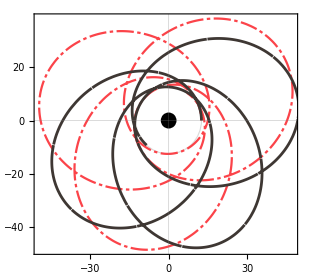

```mathematica
{spA,snA,eA,pA,bA,MA}={3/10,3/10,6/10,20,0,1};
FigAnalyse=ParametricPlot[,{λ,0,3},PlotLegends->{None},
PlotStyle->MyStyle[[1]],
PlotTheme->"Detailed",
FrameLabel->{Style["r cos[φ]",Bold,16,FontFamily->"Times"],Style["r sin[φ]",Bold,16,FontFamily->"Times"]},
FrameStyle->Directive[Black,15]];

{spA,snA,eA,pA,bA,MA}={3/10,3/10,6/10,20,-30/10,1};
FigAnalyse2=ParametricPlot[,{λ,0,3},PlotLegends->{None},PlotStyle->MyStyle[[2]],PlotTheme->"Scientific",
Prolog->{LightGray,Disk[{0,0},(6+2 eA + 3 bA/2 +2 √(2/3)spA)/(1 + eA)],Black,Disk[{0,0},1+√(1-bA)],{FaceForm[],EdgeForm[LightGray],Disk[{0,0},]}}];
FigOrbitbxy=Show@{FigAnalyse2, FigAnalyse}
```

```mathematica
{spA,snA,eA,pA,bA,MA}={3/10,3/10,3/10,10,0,1};
FigAnalyse=ParametricPlot[,{λ,0,},PlotRange->{{-15,15},{-15,15}},PlotLegends->{None},
Prolog->{LightGray,Disk[{0,0},(6+2 eA + 3 bA/2 +2 √(2/3)spA)/(1 + eA)],Black,Disk[{0,0},2],{FaceForm[],EdgeForm[LightGray],Disk[{0,0},]}},
PlotStyle->MyStyle[[1]],
PlotTheme->"Detailed",
FrameLabel->{Style["r cos[φ]",Bold,16,FontFamily->"Times"],Style["r sin[φ]",Bold,16,FontFamily->"Times"]},
FrameStyle->Directive[Black,15]];
PointOrbit1=Graphics@{PointSize[Medium],MyColor3,Point[/.{λ->0}],
PointSize[Medium],MyColor1,Point[/.{λ->}]};
{spA,snA,eA,pA,bA,MA}={3/10,3/10,3/10,10,3/10,1};
FigAnalyse2=ParametricPlot[,{λ,0,},PlotLegends->{None},PlotStyle->MyStyle[[2]],PlotTheme->"Scientific"];
PointOrbit2=Graphics@{PointSize[Medium],MyColor2,Point[/.{λ->}]};
FigOrbitbxy=Show@{FigAnalyse, FigAnalyse2,PointOrbit1,PointOrbit2}
```

-Graphics-

```mathematica
{spA,snA,eA,pA,bA,MA}={3/10,3/10,3/10,10,0,1};
FigAnalyse=ParametricPlot[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}},{λ,0,},
PlotRange->{{7.5,15},{-1.5,1}},
PlotStyle->MyStyle[[1]],
PlotLegends->Placed[{Style["b=0",16,FontFamily->"Times"]},Below],
PlotTheme->"Detailed",
FrameLabel->{Style["r sin[θ]",Bold,16,FontFamily->"Times"],Style["r cos[θ]",Bold,16,FontFamily->"Times"]},
FrameStyle->Directive[Black,15]];
PointOrbit1=Graphics@{PointSize[Medium],MyColor3,Point[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}}/.{λ->0}],
PointSize[Medium],MyColor1,Point[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}}/.{λ->}]};

{spA,snA,eA,pA,bA,MA}={3/10,3/10,3/10,10,3/10,1};
FigAnalyse2=ParametricPlot[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}},{λ,0,},PlotStyle->MyStyle[[2]],
PlotLegends->Placed[{Style["b=0.3",16,FontFamily->"Times"]},Below],PlotStyle->MyStyle[[2]],PlotTheme->"Scientific"];
PointOrbit2=Graphics@{PointSize[Medium],MyColor2,Point[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}}/.{λ->}]};


FigOrbitbxz=Show@{FigAnalyse, FigAnalyse2,PointOrbit1,PointOrbit2}
```

-Graphics-

```mathematica
{spA,snA,eA,pA,bA,MA}={0/10,0,3/10,10,3/10,1};
FigAnalyse=ParametricPlot[,{λ,0,},PlotRange->{{-15,15},{-15,15}},PlotLegends->{None},
Prolog->{LightGray,Disk[{0,0},(6+2 eA + 3 bA/2 +2 √(2/3)spA)/(1 + eA)],Black,Disk[{0,0},2],{FaceForm[],EdgeForm[LightGray],Disk[{0,0},]}},
PlotStyle->MyStyle[[1]],
PlotTheme->"Detailed",
FrameLabel->{Style["r cos[φ]",Bold,16,FontFamily->"Times"],Style["r sin[φ]",Bold,16,FontFamily->"Times"]},
FrameStyle->Directive[Black,15]];
PointOrbit1=Graphics@{PointSize[Medium],MyColor3,Point[/.{λ->0}],
PointSize[Medium],MyColor1,Point[/.{λ->}]};
{spA,snA,eA,pA,bA,MA}={3/10,0,3/10,10,3/10,1};
FigAnalyse2=ParametricPlot[,{λ,0,},PlotLegends->{None},PlotStyle->MyStyle[[2]],PlotTheme->"Scientific"];
PointOrbit2=Graphics@{PointSize[Medium],MyColor2,Point[/.{λ->}]};
FigOrbitbxy=Show@{FigAnalyse, FigAnalyse2,PointOrbit1,PointOrbit2}
```

-Graphics-

```mathematica
{spA,snA,eA,pA,bA,MA}={0/10,3/10,3/10,10,3/10,1};
FigAnalyse=ParametricPlot[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}},{λ,0,},
PlotRange->{{7.5,15},{-1.5,1}},
PlotStyle->MyStyle[[1]],
PlotLegends->Placed[{Style["s_(||)=0",16,FontFamily->"Times"]},Below],
PlotTheme->"Detailed",
FrameLabel->{Style["r sin[θ]",Bold,16,FontFamily->"Times"],Style["r cos[θ]",Bold,16,FontFamily->"Times"]},
FrameStyle->Directive[Black,15]];
PointOrbit1=Graphics@{PointSize[Medium],MyColor3,Point[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}}/.{λ->0}],
PointSize[Medium],MyColor1,Point[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}}/.{λ->}]};


{spA,snA,eA,pA,bA,MA}={3/10,3/10,3/10,10,3/10,1};
FigAnalyse2=ParametricPlot[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}},{λ,0,},PlotStyle->MyStyle[[2]],
PlotLegends->Placed[{Style["s_(||)=0.3",16,FontFamily->"Times"]},Below],PlotStyle->MyStyle[[2]],PlotTheme->"Scientific"];
PointOrbit2=Graphics@{PointSize[Medium],MyColor2,Point[{Evaluate@N@ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]}}/.{λ->}]};


FigOrbitbxz=Show@{FigAnalyse, FigAnalyse2,PointOrbit1,PointOrbit2}
```

-Graphics-

```mathematica
{spA,snA,eA,pA,bA,MA}={0/10,1/3,3/10,7,0/5,1}
Show@{ParametricPlot3D[Evaluate@ParamExactBW[spA,snA,eA,pA,0,MA]@{(r0λ[λ] Sin[θ0[λ]]) Cos[φ0[λ]],(r0λ[λ] Sin[θ0[λ]]) Sin[φ0[λ]],r0λ[λ] Cos[θ0[λ]]},{λ,0,2π},
PlotRange->{{-11,11},{-11,11},{-2.5,2.5}}],
ParametricPlot3D[Evaluate@ParamExactBW[spA,snA,eA,pA,1/5,MA]@{(r0λ[λ] Sin[θ0[λ]]) Cos[φ0[λ]],(r0λ[λ] Sin[θ0[λ]]) Sin[φ0[λ]],r0λ[λ] Cos[θ0[λ]]},{λ,0,2π},
PlotRange->{{-11,11},{-11,11},{-2.5,2.5}},PlotStyle->Red],
Graphics3D[{Black,Sphere[{0,0,0},2]}]}
```

{0,1/3,3/10,7,0,1}

-Graphics3D-

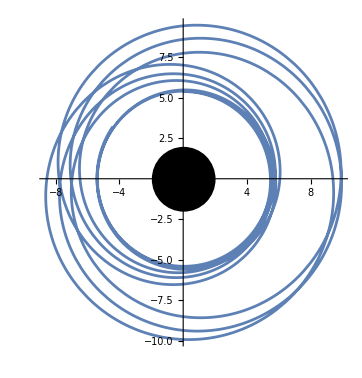

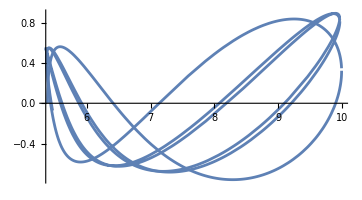

```mathematica
{spA,snA,eA,pA,bA,MA}={0,3/10,3/10,7,0/3,1};
ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[φ0[λ]],r0λ[λ] Cos[φ0[λ]]};
FigAnalyse=ParametricPlot[%,{λ,0,5π},Prolog->{Black,Disk[{0,0},2]}]

{spA,snA,eA,pA,bA,MA}={0,3/10,3/10,7,0/3,1};
ParamExactBW[spA,snA,eA,pA,bA,MA]@{r0λ[λ] Sin[θ0[λ]],r0λ[λ] Cos[θ0[λ]]};
FigAnalyse=ParametricPlot[%,{λ,0,5π},Prolog->{Black,Disk[{0,0},2]}]
```

# Conclusion

### Kepler parameter

```mathematica
XE=p-3-e^2;
YE=(p-2)^2-4 e^2;
ZE=1-e^2;
WE=(p^2 YE+2 b p (-2+p+(2+p) (1-ZE))+b^2 ZE^2);
VE=p XE-2 b (-2+ZE);
U1E=(b-p) (b^2 p+b (-1+p) p^2-p^3-b^3 (-1+ZE));
U2E=2 p^5+b^2 p^2 (16-p (-2+ZE))+2 b^3 p (p (-2+ZE)-3 ZE)+b^4 ZE^2+2 b p^3 (-8-(-2+p) p+ZE);
U3E=b^2 ZE^2-2 b p (p (-2+ZE)+2 ZE)+p^2 ((-4+p) p+4 ZE);

r1solep=p/(1-e);
r2solep=p/(1+e);
r3solep=(p ((b-p)^2+√U1)Z)/(p^2 V-W)+sp Z^2(√((-b+p) W))/(2(p^2 V-W)^2)(2 p (p^2+b (-2 p+Z))+ U2/(√U1));
r4solep=-(b (b-p) p)/((b-p)^2+√U1)+sp (b Z √(-b+p))/(2 ((b-p)^2+√U1)^2(p^2 V-W)) (2((b-p)^2+√U1) (2 (-2+p) p+b Z) √U3-√W(-b+p)(2 p(p^2+b (-2 p+Z))+U2/(√U1)));
```

### Integral solutions of motion

```mathematica
λr0[χ_]:=(2 EllipticF[χ,k0^2])/(√(1-ℰ^2)√((r1-r3) (r2-r4)));
```

```mathematica
Tr0[χ_]:=1/(√(1-ℰ^2)√((r1-r3) (r2-r4)))(
((r1-r2) √((r1-r3) (r2-r4)) ℰ Sin[2 χ]  √(-(-((r1-r3) (r2-r4))+(r1-r2) (r3-r4) Sin[χ]^2)))/(2 r3-(r1+r2)-(r1-r2) Cos[2 χ])
+(r1-r3) (r2-r4) ℰ EllipticE[χ,k0^2]
+1/((r3-rn) (r3-rp))(-2 (rnIntCharge) (r3-rp)+2 (r3-rn) rpIntCharge+(8-2 b+r1 (-r2+r3)+r3 (4+r2+r3)) (r3-rn) (r3-rp)ℰ) EllipticF[χ,k0^2]
+(r2-r3) ((4+r1+r2+r3+r4) ℰ) EllipticPi[(r1-r2)/(r1-r3),χ,k0^2]
+(2 (r2-r3) rnIntCharge EllipticPi[((r1-r2) (r3-rn))/((r1-r3) (r2-rn)),χ,k0^2])/((r2-rn) (r3-rn))+(2 (r2-r3) rpIntCharge EllipticPi[((r1-r2) (r3-rp))/((r1-r3) (r2-rp)),χ,k0^2])/((r2-rp) (-r3+rp))
)/.{rpIntCharge->1/(rp-rn)(( +8 ℰ-4 b ℰ+sp 𝒥 ) rp+ b( (-4+b)ℰ-sp 𝒥)),rnIntCharge-> 1/(rp-rn)((  8 ℰ-4 b ℰ+sp 𝒥) rn+ b (2 (-4+b)ℰ-sp 𝒥))};
```

```mathematica
Φr0[χ_]:=(2(sp ℰ+𝒥) EllipticF[χ,k0^2])/(√(1-ℰ^2)√((r1-r3) (r2-r4)));
```

```mathematica
Ψr0[χ_]:=(2  ℰ 𝒥)/(√(1-ℰ^2)√((r1-r3) (r2-r4))  (r2^2+𝒥^2) (r3^2+𝒥^2))( (r2-r3) 𝒥 (r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]]+r3^2 (r2^2+𝒥^2) EllipticF[χ,k0^2]+(r2-r3) (r2+r3) 𝒥^2 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),χ,k0^2]])/.{yr->Sin[χ]};
```

### Frequency

```mathematica
ϒr=(π √((r1-r3) (r2-r4)) √(1-ℰ^2))/(2 EllipticK[k0^2]);
ϒt=1/2 ((8-2 b+r1 (-r2+r3)+r3 (4+r2+r3)) ℰ+(2 ((-4+b) b ℰ-4 (-2+b) rp ℰ-b sp 𝒥+rp sp 𝒥))/((r3-rp) (-rn+rp))+(4 b^2 ℰ+2 rn (8 ℰ+sp 𝒥)-2 b (4 (2+rn) ℰ+sp 𝒥))/((r3-rn) (rn-rp)))+((r1-r3) (r2-r4) ℰ EllipticE[k0^2])/(2 EllipticK[k0^2])+1/(2 EllipticK[k0^2])(r2-r3) ((4+r1+r2+r3+r4) ℰ EllipticPi[(r1-r2)/(r1-r3),k0^2]+(2 (2 (-4+b) b ℰ-4 (-2+b) rn ℰ-b sp 𝒥+rn sp 𝒥) EllipticPi[((r1-r2) (r3-rn))/((r1-r3) (r2-rn)),k0^2])/((r2-rn) (-r3+rn) (rn-rp))+(2 ((-4+b) b ℰ-4 (-2+b) rp ℰ-b sp 𝒥+rp sp 𝒥) EllipticPi[((r1-r2) (r3-rp))/((r1-r3) (r2-rp)),k0^2])/((r2-rp) (-r3+rp) (-rn+rp)));
ϒφ=sp ℰ+𝒥;
ϒψ=(r3^2 ℰ 𝒥)/(r3^2+𝒥^2)+((r2-r3) ℰ 𝒥^2 ((r2 r3-𝒥^2) Im[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]+(r2+r3) 𝒥 Re[EllipticPi[((r1-r2) (r3-ⅈ 𝒥))/((r1-r3) (r2-ⅈ 𝒥)),k0^2]]))/((r2^2+𝒥^2) (r3^2+𝒥^2) EllipticK[k0^2]);
```

### Linear shift

```mathematica
ϒrb=;
ϒrsp=;
```

```mathematica
Υtb=;
Υtsp=;
```

```mathematica
ϒφb=√𝒥2b;
ϒφsp=√ℰ2b+𝒥2sb/(2 √𝒥2b);
```

```mathematica
ϒψb=(√ℰ2b √𝒥2b (r3b^2+((r2b-r3b) √𝒥2b ((r2b r3b-𝒥2b) Im[EllipticPi[((r1b-r2b) (r3b-ⅈ √𝒥2b))/((r1b-r3b) (r2b-ⅈ √𝒥2b)),kb02]]+(r2b+r3b) √𝒥2b Re[EllipticPi[((r1b-r2b) (r3b-ⅈ √𝒥2b))/((r1b-r3b) (r2b-ⅈ √𝒥2b)),kb02]]))/((r2b^2+𝒥2b) EllipticK[kb02])))/(r3b^2+𝒥2b);
```

```mathematica
νnodal=2 π (-1+(r3b^2+𝒥2b)/(√ℰ2b (r3b^2+((r2b-r3b) √𝒥2b ((r2b r3b-𝒥2b) Im[EllipticPi[((r1b-r2b) (r3b-ⅈ √𝒥2b))/((r1b-r3b) (r2b-ⅈ √𝒥2b)),kb02]]+(r2b+r3b) √𝒥2b Re[EllipticPi[((r1b-r2b) (r3b-ⅈ √𝒥2b))/((r1b-r3b) (r2b-ⅈ √𝒥2b)),kb02]]))/((r2b^2+𝒥2b) EllipticK[kb02]))));
νperiBW=2 π (-1+(2 √𝒥2b EllipticK[kb02])/(π √((r1b-r3b) (r2b-r4b)) √(1-ℰ2b)));
δνperi=1/(π (r1b-r3b) (r2b-r4b) (1-ℰ2b))8 EllipticK[kb02]^2 ((π √((r1b-r3b) (r2b-r4b)) √(1-ℰ2b) (√ℰ2b+𝒥2sb/(2 √𝒥2b)))/(2 EllipticK[kb02])+√𝒥2b (-(π (-r3sb (r2b-r4b)-(r1b-r3b) r4sb) √(1-ℰ2b))/(4 √((r1b-r3b) (r2b-r4b)) EllipticK[kb02])+(π √((r1b-r3b) (r2b-r4b)) ℰ2sb)/(4 √(1-ℰ2b) EllipticK[kb02])+(ks02 π √((r1b-r3b) (r2b-r4b)) √(1-ℰ2b) (EllipticE[kb02]-(1-kb02) EllipticK[kb02]))/(4 (1-kb02) kb02 EllipticK[kb02]^2)));
νperi=νperiBW+δνperi;
```

### Orbit

```mathematica
qr[λ_]:=ϒr λ + qr0;
qt[λ_]:=ϒt λ + qt0;
qφ[λ_]:=ϒφ λ + qφ0;
qψ[λ_]:=ϒψ λ + qψ0;
```

```mathematica
r0λ[λ_]:=(r2 (-r1+r3)+(r1-r2) r3 (Sin@JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2])^2)/(-r1+r3+(r1-r2) (Sin@JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2])^2);
t0[λ_]:=qt[λ]+Tr0[JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2]]-Tr0[π]/(2π)qr[λ];
φ0[λ_]:=qφ[λ]+Φr0[JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2]]-Φr0[π]/(2π)qr[λ];
ψ0[λ_]:=qψ[λ]+Ψr0[JacobiAmplitude[qr[λ]/π EllipticK[k0^2],k0^2]]-Ψr0[π]/(2π)qr[λ];
θ0[λ_]:=π/2+(√(sn^2)√(r0λ[λ]^2+𝒥^2))/(r0λ[λ] 𝒥) Sin[ψ0[λ]];
```

```mathematica
t0A[λ_]:=Tr0[JacobiAmplitude[(√((r1-r3) (r2-r4)) √(1-ℰ^2))/2 λ,k0^2]];
```

# GW

## Fluxes

References:

1.[Gravitational_Peters_1964] P. C. Peters, Gravitational Radiation and the Motion of Two Point Masses, Phys. Rev. 136, B1224 (1964).

2.[Gravitational_Peters_1963] P. C. Peters and J. Mathews, Gravitational Radiation from Point Masses in a Keplerian Orbit, Phys. Rev. 131, 435 (1963).

### mass moment QM[i,j]

```mathematica
QM[i,j]
ParamD[t[]][QM[i,j]]
QM[{1,-Euro},{1,-Euro}]
```

μ Cos[ϕ[t]]^2 r[t]^2 | μ Cos[ϕ[t]] Sin[ϕ[t]] r[t]^2 | -μ ϵ Cos[ϕ[t]] r[t]^2 δθ[t]
μ Cos[ϕ[t]] Sin[ϕ[t]] r[t]^2 | μ Sin[ϕ[t]]^2 r[t]^2 | -μ ϵ Sin[ϕ[t]] r[t]^2 δθ[t]
-μ ϵ Cos[ϕ[t]] r[t]^2 δθ[t] | -μ ϵ Sin[ϕ[t]] r[t]^2 δθ[t] | μ ϵ^2 r[t]^2 δθ[t]^2 | i | j
  |

● | ● | ●
● | ● | ●
● | ● | ● | i | j
  |

```mathematica
xPoint[i]
```

M Cos[ϕ[t]] r[t]
M Sin[ϕ[t]] r[t]
-M ϵ r[t] δθ[t] | i

```mathematica
D[D[D[ϕ[λ[t[]]], λ[t[]]], λ[t[]]], λ[t[]]]
D[D[D[ϕ[λ[t[]]], t[]], t[]], t[]]
```

ϕ^(3)[λ[t]]

3 λ'[t] λ''[t] ϕ''[λ[t]]+ϕ'[λ[t]] λ^(3)[t]+λ'[t]^3 ϕ^(3)[λ[t]]

### Fluxs

```mathematica
dEdt=FullSimplify@Series[-1/(5 m)(∂_t[] ∂_t[] ∂_t[] QM[i,j] ∂_t[] ∂_t[] ∂_t[] QM[-i,-j]-1/3 ∂_t[] ∂_t[] ∂_t[] QM[i,-i] ∂_t[] ∂_t[] ∂_t[] QM[j,-j]),{ϵ,0,1}]
dJdt1=FullSimplify@Series[-2/(5 m M)epsilongEuor[{1,Euro},-j,-k] (∂_t[] ∂_t[] QM[j,l] ∂_t[] ∂_t[] ∂_t[] QM[k,-l]),{ϵ,0,1}]
dJdt2=FullSimplify@Series[-2/(5 m M)epsilongEuor[{2,Euro},-j,-k] (∂_t[] ∂_t[] QM[j,l] ∂_t[] ∂_t[] ∂_t[] QM[k,-l]),{ϵ,0,1}]
dJdt3=FullSimplify@Series[-2/(5 m M)epsilongEuor[{3,Euro},-j,-k] (∂_t[] ∂_t[] QM[j,l] ∂_t[] ∂_t[] ∂_t[] QM[k,-l]),{ϵ,0,1}]
```

1/(15 m)2 M^4 μ^2 (-108 (∂_t[] r[t])^4 (∂_t[] ϕ[t])^2-216 (∂_t[] r[t])^3 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ϕ[t] r[t]-36 (∂_t[] r[t])^2 ((∂_t[] ∂_t[] r[t])^2+(8 (∂_t[] ϕ[t])^4+3 (∂_t[] ∂_t[] ϕ[t])^2+∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t]^2)+r[t]^2 (-4 (27 (∂_t[] ϕ[t])^2 (∂_t[] ∂_t[] r[t])^2+(∂_t[] ∂_t[] ∂_t[] r[t])^2)+36 ∂_t[] ϕ[t] (∂_t[] ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]+∂_t[] ∂_t[] r[t] (4 (∂_t[] ϕ[t])^3-∂_t[] ∂_t[] ∂_t[] ϕ[t])) r[t]-3 (16 (∂_t[] ϕ[t])^6+36 (∂_t[] ϕ[t])^2 (∂_t[] ∂_t[] ϕ[t])^2-8 (∂_t[] ϕ[t])^3 ∂_t[] ∂_t[] ∂_t[] ϕ[t]+(∂_t[] ∂_t[] ∂_t[] ϕ[t])^2) r[t]^2)-12 ∂_t[] r[t] r[t] (∂_t[] ∂_t[] r[t] (2 ∂_t[] ∂_t[] ∂_t[] r[t]+9 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ϕ[t] r[t])+3 r[t] (-2 (∂_t[] ϕ[t])^2 ∂_t[] ∂_t[] ∂_t[] r[t]+∂_t[] ∂_t[] ϕ[t] (8 (∂_t[] ϕ[t])^3+∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t])))+O[ϵ]^2

1/(5 m)2 M^3 μ^2 (12 (∂_t[] r[t])^4 (Sin[ϕ[t]] ∂_t[] δθ[t]-Cos[ϕ[t]] ∂_t[] ϕ[t] δθ[t])+12 (∂_t[] r[t])^3 r[t] (-Cos[ϕ[t]] ∂_t[] ∂_t[] ϕ[t] δθ[t]+Sin[ϕ[t]] (∂_t[] ∂_t[] δθ[t]+(∂_t[] ϕ[t])^2 δθ[t]))+2 (∂_t[] r[t])^2 r[t]^2 (Sin[ϕ[t]] (33 ∂_t[] δθ[t] (∂_t[] ϕ[t])^2+∂_t[] ∂_t[] ∂_t[] δθ[t]+3 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ϕ[t] δθ[t])-Cos[ϕ[t]] (-9 ∂_t[] ϕ[t] ∂_t[] ∂_t[] δθ[t]+9 ∂_t[] δθ[t] ∂_t[] ∂_t[] ϕ[t]+(23 (∂_t[] ϕ[t])^3+∂_t[] ∂_t[] ∂_t[] ϕ[t]) δθ[t]))+2 ∂_t[] r[t] r[t]^2 (Cos[ϕ[t]] (2 (∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] δθ[t]+∂_t[] δθ[t] ((∂_t[] ϕ[t])^3-∂_t[] ∂_t[] ∂_t[] ϕ[t])) r[t]+(4 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]-3 ∂_t[] ∂_t[] ϕ[t] (∂_t[] ∂_t[] r[t]+6 (∂_t[] ϕ[t])^2 r[t])) δθ[t])+Sin[ϕ[t]] (-4 ∂_t[] δθ[t] ∂_t[] ∂_t[] ∂_t[] r[t]+3 ∂_t[] ∂_t[] r[t] (∂_t[] ∂_t[] δθ[t]+(∂_t[] ϕ[t])^2 δθ[t])+6 ∂_t[] ϕ[t] r[t] (∂_t[] ϕ[t] ∂_t[] ∂_t[] δθ[t]+3 ∂_t[] δθ[t] ∂_t[] ∂_t[] ϕ[t]+(∂_t[] ϕ[t])^3 δθ[t])))+r[t]^2 (Cos[ϕ[t]] (r[t] (6 ∂_t[] ∂_t[] r[t] (-∂_t[] ϕ[t] ∂_t[] ∂_t[] δθ[t]+∂_t[] δθ[t] ∂_t[] ∂_t[] ϕ[t])+(10 (∂_t[] ϕ[t])^3 ∂_t[] ∂_t[] δθ[t]-9 ∂_t[] δθ[t] (∂_t[] ϕ[t])^2 ∂_t[] ∂_t[] ϕ[t]+∂_t[] ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] δθ[t]-∂_t[] ∂_t[] δθ[t] ∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t])+(-12 ∂_t[] ϕ[t] (∂_t[] ∂_t[] r[t])^2+2 (∂_t[] ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]+∂_t[] ∂_t[] r[t] (13 (∂_t[] ϕ[t])^3-∂_t[] ∂_t[] ∂_t[] ϕ[t])) r[t]+3 ∂_t[] ϕ[t] (-2 (∂_t[] ϕ[t])^4-3 (∂_t[] ∂_t[] ϕ[t])^2+∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t]^2) δθ[t])+Sin[ϕ[t]] (∂_t[] δθ[t] (12 (∂_t[] ∂_t[] r[t])^2-30 (∂_t[] ϕ[t])^2 ∂_t[] ∂_t[] r[t] r[t]+(14 (∂_t[] ϕ[t])^4+3 (∂_t[] ∂_t[] ϕ[t])^2-2 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t]^2)+r[t] (2 ∂_t[] ∂_t[] ∂_t[] δθ[t] (∂_t[] ∂_t[] r[t]-(∂_t[] ϕ[t])^2 r[t])+∂_t[] ∂_t[] δθ[t] (-2 ∂_t[] ∂_t[] ∂_t[] r[t]+9 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ϕ[t] r[t])+∂_t[] ϕ[t] (-2 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]+3 ∂_t[] ∂_t[] ϕ[t] (2 ∂_t[] ∂_t[] r[t]+(∂_t[] ϕ[t])^2 r[t])) δθ[t])))) ϵ+O[ϵ]^2

1/(5 m)2 M^3 μ^2 (-12 (∂_t[] r[t])^4 (Cos[ϕ[t]] ∂_t[] δθ[t]+Sin[ϕ[t]] ∂_t[] ϕ[t] δθ[t])-12 (∂_t[] r[t])^3 r[t] (Sin[ϕ[t]] ∂_t[] ∂_t[] ϕ[t] δθ[t]+Cos[ϕ[t]] (∂_t[] ∂_t[] δθ[t]+(∂_t[] ϕ[t])^2 δθ[t]))+2 (∂_t[] r[t])^2 r[t]^2 (-Cos[ϕ[t]] (33 ∂_t[] δθ[t] (∂_t[] ϕ[t])^2+∂_t[] ∂_t[] ∂_t[] δθ[t]+3 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ϕ[t] δθ[t])-Sin[ϕ[t]] (-9 ∂_t[] ϕ[t] ∂_t[] ∂_t[] δθ[t]+9 ∂_t[] δθ[t] ∂_t[] ∂_t[] ϕ[t]+(23 (∂_t[] ϕ[t])^3+∂_t[] ∂_t[] ∂_t[] ϕ[t]) δθ[t]))+2 ∂_t[] r[t] r[t]^2 (Sin[ϕ[t]] (2 (∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] δθ[t]+∂_t[] δθ[t] ((∂_t[] ϕ[t])^3-∂_t[] ∂_t[] ∂_t[] ϕ[t])) r[t]+(4 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]-3 ∂_t[] ∂_t[] ϕ[t] (∂_t[] ∂_t[] r[t]+6 (∂_t[] ϕ[t])^2 r[t])) δθ[t])-Cos[ϕ[t]] (-4 ∂_t[] δθ[t] ∂_t[] ∂_t[] ∂_t[] r[t]+3 ∂_t[] ∂_t[] r[t] (∂_t[] ∂_t[] δθ[t]+(∂_t[] ϕ[t])^2 δθ[t])+6 ∂_t[] ϕ[t] r[t] (∂_t[] ϕ[t] ∂_t[] ∂_t[] δθ[t]+3 ∂_t[] δθ[t] ∂_t[] ∂_t[] ϕ[t]+(∂_t[] ϕ[t])^3 δθ[t])))+r[t]^2 (Sin[ϕ[t]] (r[t] (6 ∂_t[] ∂_t[] r[t] (-∂_t[] ϕ[t] ∂_t[] ∂_t[] δθ[t]+∂_t[] δθ[t] ∂_t[] ∂_t[] ϕ[t])+(10 (∂_t[] ϕ[t])^3 ∂_t[] ∂_t[] δθ[t]-9 ∂_t[] δθ[t] (∂_t[] ϕ[t])^2 ∂_t[] ∂_t[] ϕ[t]+∂_t[] ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] δθ[t]-∂_t[] ∂_t[] δθ[t] ∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t])+(-12 ∂_t[] ϕ[t] (∂_t[] ∂_t[] r[t])^2+2 (∂_t[] ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]+∂_t[] ∂_t[] r[t] (13 (∂_t[] ϕ[t])^3-∂_t[] ∂_t[] ∂_t[] ϕ[t])) r[t]+3 ∂_t[] ϕ[t] (-2 (∂_t[] ϕ[t])^4-3 (∂_t[] ∂_t[] ϕ[t])^2+∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t]^2) δθ[t])+Cos[ϕ[t]] (∂_t[] δθ[t] (-12 (∂_t[] ∂_t[] r[t])^2+30 (∂_t[] ϕ[t])^2 ∂_t[] ∂_t[] r[t] r[t]+(-14 (∂_t[] ϕ[t])^4-3 (∂_t[] ∂_t[] ϕ[t])^2+2 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t]^2)+r[t] (-2 ∂_t[] ∂_t[] ∂_t[] δθ[t] (∂_t[] ∂_t[] r[t]-(∂_t[] ϕ[t])^2 r[t])+∂_t[] ∂_t[] δθ[t] (2 ∂_t[] ∂_t[] ∂_t[] r[t]-9 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ϕ[t] r[t])+∂_t[] ϕ[t] (2 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]-3 ∂_t[] ∂_t[] ϕ[t] (2 ∂_t[] ∂_t[] r[t]+(∂_t[] ϕ[t])^2 r[t])) δθ[t])))) ϵ+O[ϵ]^2

1/(5 m)4 M^3 μ^2 (-6 (∂_t[] r[t])^4 ∂_t[] ϕ[t]-6 (∂_t[] r[t])^3 ∂_t[] ∂_t[] ϕ[t] r[t]-(∂_t[] r[t])^2 (32 (∂_t[] ϕ[t])^3+∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t]^2+r[t]^2 (-6 ∂_t[] ϕ[t] (∂_t[] ∂_t[] r[t])^2+(∂_t[] ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]+∂_t[] ∂_t[] r[t] (16 (∂_t[] ϕ[t])^3-∂_t[] ∂_t[] ∂_t[] ϕ[t])) r[t]+2 ∂_t[] ϕ[t] (-4 (∂_t[] ϕ[t])^4-3 (∂_t[] ∂_t[] ϕ[t])^2+∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] ϕ[t]) r[t]^2)+∂_t[] r[t] r[t]^2 (4 ∂_t[] ϕ[t] ∂_t[] ∂_t[] ∂_t[] r[t]-3 ∂_t[] ∂_t[] ϕ[t] (∂_t[] ∂_t[] r[t]+8 (∂_t[] ϕ[t])^2 r[t])))+O[ϵ]^2

## Calculation of Fluxes

### ℰ & 𝒥

```mathematica
Series[ParamExactBW[sp,sn,e,p,b,M]@ℰ,{b,0,1},{sp,0,1},{p,Infinity,3}]
```

((1+(-1+e^2)/(2 p)+(3 (1-2 e^2+e^4))/(8 p^2)+(27-49 e^2+17 e^4+5 e^6)/(16 p^3)+O[1/p]^4)+(1/2 (1-2 e^2+e^4) (1/p)^(5/2)+O[1/p]^(7/2)) sp+O[sp]^2)+(((-1+2 e^2-e^4)/p^3+O[1/p]^(7/2))+O[1/p]^(7/2) sp+O[sp]^2) b+O[b]^2

```mathematica
ETopeApprox=Normal@Simplify@eptoXYZ@Simplify[Series[EJTope["Spacetime" -> "Brane"]@(ℰ),{sp,0,1},{p,Infinity,4}]]
JTopeApprox=Normal@Simplify@eptoXYZ@Simplify[Series[EJTope["Spacetime" -> "Brane"]@(𝒥),{sp,0,1},{p,Infinity,3}]]
```

1-Z/(2 p)+(3 Z^2)/(8 p^2)-(Z^2 (-32+16 b+5 Z))/(16 p^3)+(Z^2 (1024+64 b^2+192 b (-4+Z)-384 Z+35 Z^2))/(128 p^4)+sp ((Z^2 Abs[e])/(2 e p^(5/2))-((5 b+3 (-4+Z)) Z^2 Abs[e])/(4 e p^(7/2)))

√p+(4-b-Z)/(2 √p)+(-b^2/8+3/8 (-4+Z)^2+b (-3+(5 Z)/4))/p^(3/2)+(-b^3+b^2 (12-7 Z)-5 (-4+Z)^3-3 b (80-56 Z+9 Z^2))/(16 p^(5/2))+sp (-Abs[e]/e+(2 Abs[e])/(e p)+((64+16 b (-2+Z)-40 Z+3 Z^2) Abs[e])/(8 e p^2)+((251+5 e^6-209 Z+39 Z^2-8 b (24-20 Z+3 Z^2)) Abs[e])/(8 e p^3))

1-Z/(2 p)+(3 Z^2)/(8 p^2)-(Z^2 (-32+16 b+5 Z))/(16 p^3)+(sp Z^2)/(2 p^(5/2))

√p+(4-Z-b)/(2 √p)+(3 (-4+Z)^2+b (-24+10 Z)-b^2)/(8 p^(3/2))+sp (-1+2/p+(64-40 Z+3 Z^2+16 b (-2+Z))/(8 p^2))

### Period

r[t]==p/(1+e Cos[ψ[t]])

(d r)/(d t)==d/dt(p/(1+e Cos[ψ_r[t]]))==(e p √(Sin[ψ_r[t]]^2) ψ_r'[t])/(1+e Cos[ψ_r[t]])^2

Note that in the case of mass normalization, this 1/M cannot be ignored

```mathematica
Fft0=ParamExactBW[sp,sn,e,p,b,M]@ToSpacetime["Spacetime"->"Brane"]@(ℰ/f[p/(1+e  Cos[ψ[t[]]])]+(𝒥 f'[p/(1+e Cos[ψ[t[]]])] sp)/(2 p/(1+e Cos[ψ[t[]]]) f[p/(1+e Cos[ψ[t[]]])]));
Ffψ0=ParamExactBW[sp,sn,e,p,b,M]@ToSpacetime["Spacetime"->"Brane"]@((1+e Cos[ψ[t[]]])^2/(e p √(Sin[ψ[t]]^2))√(ℰ^2-((𝒥^2+(p/(1+e Cos[ψ[t[]]]))^2)f[p/(1+e Cos[ψ[t[]]])])/(p/(1+e Cos[ψ[t[]]]))^2+(sp 𝒥 ℰ(-2 f[p/(1+e Cos[ψ[t[]]])]+p/(1+e Cos[ψ[t[]]]) f'[p/(1+e Cos[ψ[t[]]])]))/(p/(1+e Cos[ψ[t[]]]))^2))1/M;
Ffϕ0=ParamExactBW[sp,sn,e,p,b,M]@ToSpacetime["Spacetime"->"Brane"]@(𝒥/(p/(1+e Cos[ψ[t[]]]))^2+ (ℰ sp)/(p/(1+e Cos[ψ[t[]]]))^2)1/M;
```

Orbital period from perihelion to aphelion

```mathematica
FdtdψPN=FullSimplify[Series[Fft0/Ffψ0 ,{p,Infinity,0},{sp,0,1}],M>0&&1>e>0&&p>0]//Normal
KT=Integrate[FdtdψPN ,{ψ[t],0,2π},Assumptions->(1+√(1-e^2))/e≥1&&e+√(1-e^2)>1]
FdψdtPN=FullSimplify[Series[Ffψ0/Fft0 ,{p,Infinity,3},{sp,0,1}],M>0&&1>e>0&&p>0]//Normal
```

(M p^(3/2))/(1+e Cos[ψ_r[t]])^2+(3 M √p)/(1+e Cos[ψ_r[t]])+(M sp (3-e^2+2 e Cos[ψ_r[t]]))/(2 (1+e Cos[ψ_r[t]])^2)

-(M π (-2 √p (3-3 e^2+p)+3 (-1+e^2) sp))/((1-e^2)^(3/2))

(1+e Cos[ψ_r[t]])^2/(M p^(3/2))+(sp (-3+e^2-2 e Cos[ψ_r[t]]) (1+e Cos[ψ_r[t]])^2)/(2 M p^3)-(3 (1+e Cos[ψ_r[t]])^3)/(M p^(5/2))

### Calculcation

```mathematica
ConrtphitApprox[2,7,"Spacetime"->"Brane"][∂_t[] r[t]]
ConrtphitApprox[2,7,"Spacetime"->"Brane"][∂_t[] ∂_t[] r[t]]
ConrtphitApprox[2,7,"Spacetime"->"Brane"][∂_t[] ∂_t[] ∂_t[] r[t]]
ConrtphitApprox[2,7,"Spacetime"->"Brane"][ParamD[t[]][ϕ[][t[]]]]
ConrtphitApprox[2,7,"Spacetime"->"Brane"][ParamD[t[],t[]][ϕ[][t[]]]]
ConrtphitApprox[2,7,"Spacetime"->"Brane"][ParamD[t[],t[],t[]][ϕ[][t[]]]]
```

FdψdtPN:3

(e Sin[ψ_r[t]])/(M √p)+(e sp (-3+e^2-2 e Cos[ψ_r[t]]) Sin[ψ_r[t]])/(2 M p^2)-(3 e (1+e Cos[ψ_r[t]]) Sin[ψ_r[t]])/(M p^(3/2))

FdψdtPN:3

DFdψdtPN:4

FdψdtPN:3

(e Cos[ψ_r[t]] (1+e Cos[ψ_r[t]])^2)/(M^2 p^2)+(9 e (1+e Cos[ψ_r[t]])^3 (Cos[ψ_r[t]]+e Cos[2 ψ_r[t]]))/(M^2 p^4)-(3 e (1+e Cos[ψ_r[t]])^2 (e+4 Cos[ψ_r[t]]+3 e Cos[2 ψ_r[t]]))/(2 M^2 p^3)+sp ((e (e+Cos[ψ_r[t]]) (-3+e^2-2 e Cos[ψ_r[t]]) (1+e Cos[ψ_r[t]]))/(M^2 p^(7/2))-(3 e (-3+e^2-2 e Cos[ψ_r[t]]) (1+e Cos[ψ_r[t]])^2 (4 Cos[ψ_r[t]]+e (3+Cos[2 ψ_r[t]])))/(4 M^2 p^(9/2)))

FdψdtPN:3

DFdψdtPN:4

DDFdψdtPN:6

FdψdtPN:3

DFdψdtPN:4

FdψdtPN:3

-(e (1+e Cos[ψ_r[t]])^3 (1+3 e Cos[ψ_r[t]]) Sin[ψ_r[t]])/(M^3 p^(7/2))+(27 e (1+e Cos[ψ_r[t]])^5 (1+2 e^2+8 e Cos[ψ_r[t]]+5 e^2 Cos[2 ψ_r[t]]) Sin[ψ_r[t]])/(M^3 p^(13/2))-(9 e (1+e Cos[ψ_r[t]])^4 (3+6 e^2+20 e Cos[ψ_r[t]]+11 e^2 Cos[2 ψ_r[t]]) Sin[ψ_r[t]])/(M^3 p^(11/2))+(3 e (1+e Cos[ψ_r[t]])^3 (6+11 e^2+32 e Cos[ψ_r[t]]+15 e^2 Cos[2 ψ_r[t]]) Sin[ψ_r[t]])/(2 M^3 p^(9/2))+sp ((e (1+e Cos[ψ_r[t]])^2 (3-e^2+2 e Cos[ψ_r[t]]) (6-e^2+8 e Cos[ψ_r[t]]+3 e^2 Cos[2 ψ_r[t]]) Sin[ψ_r[t]])/(4 M^3 p^5)+(3 e (-3+e^2-2 e Cos[ψ_r[t]]) (1+e Cos[ψ_r[t]])^3 (6+3 e^2+16 e Cos[ψ_r[t]]+7 e^2 Cos[2 ψ_r[t]]) Sin[ψ_r[t]])/(2 M^3 p^6)+(27 e (1+e Cos[ψ_r[t]])^4 (3+6 e^2-e^4+14 e Cos[ψ_r[t]]-2 e^2 (-5+e^2) Cos[2 ψ_r[t]]+2 e^3 Cos[3 ψ_r[t]]) Sin[ψ_r[t]])/(2 M^3 p^7))

(1+e Cos[ψ_r[t]])^2/(M p^(3/2))+((3+e^2) sp (1+e Cos[ψ_r[t]])^2)/(2 M p^3)-((1+e Cos[ψ_r[t]])^2 (b+4 e Cos[ψ_r[t]]))/(2 M p^(5/2))

FdψdtPN:3

-(2 e (1+e Cos[ψ_r[t]])^3 Sin[ψ_r[t]])/(M^2 p^3)-(3 e (1+e Cos[ψ_r[t]])^4 (2+b+6 e Cos[ψ_r[t]]) Sin[ψ_r[t]])/(M^2 p^5)+(e (1+e Cos[ψ_r[t]])^3 (8+b+12 e Cos[ψ_r[t]]) Sin[ψ_r[t]])/(M^2 p^4)+sp ((e (1+e Cos[ψ_r[t]])^3 (3-e^2+2 e Cos[ψ_r[t]]) Sin[ψ_r[t]])/(M^2 p^(9/2))+(e (-3+e^2-2 e Cos[ψ_r[t]]) (1+e Cos[ψ_r[t]])^3 (2+b+6 e Cos[ψ_r[t]]) Sin[ψ_r[t]])/(2 M^2 p^(11/2)))

FdψdtPN:3

DFdψdtPN:4

FdψdtPN:3

-(2 e (1+e Cos[ψ_r[t]])^4 (Cos[ψ_r[t]]+e (-1+2 Cos[2 ψ_r[t]])))/(M^3 p^(9/2))+(e (1+e Cos[ψ_r[t]])^4 ((14+b-3 e^2) Cos[ψ_r[t]]+e (-11-b+(43+2 b) Cos[2 ψ_r[t]]+21 e Cos[3 ψ_r[t]])))/(M^3 p^(11/2))-(3 e (1+e Cos[ψ_r[t]])^5 (4 (5+b-3 e^2) Cos[ψ_r[t]]+e (-22-5 b+(78+9 b) Cos[2 ψ_r[t]]+48 e Cos[3 ψ_r[t]])))/(2 M^3 p^(13/2))+sp (-(e (-3+e^2-2 e Cos[ψ_r[t]]) (1+e Cos[ψ_r[t]])^4 (2 Cos[ψ_r[t]]+e (-1+3 Cos[2 ψ_r[t]])))/(M^3 p^6)+(e (-3+e^2-2 e Cos[ψ_r[t]]) (1+e Cos[ψ_r[t]])^4 ((32+4 b+3 e^2) Cos[ψ_r[t]]+e (-2 (5+b)+6 (15+b) Cos[2 ψ_r[t]]+45 e Cos[3 ψ_r[t]])))/(4 M^3 p^7))

### Energy flux integral over one orbital period

```mathematica
SpacetimeSet
```

{UnKnow,Schwarzschild,Brane}

```mathematica
dEdtApproxAll=ConrtphitApprox[2,6,"Spacetime"->"Schwarzschild"]@dEdt
```

FdψdtPN:3

FdψdtPN:3

DFdψdtPN:4

FdψdtPN:3

FdψdtPN:3

DFdψdtPN:4

DDFdψdtPN:6

FdψdtPN:3

DFdψdtPN:4

FdψdtPN:3

FdψdtPN:3

FdψdtPN:3

DFdψdtPN:4

FdψdtPN:3

-(4 μ^2 (1+e Cos[ψ_r[t]])^4 (24+13 e^2+48 e Cos[ψ_r[t]]+11 e^2 Cos[2 ψ_r[t]]))/(15 m M^2 p^5)-(4 e μ^2 (1+e Cos[ψ_r[t]])^4 ((-8+5 e^2) Cos[ψ_r[t]]+e (-20+e^2+14 (2+e^2) Cos[2 ψ_r[t]]+35 e Cos[3 ψ_r[t]]+9 e^2 Cos[4 ψ_r[t]])))/(5 m M^2 p^6)

```mathematica
dEdtApproxAll=ConrtphitApprox[3,7,"Spacetime"->"Brane"]@dEdt
```

FdψdtPN:4

FdψdtPN:4

DFdψdtPN:5

FdψdtPN:4

FdψdtPN:4

DFdψdtPN:5

DDFdψdtPN:7

FdψdtPN:4

DFdψdtPN:5

FdψdtPN:4

FdψdtPN:4

FdψdtPN:4

DFdψdtPN:5

FdψdtPN:4

-(4 μ^2 (1+e Cos[ψ_r[t]])^4 (24+13 e^2+48 e Cos[ψ_r[t]]+11 e^2 Cos[2 ψ_r[t]]))/(15 m M^2 p^5)+(4 μ^2 (1+e Cos[ψ_r[t]])^4 (24 b+20 e^2+28 b e^2-e^4+e (8-5 e^2+4 b (16+3 e^2)) Cos[ψ_r[t]]-14 e^2 (2-2 b+e^2) Cos[2 ψ_r[t]]-35 e^3 Cos[3 ψ_r[t]]+4 b e^3 Cos[3 ψ_r[t]]-9 e^4 Cos[4 ψ_r[t]]))/(5 m M^2 p^6)-(2 μ^2 sp (1+e Cos[ψ_r[t]])^4 (432+966 e^2+131 e^4+2 e (720+473 e^2) Cos[ψ_r[t]]+2 e^2 (477+83 e^2) Cos[2 ψ_r[t]]+302 e^3 Cos[3 ψ_r[t]]+39 e^4 Cos[4 ψ_r[t]]))/(15 m M^2 p^(13/2))-1/(15 m M^2 p^7)μ^2 (1+e Cos[ψ_r[t]])^4 (288 b^2-1812 e^2+1404 b e^2+576 b^2 e^2-452 e^4+37 b e^4+36 b^2 e^4+117 e^6-2 e (960+2024 e^2+114 e^4-24 b^2 (20+9 e^2)+b (-432-436 e^2+51 e^4)) Cos[ψ_r[t]]+2 e^2 (-2250-1760 e^2+9 e^4+b (18-260 e^2)+24 b^2 (12+e^2)) Cos[2 ψ_r[t]]-4688 e^3 Cos[3 ψ_r[t]]-968 b e^3 Cos[3 ψ_r[t]]+144 b^2 e^3 Cos[3 ψ_r[t]]-1038 e^5 Cos[3 ψ_r[t]]-189 b e^5 Cos[3 ψ_r[t]]-2028 e^4 Cos[4 ψ_r[t]]-573 b e^4 Cos[4 ψ_r[t]]+12 b^2 e^4 Cos[4 ψ_r[t]]+27 e^6 Cos[4 ψ_r[t]]-174 e^5 Cos[5 ψ_r[t]]-93 b e^5 Cos[5 ψ_r[t]]+54 e^6 Cos[6 ψ_r[t]])

```mathematica
dEdtϕApprox1=OrderPNSeries[5]@(dEdtApproxAll FdtdψPN)
KIApprox1=OrderPNSeries[5]@Integrate[dEdtϕApprox1,{ψ[t],0,2π}]
```

-(4 (μ+e μ Cos[ψ_r[t]])^2 (24+13 e^2+48 e Cos[ψ_r[t]]+11 e^2 Cos[2 ψ_r[t]]))/(15 m M p^(7/2))-1/(5 m M p^(9/2))2 (μ+e μ Cos[ψ_r[t]])^2 (48-48 b+34 e^2-56 b e^2+2 e^4-e (-128-47 e^2+8 b (16+3 e^2)) Cos[ψ_r[t]]+14 e^2 (9-4 b+2 e^2) Cos[2 ψ_r[t]]+81 e^3 Cos[3 ψ_r[t]]-8 b e^3 Cos[3 ψ_r[t]]+18 e^4 Cos[4 ψ_r[t]])-(2 sp (μ+e μ Cos[ψ_r[t]])^2 (504+1029 e^2+118 e^4+17 e (96+55 e^2) Cos[ψ_r[t]]+5 e^2 (207+31 e^2) Cos[2 ψ_r[t]]+313 e^3 Cos[3 ψ_r[t]]+39 e^4 Cos[4 ψ_r[t]]))/(15 m M p^5)

(2 (-96-372 e^2-195 e^4-16 e^6+4 b (24+104 e^2+33 e^4)) π μ^2)/(5 m M p^(9/2))-(2 (96+292 e^2+37 e^4) π μ^2)/(15 m M p^(7/2))-((2016+11652 e^2+7305 e^4+391 e^6) π μ^2 sp)/(15 m M p^5)

```mathematica
dEdtA=Series[KIApprox1/KT,{sp,0,1},{b,0,1},{p,Infinity,7}]//Simplify//Normal
-((1-e^2)^(3/2) (96+292 e^2+37 e^4) μ)/(15 M^2 p^5)+b ((4 (1-e^2)^(3/2) (24+104 e^2+33 e^4) μ)/(5 M^2 p^6))-((1-e^2)^(3/2) (864+5532 e^2+4035 e^4+251 e^6) μ sp)/(15 M^2 p^(13/2))//Simplify
```

(3 e^2 (1-e^2)^(5/2) (176+450 e^2+53 e^4) μ^2)/(5 m M^2 p^7)-(e^2 (1-e^2)^(3/2) (176+450 e^2+53 e^4) μ^2)/(5 m M^2 p^6)-((1-e^2)^(3/2) (96+292 e^2+37 e^4) μ^2)/(15 m M^2 p^5)+b (-(12 (1-e^2)^(5/2) (24+104 e^2+33 e^4) μ^2)/(5 m M^2 p^7)+(4 (1-e^2)^(3/2) (24+104 e^2+33 e^4) μ^2)/(5 m M^2 p^6))-((1-e^2)^(3/2) (864+5532 e^2+4035 e^4+251 e^6) μ^2 sp)/(15 m M^2 p^(13/2))

-((1-e^2)^(3/2) μ (-12 b (24+104 e^2+33 e^4) √p+(96+292 e^2+37 e^4) p^(3/2)+(864+5532 e^2+4035 e^4+251 e^6) sp))/(15 M^2 p^(13/2))

##### compare

```mathematica
FundEdtA=dEdtApproxAll/.{e->1/10,M->10,m->1,ReducedMass->1,p->10}//N;
```

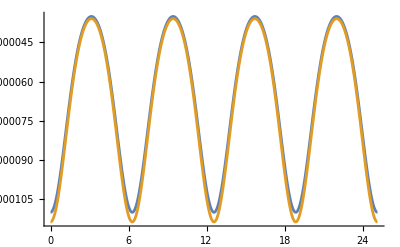

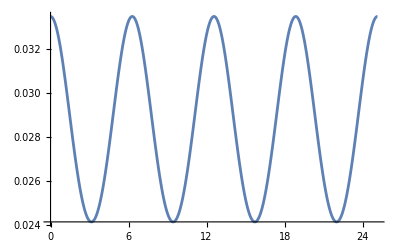

```mathematica
Plot[{FundEdtA/.{sp->0,b->0},FundEdtA/.{sp->1/10,b->0}},{ψ[t],0,8π},PlotPoints->2000]
Plot[{((FundEdtA/.{sp->1/10,b->0})-(FundEdtA/.{sp->0,b->0}))/(FundEdtA/.{sp->0,b->0})},{ψ[t],0,8π},PlotPoints->2000]
```

### Angular momentum flow calculation

```mathematica
dJdtApproxAll=OrderPNSeries[5]@ConrtphitApprox[3,7,"Spacetime"->"Brane"]@dJdt3
```

FdψdtPN:4

FdψdtPN:4

DFdψdtPN:5

FdψdtPN:4

FdψdtPN:4

DFdψdtPN:5

DDFdψdtPN:7

FdψdtPN:4

DFdψdtPN:5

FdψdtPN:4

FdψdtPN:4

FdψdtPN:4

DFdψdtPN:5

FdψdtPN:4

-(4 μ^2 (1+e Cos[ψ_r[t]])^3 (8+e^2+12 e Cos[ψ_r[t]]+3 e^2 Cos[2 ψ_r[t]]))/(5 m M^2 p^(7/2))+(μ^2 (1+e Cos[ψ_r[t]])^3 (80 b+40 e^2+42 b e^2-9 e^4+8 e (6+b (21+e^2)) Cos[ψ_r[t]]+62 b e^2 Cos[2 ψ_r[t]]-32 e^3 Cos[3 ψ_r[t]]+8 b e^3 Cos[3 ψ_r[t]]-15 e^4 Cos[4 ψ_r[t]]))/(5 m M^2 p^(9/2))-(μ^2 sp (1+e Cos[ψ_r[t]])^3 (240+326 e^2+15 e^4+24 e (27+10 e^2) Cos[ψ_r[t]]+6 e^2 (59+7 e^2) Cos[2 ψ_r[t]]+104 e^3 Cos[3 ψ_r[t]]+15 e^4 Cos[4 ψ_r[t]]))/(5 m M^2 p^5)

```mathematica
LKIApprox1=FullSimplify[Integrate[dJdtApproxAll FdtdψPN,{ψ[t],0,2π}]]
dJdtA=OrderPNSeries[5]@(LKIApprox1/KT)
```

-1/(5 m M p^5)π μ^2 (p (27 e^6+64 p (3+p)+6 e^4 (-11+8 p)+8 e^2 (-66+7 p (5+p))-b (160 (3+p)+e^4 (267+8 p)+12 e^2 (125+21 p)))+√p (b (-240-546 e^2+33 e^4+4 e^6)+288 (5+2 p)+2 e^2 (3162+54 e^4+716 p+3 e^2 (515+42 p))) sp+3 (240+866 e^2+166 e^4-33 e^6) sp^2)

(2 (1-e^2)^(3/2) (-2 e^2 (38+27 e^2)+b (40+63 e^2+2 e^4)) μ^2)/(5 m M^2 p^(9/2))-(4 (1-e^2)^(3/2) (8+7 e^2) μ^2)/(5 m M^2 p^(7/2))-(2 (1-e^2)^(3/2) (120+361 e^2+84 e^4) μ^2 sp)/(5 m M^2 p^5)

```mathematica
dJdtA=Series[LKIApprox1/KT,{sp,0,1},{b,0,1},{p,Infinity,5}]//Simplify//Normal
```

-(4 e^2 (1-e^2)^(3/2) (38+27 e^2) μ^2)/(5 m M^2 p^(9/2))+(2 b (1-e^2)^(3/2) (40+63 e^2+2 e^4) μ^2)/(5 m M^2 p^(9/2))-(4 (1-e^2)^(3/2) (8+7 e^2) μ^2)/(5 m M^2 p^(7/2))-(2 (1-e^2)^(3/2) (120+361 e^2+84 e^4) μ^2 sp)/(5 m M^2 p^5)

## Conclution

### {e’[t],p’[t]}

```mathematica
$Assumptions=And[t[]∈Reals,r[]∈Reals,r[]>0,θ[]∈Reals,π>=θ[]>=0,ϕ[]∈Reals,G∈Reals,G>0,M∈Reals,M>=0,e>0,e<1,p>0,Z>0,-b+p>0];
```

```mathematica
v=1/√p;
dEdtShP=(-1247/336-(9181 e^2)/672+(809 e^4)/128+(8609 e^6)/5376) v^2+(4 π+(1375 e^2 π)/48+(3935 e^4 π)/192+(10007 e^6 π)/9216+(2321 e^8 π)/221184-(237857 e^10 π)/88473600) v^3+(23329/9072-(142187 e^2)/2592-(3454195 e^4)/24192+(14543 e^6)/2304+(371627 e^8)/64512-5/64 (1-e^2)^(3/2) (96+292 e^2+37 e^4))v^4+(-(8191 π)/672-(44531 π e^2)/336-(4311389 π e^4)/43008+(15670391 π e^6)/387072+(32271047 π e^8)/7077888+(9561889 π e^10)/77414400)v^5+((-1712/105-(14552 e^2)/63-(553297 e^4)/1260-(187357 e^6)/1260-(10593 e^8)/2240)*(Log[v]+EulerGamma-(35 π^2)/107)+(6643739519/69854400-(3424 Log[2])/105)+1/27941760(43072561991-1214889984 Log[2]-11676113064 Log[3]) e^2+(-51737561/120960-(553297 Log[2])/630+1/279417600(1039287335213-2481151780800 Log[2]+1313562719700 Log[3])) e^4+(27065599/120960-(187357 Log[2])/630+1/372556800(534282768534+36936040753920 Log[2]-8989796218095 Log[3]-10057373046875 Log[5])) e^6+(-9014507/3870720-(10593 Log[2])/1120+1/2980454400(2094827962497-1935417141356160 Log[2]-180498923669295 Log[3]+955450439453125 Log[5])) e^8+(-27966079/1935360+1/204374016000(91630937815920+677138829375619072 Log[2]+308357289757981629 Log[3]-360291021728515625 Log[5]-117345477841261131 Log[7])) e^10)v^6+(-(16285 π)/504-(22798583 π e^2)/48384-(65448785 π e^4)/48384-(41758768871 π e^6)/41803776-(306245599 π e^8)/7962624+(183849241019 π e^10)/107017666560)v^7;
dJdtShP=(-1247/336-(425 e^2)/336+(10751 e^4)/2688) v^2+(4 π+(97 π e^2)/8+(49 π e^4)/32-(49 π e^6)/4608-(109 π e^8)/36864-(2567 π e^10)/14745600) v^3+(23329/9072-(331243 e^2)/6048-(871775 e^4)/24192+(209911 e^6)/16128-15/16 (1-e^2)^(3/2) (8+7 e^2))v^4+(-(8191 π)/672-(48361 π e^2)/1344+(1657493 π e^4)/43008+(5458969 π e^6)/774144-(11237131 π e^8)/49545216-(13887257 π e^10)/2477260800)v^5+((-1712/105-(24503 e^2)/210-(11663 e^4)/140-(2461 e^6)/560)*(Log[v]+EulerGamma-(35 π^2)/107)+(6643739519/69854400-(3424 Log[2])/105)+e^2 (6769212511/8731800+(1391 Log[2])/30-(78003 Log[3])/280)-(107 e^4 (-44816749+361006800 Log[2]-197026830 Log[3]))/7761600+(e^6 (31707715321+8118485180960 Log[2]-2217650640975 Log[3]-2011474609375 Log[5]))/186278400-(e^8 (-13058170551+20261538626560 Log[2]+1202778646938 Log[3]-9540136718750 Log[5]))/85155840+(e^10 (278769726000+3128437083799552 Log[2]+1343747575945359 Log[3]-1650584716796875 Log[5]-507989081563901 Log[7]))/3096576000)v^6+(-(16285 π)/504-(396733 π e^2)/1008-(27639271 π e^4)/48384+(658044449 π e^6)/20901888+(2930710283 π e^8)/167215104-(156157243379 π e^10)/26754416640)v^7;
```

```mathematica
dEdtA=-(96(1-e^2)^(3/2) μ)/(15  p^5 M^2)((96+292 e^2+37 e^4)/96+ dEdtShP) + (4 (1-e^2)^(3/2) (24+104 e^2+33 e^4) μ b)/(5 M^2 p^6) -((1-e^2)^(3/2) (864+5532 e^2+4035 e^4+251 e^6) μ sp)/(15 M^2 p^(13/2));
dJdtA=-(32 (1-e^2)^(3/2) μ)/(5 M^2 p^(7/2)) ((8+7 e^2)/8+ dJdtShP)+ (2 b (1-e^2)^(3/2) (40+63 e^2+2 e^4) μ)/(5 M^2 p^(9/2)) -(2 (1-e^2)^(3/2) (120+361 e^2+84 e^4) μ sp)/(5 M^2 p^5);
dEdtAt=Simplify[dEdtA/.{p->pt[t[]],e->et[t[]],Z->(1-et[t[]]^2)},1-et[t[]]^2>0];
dJdtAt=Simplify[dJdtA/.{p->pt[t[]],e->et[t[]],Z->(1-et[t[]]^2)},1-et[t[]]^2>0];
```

```mathematica
ETopeApprox=EJTope["Spacetime" -> "Brane"]@(ℰ);
JTopeApprox=EJTope["Spacetime" -> "Brane"]@(𝒥);
ETopeApproxt=Simplify[ETopeApprox/.{p->pt[t[]],e->et[t[]],Z->(1-et[t[]]^2)}];
JTopeApproxt=Simplify[JTopeApprox/.{p->pt[t[]],e->et[t[]],Z->(1-et[t[]]^2)}];
```

```mathematica
$Assumptions=And[t[]∈Reals,r[]∈Reals,r[]>0,θ[]∈Reals,π>=θ[]>=0,ϕ[]∈Reals,G∈Reals,G>0,M∈Reals,M>=0,e>0,e<1,p>0,Z>0,b-pt[t]<0,et[t[]]>0,pt[t]>0,2 b+et[t]^2 (2 b-pt[t])-3 pt[t]+pt[t]^2>0];
```

##### Scheme Main **

```mathematica
ETopeApprox=EJTope["Spacetime" -> "Brane"]@(ℰ);
JTopeApprox=EJTope["Spacetime" -> "Brane"]@(𝒥);

ETopeApproxt=Simplify[ETopeApprox/.{p->pt[t[]],e->et[t[]],Z->(1-et[t[]]^2)}];
JTopeApproxt=Simplify[JTopeApprox/.{p->pt[t[]],e->et[t[]],Z->(1-et[t[]]^2)}];

JJ=Simplify@{{D[ETopeApproxt, et[t[]]],D[ETopeApproxt, pt[t[]]]},{D[JTopeApproxt, et[t[]]],D[JTopeApproxt, pt[t[]]]}};
Iconize[Dot[Inverse[JJ],{dEdtAt,dJdtAt}],"{e'[t],p'[t]}"]
```

### Evolutions of e & p

```mathematica
{spA,snA,eA,pA,bA,MA,mA}={1/10,1/10,et[t[]],pt[t[]],1/10,1,1/1};

etE=2/10;

Fig=Table[
{spA,bA}=sb;
ptEISCO=6+2 etE + 2 √(2/3) spA - 3/2 bA + 0.04;
Timeend=800;
λtE=λt/.FindInstance[N@ParamExactBW[spA,snA,etE,ptEISCO,bA,MA]@t0[λt]==Timeend,λt,Reals][[1]];
{sol}=NDSolve[{
D[et[tNum], tNum]==Evaluate[[[1]]/.{t[]->tNum}/.{sp->spA,b->bA,M->MA,μ->mA}//N],
D[pt[tNum], tNum]==Evaluate[[[2]]/.{t[]->tNum}/.{sp->spA,b->bA,M->MA,μ->mA}//N],
et[0]== etE//N,
pt[0]== 15-5 etE//N,
WhenEvent[pt[tNum]==6+2 et[tNum] + 2 √(2/3) spA - 3/2 bA + 0.04 ,{Print[{"End",pt[tNum]}]};Timeend=tNum;"StopIntegration"]
}
,{et,pt},{tNum,0,Timeend}];
λFun=λ/.sol;

etFun=et/.sol;
ptFun=pt/.sol;
Clear[sol];
ParametricPlot[{ptFun[tNum],etFun[tNum]},{tNum,0,Timeend},PlotRange->{{6,16},{0,0.7}},AspectRatio->0.6,PlotStyle->MyColor[[IntegerPart[1+10 (bA+spA)]]],PlotTheme->"Scientific"]

,{etE,1/5,4/5,1/10},{sb,{{0,0},{1/10,0},{1/10,1/10}}}];

Figep=Show[Table[{spA,bA}=sb;Plot[1/12 (9 bA+6 p-4 (9+√6 spA)),{p,6,8},AspectRatio->0.7,
PlotStyle->MyStyle[[IntegerPart[1+10 (bA+spA)]]],PlotRange->{{6,14},{0,0.7}},PlotTheme->"Scientific",
FrameLabel->{Style["p",Bold,16,FontFamily->"Times"],Style["e",Bold,16,FontFamily->"Times"]},
FrameStyle->Directive[Black,15],
PlotLegends->Placed[LineLegend[{MyColor[[IntegerPart[1+10 (bA+spA)]]]},{"s_(||)="<>ToString[spA]<>";b="<>ToString[bA]}],{Right,Top}]]
,{sb,{{0,0},{0.1,0},{0.1,0.1}}}],Fig]
```

### b=0.1

```mathematica
{spA,snA,eA,pA,bA,MA,mA}={1/5,1/5,et[t[]],pt[t[]],1/10,1,1/10};

etE=1/10;

ptEISCO=6+2 etE + 2 √(2/3) spA - 3/2 bA + 0.1
Timeend=3000;

{sol}=NDSolve[{
D[et[tNum], tNum]==Evaluate[[[1]]/.{t[]->tNum}/.{sp->spA,b->bA,M->MA,μ->mA}//N],
D[pt[tNum], tNum]==Evaluate[[[2]]/.{t[]->tNum}/.{sp->spA,b->bA,M->MA,μ->mA}//N],
et[Timeend]==etE,
pt[Timeend]==ptEISCO
}
,{et,pt},{tNum,0,Timeend}];
etFun=et/.sol;
ptFun=pt/.sol;


λt[t_,spA_,snA_,etE_,ptEISCO_,bA_,MA_]:=Module[{},λt/.FindInstance[N@ParamExactBW[spA,snA,etE,ptEISCO,bA,MA]@t0[λt]==t,λt,Reals][[1]]]
Tspace=N@Table[Timeend-x^2,{x,0,√Timeend,√Timeend/300}];
λtData=Table[{tNum,λt[tNum,spA,snA,etFun[tNum],ptFun[tNum],bA,MA]},{tNum,Tspace}];
λtFun=Interpolation[λtData];

Show[ParametricPlot[{ptFun[tNum],etFun[tNum]},{tNum,0,Timeend},PlotRange->{{6,20},{0,1}},AspectRatio->0.6,PlotStyle->Red],
Plot[1/12 (9bA+6 p-4 (9+√6 spA)),{p,6,8},PlotStyle->Gray]]

{Plot[λtFun[tNum],{tNum,0,Timeend},PlotRange->All],Plot[etFun[tNum],{tNum,0,Timeend},PlotRange->All],
Plot[ptFun[tNum],{tNum,0,Timeend},PlotRange->All]}
```

```mathematica
Tspace=N@Table[Timeend-x^2,{x,0,√Timeend,√Timeend/2000}];
OrbitSpinPData=ParallelTable[ParamExactBW[spA,snA,etFun[tNum],ptFun[tNum],bA,MA]@{Style[{(r0λ[λtFun[tNum]] Sin[θ0[λtFun[tNum]]]) Cos[φ0[λtFun[tNum]]],
(r0λ[λtFun[tNum]] Sin[θ0[λtFun[tNum]]]) Sin[φ0[λtFun[tNum]]],r0λ[λtFun[tNum]] Cos[θ0[λtFun[tNum]]]},ColorData["Rainbow"][tNum/Timeend]]},{tNum,Tspace}];
```

PrintAsCharacter::argx: 调用 PrintAsCharacter 时使用了 0 个参数；应该用 1 个参数.

```mathematica
FigOrbit=Show@{ListPointPlot3D[OrbitSpinPData[[;;,1]],PlotRange->{{-15,15},{-15,15},{-2.5,2.5}},AxesLabel->{"x/M","y/M","z/M"},BoxRatios->Automatic,
PlotStyle->AbsolutePointSize[2],PlotLegends->BarLegend[{"Rainbow",{0,Timeend}},LegendLabel->Style[t,16,FontFamily->"Times"],LabelStyle->{FontSize->13},LegendMarkerSize->100]],
Graphics3D[{Black,Sphere[{0,0,0},2],MyColor3,Opacity[0.5],Sphere[{0,0,0},6 + 2 etFun[Timeend] + 2 √(2/3) spA - 3/2 bA]}]}
```

-Graphics3D-